```mathematica
ClearAll["Global`*"];

(* =========================================*)
(*PHASE 2:NATIVE MATHEMATICA Hg CALIBRATION*)
(*Main-report numerical analysis*)
(* =========================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

hgDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Hg_calibration"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

fitDir=FileNameJoin[{outRoot,"Hg_native_fit_reports"}];
calDir=FileNameJoin[{outRoot,"Calibration_outputs"}];

CreateDirectory[fitDir];
CreateDirectory[calDir];

Print["Output folder: ",outRoot];


(*----------helpers----------*)

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",hgDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

fmt[x_]:=ToString[NumberForm[N[x],{Infinity,6},NumberPoint->"."]];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_"}];


(*----------Hg specs----------*)
(*Use 365.588,404.770,546.226 as main calibration points.The 365.119 scan is saved as diagnostic only because it appears crowded/ambiguous.The repeated 546 scans are repeatability checks,not independent calibration lines.*)

hgSpecs={<|"id"->"Hg 365.119 diagnostic","fileKey"->"365.12","trueWL"->365.119,"window"->{365.50,365.85},"useForCalibration"->False|>,<|"id"->"Hg 365.588","fileKey"->"365.588","trueWL"->365.588,"window"->{365.50,365.90},"useForCalibration"->True|>,<|"id"->"Hg 404.770","fileKey"->"404.770","trueWL"->404.770,"window"->{405.05,405.42},"useForCalibration"->True|>,<|"id"->"Hg 546.226","fileKey"->"546.226","trueWL"->546.226,"window"->{546.50,546.92},"useForCalibration"->True|>,<|"id"->"Hg 546 repeat wide","fileKey"->"562hg_2nm_scan","trueWL"->546.226,"window"->{546.55,546.90},"useForCalibration"->False|>,<|"id"->"Hg 546 repeat 20um","fileKey"->"same_data","trueWL"->546.226,"window"->{546.55,546.90},"useForCalibration"->False|>};


(*----------fit one peak----------*)

fitOneHg[spec_]:=Module[{file,dataFull,data,xvals,yvals,xmin,xmax,c0,d0,amp0,mu0,sig0,x0,edgeN,fit,params,errs,resid,rms,maxresid,fitPlot,residPlot,table,report,outFile,c,d,amp,mu,sig,x},file=findFile[spec["fileKey"]];
If[MissingQ[file],Print["Missing file for ",spec["id"]];
Return[<|"id"->spec["id"],"status"->"file_missing"|>]];
dataFull=importNumeric[file];
data=cropData[dataFull,spec["window"]];
If[Length[data]<8,Print["Too few points for ",spec["id"]];
Return[<|"id"->spec["id"],"status"->"too_few_points"|>]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
x0=Mean[{xmin,xmax}];
edgeN=Min[5,Length[yvals]];
	c0=Median[Join[Take[yvals,edgeN],Take[yvals,-edgeN]]];
d0=0;
amp0=Max[yvals]-c0;
mu0=xvals[[First@Ordering[yvals,-1]]];
sig0=(xmax-xmin)/6;
fit=Quiet@NonlinearModelFit[data,c+d (x-x0)+amp Exp[-(x-mu)^2/(2 sig^2)],{{c,c0},{d,d0},{amp,amp0},{mu,mu0},{sig,sig0}},x,MaxIterations->10000];
params=fit["BestFitParameters"];
errs=fit["ParameterErrors"];
resid=data/. {xx_,yy_}:>{xx,yy-fit[xx]};
rms=Sqrt[Mean[resid[[All,2]]^2]];
maxresid=Max[Abs[resid[[All,2]]]];
fitPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,8},PlotRange->All,ImageSize->750,FrameLabel->{"Wavelength (nm)","Signal (V)"},PlotLabel->Style[spec["id"]<>": Gaussian + linear background",14,Black]],Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}]];
residPlot=ListPlot[resid,Frame->True,Axes->False,PlotMarkers->{Automatic,8},PlotRange->All,ImageSize->750,FrameLabel->{"Wavelength (nm)","Residual (V)"},PlotLabel->Style["Residuals",13,Black],GridLines->{None,{0}}];
table=Grid[{{"parameter","estimate","standard error"},{"c",c/. params,errs[[1]]},{"d",d/. params,errs[[2]]},{"amp",amp/. params,errs[[3]]},{"mu",mu/. params,errs[[4]]},{"sigma",sig/. params,errs[[5]]},{"RMS residual",rms,""},{"max |residual|",maxresid,""},{"true Hg wavelength",spec["trueWL"],""},{"used for calibration?",spec["useForCalibration"],""}},Frame->All,Alignment->Left];
report=Column[{Style["Native Mathematica fit report: "<>spec["id"],16,Bold],Style["File: "<>FileNameTake[file],10],Style["Fit window: "<>ToString[spec["window"]]<>" nm",10],fitPlot,residPlot,table},Spacings->1];
outFile=FileNameJoin[{fitDir,makeName[spec["id"]]<>"_native_fit_report.pdf"}];
Export[outFile,report,"PDF"];
<|"id"->spec["id"],"status"->"fit_complete","file"->FileNameTake[file],"trueWL_nm"->spec["trueWL"],"fit_xmin_nm"->xmin,"fit_xmax_nm"->xmax,"n_points"->Length[data],"mu_obs_nm"->(mu/. params),"mu_SE_nm"->errs[[4]],"sigma_nm"->(sig/. params),"sigma_SE_nm"->errs[[5]],"amp"->(amp/. params),"amp_SE"->errs[[3]],"background_c"->(c/. params),"background_d"->(d/. params),"rms_residual"->rms,"max_abs_residual"->maxresid,"useForCalibration"->spec["useForCalibration"],"report_pdf"->outFile|>];


(*----------run fits----------*)

results=fitOneHg/@hgSpecs;

Export[FileNameJoin[{outRoot,"Hg_native_peak_fit_results.csv"}],Prepend[Values/@results,Keys[First[results]]],"CSV"];

Dataset[results]


(*----------calibration fit----------*)

calRows=Select[results,#["status"]=="fit_complete"&&TrueQ[#["useForCalibration"]]&];

calData=({#["mu_obs_nm"],#["trueWL_nm"]}&/@calRows);

linCal=LinearModelFit[calData,{1,x},x];

calParams=linCal["BestFitParameters"];
calErrors=linCal["ParameterErrors"];

a=calParams[[1]];
b=calParams[[2]];

sigmaA=calErrors[[1]];
sigmaB=calErrors[[2]];

calResiduals=calData/. {xo_,yt_}:>{xo,yt-linCal[xo]};
resVals=calResiduals[[All,2]];

rmsCal=Sqrt[Mean[resVals^2]];
maxCal=Max[Abs[resVals]];

calSummary={{"quantity","value"},{"a_intercept_nm",a},{"sigma_a_nm",sigmaA},{"b_slope",b},{"sigma_b",sigmaB},{"RMS_residual_nm",rmsCal},{"max_abs_residual_nm",maxCal}};

Export[FileNameJoin[{calDir,"Hg_linear_calibration_summary.csv"}],calSummary,"CSV"];

Export[FileNameJoin[{calDir,"Hg_calibration_points.csv"}],Prepend[calData,{"observed_mu_nm","true_vacuum_wavelength_nm"}],"CSV"];

Export[FileNameJoin[{calDir,"Hg_linear_calibration_residuals.csv"}],Prepend[calResiduals,{"observed_mu_nm","true_minus_fit_nm"}],"CSV"];

calPlot=Show[ListPlot[calData,Frame->True,Axes->False,PlotMarkers->{Automatic,10},ImageSize->800,FrameLabel->{"Observed Hg center (nm)","True Hg vacuum wavelength (nm)"},PlotLabel->Style["Hg calibration: true wavelength vs observed center",14,Black]],Plot[linCal[x],{x,Min[calData[[All,1]]]-0.5,Max[calData[[All,1]]]+0.5},PlotStyle->{Red,Thick}]];

residPlot=ListPlot[calResiduals,Frame->True,Axes->False,PlotMarkers->{Automatic,10},ImageSize->800,FrameLabel->{"Observed Hg center (nm)","Residual true - fit (nm)"},PlotLabel->Style["Hg calibration residuals",14,Black],GridLines->{None,{0}}];

Export[FileNameJoin[{calDir,"Hg_linear_calibration_plot.pdf"}],calPlot,"PDF"];
Export[FileNameJoin[{calDir,"Hg_linear_calibration_residuals.pdf"}],residPlot,"PDF"];

Print["Linear calibration:"];
Print["lambda_true = a + b lambda_obs"];
Print["a = ",a," ± ",sigmaA];
Print["b = ",b," ± ",sigmaB];
Print["RMS residual = ",rmsCal," nm"];
Print["Max abs residual = ",maxCal," nm"];

Print["DONE. Open output folder:"];
Print[outRoot];

SystemOpen[outRoot];
```

Output folder: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE2_Hg_calibration_native

Linear calibration:

lambda_true = a + b lambda_obs

a = 0.423395 ± 0.738372

b = 0.998274 ± 0.00165547

RMS residual = 0.128662 nm

Max abs residual = 0.173043 nm

DONE. Open output folder:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE2_Hg_calibration_native

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*CLEAN PHASE 2 Hg OUTPUTS:NO TABLES IN PDF*)
(*Tables saved separately for LaTeX*)
(* =====================================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

hgDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Hg_calibration"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

fitFigDir=FileNameJoin[{outRoot,"fit_figures_no_tables"}];
tableDir=FileNameJoin[{outRoot,"tables_for_latex"}];
calFigDir=FileNameJoin[{outRoot,"compact_calibration_figures"}];

CreateDirectory/@{fitFigDir,tableDir,calFigDir};

font="Arial";

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",hgDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_"}];

hgSpecs={<|"id"->"Hg 365.119 diagnostic","fileKey"->"365.12","trueWL"->365.119,"window"->{365.50,365.85},"useForCalibration"->False|>,<|"id"->"Hg 365.588","fileKey"->"365.588","trueWL"->365.588,"window"->{365.50,365.90},"useForCalibration"->True|>,<|"id"->"Hg 404.770","fileKey"->"404.770","trueWL"->404.770,"window"->{405.05,405.42},"useForCalibration"->True|>,<|"id"->"Hg 546.226","fileKey"->"546.226","trueWL"->546.226,"window"->{546.50,546.92},"useForCalibration"->True|>,<|"id"->"Hg 546 repeat wide","fileKey"->"562hg_2nm_scan","trueWL"->546.226,"window"->{546.55,546.90},"useForCalibration"->False|>,<|"id"->"Hg 546 repeat 20um","fileKey"->"same_data","trueWL"->546.226,"window"->{546.55,546.90},"useForCalibration"->False|>};

fitOneHgClean[spec_]:=Module[{file,dataFull,data,xvals,yvals,xmin,xmax,edgeN,c0,d0,amp0,mu0,sig0,x0,fit,params,errs,resid,rms,maxresid,fitPlot,residPlot,combinedFig,outFile,c,d,amp,mu,sig,x},file=findFile[spec["fileKey"]];
If[MissingQ[file],Return[<|"id"->spec["id"],"status"->"file_missing"|>]];
dataFull=importNumeric[file];
data=cropData[dataFull,spec["window"]];
If[Length[data]<8,Return[<|"id"->spec["id"],"status"->"too_few_points"|>]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
x0=Mean[{xmin,xmax}];
edgeN=Min[5,Length[yvals]];
c0=Median[Join[Take[yvals,edgeN],Take[yvals,-edgeN]]];
d0=0;
amp0=Max[yvals]-c0;
mu0=xvals[[First@Ordering[yvals,-1]]];
sig0=(xmax-xmin)/6;
fit=Quiet@NonlinearModelFit[data,c+d (x-x0)+amp Exp[-(x-mu)^2/(2 sig^2)],{{c,c0},{d,d0},{amp,amp0},{mu,mu0},{sig,sig0}},x,MaxIterations->10000];
params=fit["BestFitParameters"];
errs=fit["ParameterErrors"];
resid=data/. {xx_,yy_}:>{xx,yy-fit[xx]};
rms=Sqrt[Mean[resid[[All,2]]^2]];
maxresid=Max[Abs[resid[[All,2]]]];
fitPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->420,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[spec["id"],11,FontFamily->font]],Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}]];
residPlot=ListPlot[resid,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->420,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals",11,FontFamily->font],GridLines->{None,{0}}];
combinedFig=GraphicsColumn[{fitPlot,residPlot},Spacings->0.15,ImageSize->430];
outFile=FileNameJoin[{fitFigDir,makeName[spec["id"]]<>"_fit_residual_clean.pdf"}];
Export[outFile,combinedFig,"PDF"];
<|"id"->spec["id"],"status"->"fit_complete","trueWL_nm"->spec["trueWL"],"mu_obs_nm"->(mu/. params),"mu_SE_nm"->errs[[4]],"sigma_nm"->(sig/. params),"sigma_SE_nm"->errs[[5]],"amp"->(amp/. params),"amp_SE"->errs[[3]],"background_c"->(c/. params),"background_d"->(d/. params),"rms_residual"->rms,"max_abs_residual"->maxresid,"useForCalibration"->spec["useForCalibration"],"figure_pdf"->outFile|>];

results=fitOneHgClean/@hgSpecs;

Export[FileNameJoin[{tableDir,"Hg_native_peak_fit_results.csv"}],Prepend[Values/@results,Keys[First[results]]],"CSV"];

(*Optional LaTeX-ready table body*)
latexRows=Select[results,#["status"]=="fit_complete"&]/. r_Association:>StringRiffle[{r["id"],NumberForm[r["trueWL_nm"],{8,3}],NumberForm[r["mu_obs_nm"],{8,3}],NumberForm[r["mu_SE_nm"],{8,5}],NumberForm[r["sigma_nm"],{8,4}],NumberForm[r["rms_residual"],{8,4}],r["useForCalibration"]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"Hg_native_peak_fit_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

(*Calibration using selected rows*)
calRows=Select[results,#["status"]=="fit_complete"&&TrueQ[#["useForCalibration"]]&];

calData=({#["mu_obs_nm"],#["trueWL_nm"]}&/@calRows);

linCal=LinearModelFit[calData,{1,x},x];

calParams=linCal["BestFitParameters"];
calErrors=linCal["ParameterErrors"];

a=calParams[[1]];
b=calParams[[2]];
sigmaA=calErrors[[1]];
sigmaB=calErrors[[2]];

calResiduals=calData/. {xo_,yt_}:>{xo,yt-linCal[xo]};
resVals=calResiduals[[All,2]];

rmsCal=Sqrt[Mean[resVals^2]];
maxCal=Max[Abs[resVals]];

Export[FileNameJoin[{tableDir,"Hg_linear_calibration_summary.csv"}],{{"quantity","value"},{"a_intercept_nm",a},{"sigma_a_nm",sigmaA},{"b_slope",b},{"sigma_b",sigmaB},{"RMS_residual_nm",rmsCal},{"max_abs_residual_nm",maxCal}},"CSV"];

Export[FileNameJoin[{tableDir,"Hg_linear_calibration_residuals.csv"}],Prepend[calResiduals,{"observed_mu_nm","true_minus_fit_nm"}],"CSV"];

(*Compact combined calibration figure*)
calPlot=Show[ListPlot[calData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->330,FrameLabel->{"Observed center (nm)","True wavelength (nm)"},LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},PlotLabel->Style["Calibration",10,FontFamily->font]],Plot[linCal[x],{x,Min[calData[[All,1]]]-1,Max[calData[[All,1]]]+1},PlotStyle->{Red,Thick}]];

calResidPlot=ListPlot[calResiduals,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->330,FrameLabel->{"Observed center (nm)","Residual (nm)"},LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},PlotLabel->Style["Calibration residuals",10,FontFamily->font],GridLines->{None,{0}},PlotRange->All];

combinedCalFig=GraphicsRow[{calPlot,calResidPlot},Spacings->0.25,ImageSize->700];

Export[FileNameJoin[{calFigDir,"Hg_calibration_and_residuals_compact.pdf"}],combinedCalFig,"PDF"];

Print["Clean outputs saved here:"];
Print[outRoot];

Print["Calibration:"];
Print["lambda_true = a + b lambda_obs"];
Print["a = ",a," ± ",sigmaA];
Print["b = ",b," ± ",sigmaB];
Print["RMS residual = ",rmsCal," nm"];
Print["Max residual = ",maxCal," nm"];

SystemOpen[outRoot];
```

Clean outputs saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE2_Hg_calibration_native_clean

Calibration:

lambda_true = a + b lambda_obs

a = 0.423395 ± 0.738372

b = 0.998274 ± 0.00165547

RMS residual = 0.128662 nm

Max residual = 0.173043 nm

```mathematica
ClearAll["Global`*"];

(* ==========================================*)
(*PHASE 3:Instrument resolution from Hg fits*)
(* ==========================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

cleanRoot=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean"}];

tableDir=FileNameJoin[{cleanRoot,"tables_for_latex"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE3_instrument_resolution"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

font="Arial";

fitCSV=FileNameJoin[{tableDir,"Hg_native_peak_fit_results.csv"}];

rows=Import[fitCSV,"CSV"];
headers=First[rows];
dataRows=Rest[rows];

records=AssociationThread[headers->#]&/@dataRows;

num[row_,key_]:=Quiet@Check[N@ToExpression[row[key]],Missing["NotNumeric"]];

bool[row_,key_]:=ToString[row[key]]=="True";

usable=Select[records,ToString[#["status"]]=="fit_complete"&];

resolutionRows=Table[Module[{id,trueWL,mu,sig,sigSE,fwhm,fwhmSE,rms,used},id=row["id"];
trueWL=num[row,"trueWL_nm"];
mu=num[row,"mu_obs_nm"];
sig=num[row,"sigma_nm"];
sigSE=num[row,"sigma_SE_nm"];
rms=num[row,"rms_residual"];
used=bool[row,"useForCalibration"];
fwhm=2 Sqrt[2 Log[2]] sig;
fwhmSE=2 Sqrt[2 Log[2]] sigSE;
<|"id"->id,"trueWL_nm"->trueWL,"observed_mu_nm"->mu,"sigma_nm"->sig,"sigma_SE_nm"->sigSE,"FWHM_nm"->fwhm,"FWHM_SE_nm"->fwhmSE,"rms_residual_V"->rms,"used_for_calibration"->used|>],{row,usable}];

Export[FileNameJoin[{outRoot,"instrument_resolution_from_Hg.csv"}],Prepend[Values/@resolutionRows,Keys[First[resolutionRows]]],"CSV"];

latexRows=resolutionRows/. r_Association:>StringRiffle[{r["id"],NumberForm[r["trueWL_nm"],{8,3}],NumberForm[r["sigma_nm"],{8,4}],NumberForm[r["FWHM_nm"],{8,4}],NumberForm[r["rms_residual_V"],{8,4}],r["used_for_calibration"]}," & "]<>" \\\\";

Export[FileNameJoin[{outRoot,"instrument_resolution_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

(*Expected rough H-D separations only for scale,not final fitting*)
balmerWL={656.28,486.13,434.05,410.17,397.01,388.91};
hdSepScale=0.5/1836 balmerWL;

scaleData=Transpose[{balmerWL,hdSepScale}];

fwhmData=({#["trueWL_nm"],#["FWHM_nm"]}&/@Select[resolutionRows,NumericQ[#["trueWL_nm"]]&&NumericQ[#["FWHM_nm"]]&]);

fwhmPlot=Show[ListPlot[fwhmData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->430,FrameLabel->{"Wavelength (nm)","Width (nm)"},PlotLabel->Style["Hg instrumental width estimate",11,FontFamily->font],LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font}],ListPlot[scaleData,PlotMarkers->{"○",8}],PlotRange->All];

Export[FileNameJoin[{outRoot,"Hg_FWHM_vs_HD_separation_scale.pdf"}],fwhmPlot,"PDF"];

Print["Instrument resolution outputs saved here:"];
Print[outRoot];

Print["Resolution table:"];
Dataset[resolutionRows]

SystemOpen[outRoot];
```

Instrument resolution outputs saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE3_instrument_resolution

Resolution table:

```mathematica
ClearAll["Global`*"];

(* ==========================================*)
(*PHASE 4:Hydrogen-only control fits*)
(* ==========================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

hOnlyDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Hydrogen_only_control"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE4_Hydrogen_only_control"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"fit_figures_no_tables"}];
tableDir=FileNameJoin[{outRoot,"tables_for_latex"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_","α"->"alpha","β"->"beta","γ"->"gamma","δ"->"delta","ϵ"->"epsilon","ζ"->"zeta"}];

balmerLabel[w_]:=Which[Abs[w-656.3]<5,"H alpha",Abs[w-486.1]<5,"H beta",Abs[w-434.0]<5,"H gamma",Abs[w-410.2]<5,"H delta",Abs[w-397.0]<5,"H epsilon",Abs[w-388.9]<5,"H zeta",True,"unknown"];

fitOneHOnly[file_]:=Module[{data,xvals,yvals,xmin,xmax,edgeN,c0,d0,amp0,mu0,sig0,x0,fit,params,errs,resid,rms,maxresid,fitPlot,residPlot,combinedFig,outFile,centerGuess,label,c,d,amp,mu,sig,x},data=importNumeric[file];
If[Length[data]<8,Return[<|"file"->FileNameTake[file],"status"->"too_few_points"|>]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
centerGuess=Median[xvals];
label=balmerLabel[centerGuess];
x0=Mean[{xmin,xmax}];
edgeN=Min[5,Length[yvals]];
c0=Median[Join[Take[yvals,edgeN],Take[yvals,-edgeN]]];
d0=0;
amp0=Max[yvals]-c0;
mu0=xvals[[First@Ordering[yvals,-1]]];
sig0=(xmax-xmin)/8;
fit=Quiet@NonlinearModelFit[data,c+d (x-x0)+amp Exp[-(x-mu)^2/(2 sig^2)],{{c,c0},{d,d0},{amp,amp0},{mu,mu0},{sig,sig0}},x,MaxIterations->10000];
params=fit["BestFitParameters"];
errs=fit["ParameterErrors"];
resid=data/. {xx_,yy_}:>{xx,yy-fit[xx]};
rms=Sqrt[Mean[resid[[All,2]]^2]];
maxresid=Max[Abs[resid[[All,2]]]];
fitPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->420,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[label<>" hydrogen-only control",11,FontFamily->font]],Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}]];
residPlot=ListPlot[resid,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->420,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals",11,FontFamily->font],GridLines->{None,{0}}];
combinedFig=GraphicsColumn[{fitPlot,residPlot},Spacings->0.15,ImageSize->430];
outFile=FileNameJoin[{figDir,makeName[label]<>"_hydrogen_only_fit_residual.pdf"}];
Export[outFile,combinedFig,"PDF"];
<|"label"->label,"file"->FileNameTake[file],"status"->"fit_complete","mu_obs_nm"->(mu/. params),"mu_SE_nm"->errs[[4]],"sigma_nm"->(sig/. params),"sigma_SE_nm"->errs[[5]],"FWHM_nm"->2 Sqrt[2 Log[2]] (sig/. params),"amp"->(amp/. params),"amp_SE"->errs[[3]],"background_c"->(c/. params),"background_d"->(d/. params),"rms_residual"->rms,"max_abs_residual"->maxresid,"figure_pdf"->outFile|>];

files=Sort@FileNames["*_REAL_FOR_CURVEFIT.dat",hOnlyDir];

results=fitOneHOnly/@files;

Export[FileNameJoin[{tableDir,"hydrogen_only_fit_results.csv"}],Prepend[Values/@results,Keys[First[results]]],"CSV"];

latexRows=Select[results,#["status"]=="fit_complete"&]/. r_Association:>StringRiffle[{r["label"],NumberForm[r["mu_obs_nm"],{8,3}],NumberForm[r["mu_SE_nm"],{8,5}],NumberForm[r["sigma_nm"],{8,4}],NumberForm[r["FWHM_nm"],{8,4}],NumberForm[r["rms_residual"],{8,4}]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"hydrogen_only_fit_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

(*compact summary figure:line width vs center*)
summaryData=Select[results,#["status"]=="fit_complete"&];

widthData=({#["mu_obs_nm"],#["FWHM_nm"]}&/@summaryData);
rmsData=({#["mu_obs_nm"],#["rms_residual"]}&/@summaryData);

widthPlot=ListPlot[widthData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->330,FrameLabel->{"H-only center (nm)","FWHM (nm)"},LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},PlotLabel->Style["H-only line width",10,FontFamily->font]];

rmsPlot=ListPlot[rmsData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->330,FrameLabel->{"H-only center (nm)","RMS residual (V)"},LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},PlotLabel->Style["Single-peak residual scale",10,FontFamily->font]];

combinedSummary=GraphicsRow[{widthPlot,rmsPlot},Spacings->0.25,ImageSize->700];

Export[FileNameJoin[{outRoot,"hydrogen_only_width_and_residual_summary.pdf"}],combinedSummary,"PDF"];

Print["DONE Phase 4 hydrogen-only controls."];
Print["Output folder:"];
Print[outRoot];

Dataset[results]

SystemOpen[outRoot];
```

DONE Phase 4 hydrogen-only controls.

Output folder:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE4_Hydrogen_only_control

```mathematica
ClearAll["Global`*"];

(* ===============================================*)
(*TWO-GAUSSIAN FITS FOR H EPSILON AND H ZETA*)
(*Hydrogen peak+nearby contaminating feature*)
(* ===============================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

hOnlyDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Hydrogen_only_control"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE4_Hydrogen_only_two_gaussian_checks"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"fit_figures"}];
tableDir=FileNameJoin[{outRoot,"tables"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",hOnlyDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_"}];

aic[n_,rss_,k_]:=n Log[rss/n]+2 k;
bic[n_,rss_,k_]:=n Log[rss/n]+k Log[n];

ampNear[data_,muGuess_,base_,width_]:=Module[{near},near=Select[data,Abs[#[[1]]-muGuess]<=width&];
If[Length[near]==0,Max[data[[All,2]]]-base,Max[near[[All,2]]]-base]];

targets={<|"label"->"H epsilon","fileKey"->"397.765","window"->{397.15,398.05},"muHGuess"->397.28,"muIGuess"->397.78,"sigGuess"->0.055|>,<|"label"->"H zeta","fileKey"->"389.035","window"->{388.65,389.12},"muHGuess"->388.84,"muIGuess"->388.96,"sigGuess"->0.045|>};

fitTarget[target_]:=Module[{file,dataFull,data,xvals,yvals,xmin,xmax,x0,edgeN,c0,d0,ampH0,ampI0,sig0,fit1,fit2Shared,fit2Independent,p1,p2s,p2i,r1,r2s,r2i,rss1,rss2s,rss2i,npts,x,c,d,amp,mu,sig,ampH,ampI,muH,muI,sigH,sigI,model1,model2s,model2i,figShared,figIndependent,residualPlotShared,residualPlotIndependent,compHShared,compIShared,compHIndependent,compIIndependent,outShared,outIndependent,rows},file=findFile[target["fileKey"]];
If[MissingQ[file],Print["Missing file for ",target["label"]];
Return[$Failed]];
dataFull=importNumeric[file];
data=cropData[dataFull,target["window"]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
npts=Length[data];
x0=Mean[{xmin,xmax}];
edgeN=Min[5,Length[yvals]];
c0=Median[Join[Take[yvals,edgeN],Take[yvals,-edgeN]]];
d0=0;
sig0=target["sigGuess"];
ampH0=Max[0.01,ampNear[data,target["muHGuess"],c0,0.06]];
ampI0=Max[0.01,ampNear[data,target["muIGuess"],c0,0.08]];
Print["Fitting ",target["label"]];
Print["File: ",FileNameTake[file]];
Print["Window: ",target["window"]];
Print["n = ",npts];
(*One Gaussian model,for comparison*)model1=c+d (x-x0)+amp Exp[-(x-mu)^2/(2 sig^2)];
fit1=Quiet@NonlinearModelFit[data,model1,{{c,c0},{d,d0},{amp,Max[yvals]-c0},{mu,xvals[[First@Ordering[yvals,-1]]]},{sig,sig0}},x,MaxIterations->10000];
p1=fit1["BestFitParameters"];
r1=data/. {xx_,yy_}:>yy-fit1[xx];
rss1=Total[r1^2];
(*Two Gaussian model,shared width*)model2s=c+d (x-x0)+ampH Exp[-(x-muH)^2/(2 sig^2)]+ampI Exp[-(x-muI)^2/(2 sig^2)];
fit2Shared=Quiet@NonlinearModelFit[data,model2s,{{c,c0},{d,d0},{ampH,ampH0},{muH,target["muHGuess"]},{ampI,ampI0},{muI,target["muIGuess"]},{sig,sig0}},x,MaxIterations->10000];
p2s=fit2Shared["BestFitParameters"];
r2s=data/. {xx_,yy_}:>yy-fit2Shared[xx];
rss2s=Total[r2s^2];
(*Two Gaussian model,independent widths*)model2i=c+d (x-x0)+ampH Exp[-(x-muH)^2/(2 sigH^2)]+ampI Exp[-(x-muI)^2/(2 sigI^2)];
fit2Independent=Quiet@NonlinearModelFit[data,model2i,{{c,c0},{d,d0},{ampH,ampH0},{muH,target["muHGuess"]},{sigH,sig0},{ampI,ampI0},{muI,target["muIGuess"]},{sigI,sig0}},x,MaxIterations->10000];
p2i=fit2Independent["BestFitParameters"];
r2i=data/. {xx_,yy_}:>yy-fit2Independent[xx];
rss2i=Total[r2i^2];
(*Components for shared-width model*)compHShared[x_]=Evaluate[ampH Exp[-(x-muH)^2/(2 sig^2)]+c+d (x-x0)/. p2s];
compIShared[x_]=Evaluate[ampI Exp[-(x-muI)^2/(2 sig^2)]+c+d (x-x0)/. p2s];
figShared=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},ImageSize->500,PlotRange->All,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[target["label"]<>": two Gaussians, shared width",11,FontFamily->font]],Plot[fit2Shared[x],{x,xmin,xmax},PlotStyle->{Red,Thick}],Plot[{compHShared[x],compIShared[x]},{x,xmin,xmax},PlotStyle->{{Blue,Dashed},{Purple,Dashed}}]];
residualPlotShared=ListPlot[Transpose[{xvals,r2s}],Frame->True,Axes->False,PlotMarkers->{Automatic,5},ImageSize->500,PlotRange->All,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals, shared-width model",11,FontFamily->font],GridLines->{None,{0}}];
outShared=FileNameJoin[{figDir,makeName[target["label"]]<>"_two_gaussian_shared_width.pdf"}];
Export[outShared,GraphicsColumn[{figShared,residualPlotShared},Spacings->0.15,ImageSize->520],"PDF"];
(*Components for independent-width model*)compHIndependent[x_]=Evaluate[ampH Exp[-(x-muH)^2/(2 sigH^2)]+c+d (x-x0)/. p2i];
compIIndependent[x_]=Evaluate[ampI Exp[-(x-muI)^2/(2 sigI^2)]+c+d (x-x0)/. p2i];
figIndependent=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},ImageSize->500,PlotRange->All,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[target["label"]<>": two Gaussians, independent widths",11,FontFamily->font]],Plot[fit2Independent[x],{x,xmin,xmax},PlotStyle->{Red,Thick}],Plot[{compHIndependent[x],compIIndependent[x]},{x,xmin,xmax},PlotStyle->{{Blue,Dashed},{Purple,Dashed}}]];
residualPlotIndependent=ListPlot[Transpose[{xvals,r2i}],Frame->True,Axes->False,PlotMarkers->{Automatic,5},ImageSize->500,PlotRange->All,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals, independent-width model",11,FontFamily->font],GridLines->{None,{0}}];
outIndependent=FileNameJoin[{figDir,makeName[target["label"]]<>"_two_gaussian_independent_widths.pdf"}];
Export[outIndependent,GraphicsColumn[{figIndependent,residualPlotIndependent},Spacings->0.15,ImageSize->520],"PDF"];
rows={<|"line"->target["label"],"model"->"one_gaussian","muH_nm"->(mu/. p1),"muI_nm"->"","sigmaH_nm"->(sig/. p1),"sigmaI_nm"->"","RSS"->rss1,"RMS_residual"->Sqrt[rss1/npts],"AIC"->aic[npts,rss1,5],"BIC"->bic[npts,rss1,5],"figure_pdf"->""|>,<|"line"->target["label"],"model"->"two_gaussian_shared_width","muH_nm"->(muH/. p2s),"muI_nm"->(muI/. p2s),"sigmaH_nm"->(sig/. p2s),"sigmaI_nm"->(sig/. p2s),"RSS"->rss2s,"RMS_residual"->Sqrt[rss2s/npts],"AIC"->aic[npts,rss2s,7],"BIC"->bic[npts,rss2s,7],"figure_pdf"->outShared|>,<|"line"->target["label"],"model"->"two_gaussian_independent_widths","muH_nm"->(muH/. p2i),"muI_nm"->(muI/. p2i),"sigmaH_nm"->(sigH/. p2i),"sigmaI_nm"->(sigI/. p2i),"RSS"->rss2i,"RMS_residual"->Sqrt[rss2i/npts],"AIC"->aic[npts,rss2i,8],"BIC"->bic[npts,rss2i,8],"figure_pdf"->outIndependent|>};
rows];

allRows=Flatten[fitTarget/@targets];

Export[FileNameJoin[{tableDir,"H_epsilon_zeta_two_gaussian_model_comparison.csv"}],Prepend[Values/@allRows,Keys[First[allRows]]],"CSV"];

latexRows=allRows/. r_Association:>StringRiffle[{r["line"],r["model"],NumberForm[r["muH_nm"],{8,4}],NumberForm[r["muI_nm"],{8,4}],NumberForm[r["sigmaH_nm"],{8,4}],NumberForm[r["sigmaI_nm"],{8,4}],NumberForm[r["RMS_residual"],{8,4}],NumberForm[r["AIC"],{8,2}],NumberForm[r["BIC"],{8,2}]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"H_epsilon_zeta_two_gaussian_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

Print["DONE. Two-Gaussian checks saved here:"];
Print[outRoot];

Dataset[allRows]

SystemOpen[outRoot];
```

Fitting H epsilon

File: 11_Hydrogen_only_control_397.765nm_HD_data_wavelength_is_794.566_6_to_2__this_is_in_second_REAL_FOR_CURVEFIT.dat

Window: {397.15,398.05}

n = 76

Fitting H zeta

File: 10_Hydrogen_only_control_389.035nm_HD_data_wavelength_is_777.637_7_to_2__this_is_in_second_REAL_FOR_CURVEFIT.dat

Window: {388.65,389.12}

n = 40

DONE. Two-Gaussian checks saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE4_Hydrogen_only_two_gaussian_checks

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*PHASE 5:Actual H/D mixed-lamp two-peak fits*)
(*Main first-pass model:D peak+H peak,shared width*)
(* =====================================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

actualHDDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Actual_HD_mixed_lamp"}];

calSummaryFile=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_linear_calibration_summary.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE5_actual_HD_two_peak_fits"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"fit_figures_no_tables"}];
tableDir=FileNameJoin[{outRoot,"tables_for_latex"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

(*----------helpers----------*)

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",actualHDDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_","α"->"alpha","β"->"beta","γ"->"gamma","δ"->"delta","ϵ"->"epsilon","ζ"->"zeta"}];

getCalValue[rows_,key_]:=Module[{row},row=SelectFirst[rows,#[[1]]==key&];
If[MissingQ[row],Missing["NotFound"],N@ToExpression[row[[2]]]]];

ampNear[data_,muGuess_,base_,width_]:=Module[{near},near=Select[data,Abs[#[[1]]-muGuess]<=width&];
If[Length[near]==0,Max[data[[All,2]]]-base,Max[near[[All,2]]]-base]];

aic[n_,rss_,k_]:=n Log[rss/n]+2 k;
bic[n_,rss_,k_]:=n Log[rss/n]+k Log[n];

(*----------load Hg calibration----------*)

calRows=Import[calSummaryFile,"CSV"];

aCal=getCalValue[calRows,"a_intercept_nm"];
sigmaA=getCalValue[calRows,"sigma_a_nm"];
bCal=getCalValue[calRows,"b_slope"];
sigmaB=getCalValue[calRows,"sigma_b"];

Print["Using Hg calibration:"];
Print["lambda_corrected = a + b lambda_observed"];
Print["a = ",aCal," ± ",sigmaA];
Print["b = ",bCal," ± ",sigmaB];

(*----------actual H/D fit specs----------*)
(*useForPhysics=True for clean first-pass lines.epsilon/zeta are fit but treated as diagnostics for now.*)

hdSpecs={<|"label"->"H alpha","fileKey"->"656.495","window"->{656.20,656.95},"centerGuess"->656.50,"useForPhysics"->True|>,<|"label"->"H beta","fileKey"->"486.320","window"->{486.05,486.60},"centerGuess"->486.32,"useForPhysics"->True|>,<|"label"->"H gamma","fileKey"->"434.373","window"->{434.05,434.55},"centerGuess"->434.37,"useForPhysics"->True|>,<|"label"->"H delta","fileKey"->"410.500","window"->{410.25,410.70},"centerGuess"->410.50,"useForPhysics"->True|>,<|"label"->"H epsilon","fileKey"->"397.413","window"->{397.15,397.65},"centerGuess"->397.41,"useForPhysics"->False|>,<|"label"->"H zeta","fileKey"->"388.945","window"->{388.65,389.15},"centerGuess"->388.95,"useForPhysics"->False|>};

fitOneHD[spec_]:=Module[{file,dataFull,data,xvals,yvals,xmin,xmax,npts,x0,edgeN,c0,d0,sepGuess,sigGuess,muDGuess,muHGuess,ampD0,ampH0,fit1,fit2,p1,p2,cov2,errs2,r1,r2,rss1,rss2,rms1,rms2,x,c,d,logA,mu,logSig,logAD,muD,logAH,logSep,model1,model2,muDVal,sepVal,muHVal,sigVal,ampDVal,ampHVal,muDSE,sepSE,muHSE,sigSE,lambdaDcorr,lambdaHcorr,deltaCorr,deltaCorrSE,totalPlot,residPlot,outFile,baseline,dComp,hComp},file=findFile[spec["fileKey"]];
If[MissingQ[file],Print["Missing file for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"file_missing"|>]];
dataFull=importNumeric[file];
data=cropData[dataFull,spec["window"]];
If[Length[data]<10,Print["Too few points for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"too_few_points"|>]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
npts=Length[data];
x0=Mean[{xmin,xmax}];
edgeN=Min[5,Length[yvals]];
c0=Median[Join[Take[yvals,edgeN],Take[yvals,-edgeN]]];
d0=0;
sepGuess=0.5 spec["centerGuess"]/1836;
sigGuess=0.06;
muDGuess=spec["centerGuess"]-sepGuess/2;
muHGuess=spec["centerGuess"]+sepGuess/2;
ampD0=Max[0.001,ampNear[data,muDGuess,c0,0.08]];
ampH0=Max[0.001,ampNear[data,muHGuess,c0,0.08]];
Print["Fitting ",spec["label"]," with n = ",npts];
Print["File: ",FileNameTake[file]];
Print["Expected initial separation = ",sepGuess," nm"];
(*One-peak null model*)model1=c+d (x-x0)+Exp[logA] Exp[-(x-mu)^2/(2 Exp[logSig]^2)];
fit1=Quiet@NonlinearModelFit[data,model1,{{c,c0},{d,d0},{logA,Log[Max[0.001,Max[yvals]-c0]]},{mu,xvals[[First@Ordering[yvals,-1]]]},{logSig,Log[sigGuess]}},x,MaxIterations->10000];
p1=fit1["BestFitParameters"];
r1=data/. {xx_,yy_}:>yy-fit1[xx];
rss1=Total[r1^2];
rms1=Sqrt[rss1/npts];
(*Two-peak model.muD is shorter wavelength.muH=muD+Exp[logSep].Width and amplitudes are positive by construction.*)model2=c+d (x-x0)+Exp[logAD] Exp[-(x-muD)^2/(2 Exp[logSig]^2)]+Exp[logAH] Exp[-(x-(muD+Exp[logSep]))^2/(2 Exp[logSig]^2)];
fit2=Quiet@NonlinearModelFit[data,model2,{{c,c0},{d,d0},{logAD,Log[ampD0]},{muD,muDGuess},{logAH,Log[ampH0]},{logSep,Log[sepGuess]},{logSig,Log[sigGuess]}},x,MaxIterations->10000];
p2=fit2["BestFitParameters"];
cov2=fit2["CovarianceMatrix"];
errs2=fit2["ParameterErrors"];
r2=data/. {xx_,yy_}:>yy-fit2[xx];
rss2=Total[r2^2];
rms2=Sqrt[rss2/npts];
muDVal=muD/. p2;
sepVal=Exp[logSep/. p2];
muHVal=muDVal+sepVal;
sigVal=Exp[logSig/. p2];
ampDVal=Exp[logAD/. p2];
ampHVal=Exp[logAH/. p2];
(*Parameter order:c,d,logAD,muD,logAH,logSep,logSig*)muDSE=Sqrt[cov2[[4,4]]];
sepSE=sepVal Sqrt[cov2[[6,6]]];
muHSE=Sqrt[cov2[[4,4]]+sepVal^2 cov2[[6,6]]+2 sepVal cov2[[4,6]]];
sigSE=sigVal Sqrt[cov2[[7,7]]];
lambdaDcorr=aCal+bCal muDVal;
lambdaHcorr=aCal+bCal muHVal;
deltaCorr=bCal sepVal;
deltaCorrSE=Sqrt[(bCal sepSE)^2+(sepVal sigmaB)^2];
baseline[x_]=Evaluate[c+d (x-x0)/. p2];
dComp[x_]=Evaluate[baseline[x]+Exp[logAD] Exp[-(x-muD)^2/(2 Exp[logSig]^2)]/. p2];
hComp[x_]=Evaluate[baseline[x]+Exp[logAH] Exp[-(x-(muD+Exp[logSep]))^2/(2 Exp[logSig]^2)]/. p2];
totalPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->470,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[spec["label"]<>": H/D two-peak fit",11,FontFamily->font]],Plot[fit2[x],{x,xmin,xmax},PlotStyle->{Red,Thick}],Plot[{dComp[x],hComp[x]},{x,xmin,xmax},PlotStyle->{{Blue,Dashed},{Purple,Dashed}}]];
residPlot=ListPlot[Transpose[{xvals,r2}],Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->470,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals",11,FontFamily->font],GridLines->{None,{0}}];
outFile=FileNameJoin[{figDir,makeName[spec["label"]]<>"_actual_HD_two_peak_fit.pdf"}];
Export[outFile,GraphicsColumn[{totalPlot,residPlot},Spacings->0.15,ImageSize->490],"PDF"];
<|"label"->spec["label"],"status"->"fit_complete","file"->FileNameTake[file],"useForPhysics"->spec["useForPhysics"],"muD_obs_nm"->muDVal,"muD_SE_nm"->muDSE,"muH_obs_nm"->muHVal,"muH_SE_nm"->muHSE,"delta_obs_nm"->sepVal,"delta_obs_SE_nm"->sepSE,"sigma_shared_nm"->sigVal,"sigma_shared_SE_nm"->sigSE,"ampD"->ampDVal,"ampH"->ampHVal,"lambdaD_corr_nm"->lambdaDcorr,"lambdaH_corr_nm"->lambdaHcorr,"delta_corr_nm"->deltaCorr,"delta_corr_SE_nm"->deltaCorrSE,"one_peak_RMS"->rms1,"two_peak_RMS"->rms2,"one_peak_AIC"->aic[npts,rss1,5],"two_peak_AIC"->aic[npts,rss2,7],"one_peak_BIC"->bic[npts,rss1,5],"two_peak_BIC"->bic[npts,rss2,7],"figure_pdf"->outFile|>];

results=fitOneHD/@hdSpecs;

Export[FileNameJoin[{tableDir,"actual_HD_two_peak_fit_results.csv"}],Prepend[Values/@results,Keys[First[results]]],"CSV"];

latexRows=Select[results,#["status"]=="fit_complete"&]/. r_Association:>StringRiffle[{r["label"],r["useForPhysics"],NumberForm[r["muD_obs_nm"],{8,4}],NumberForm[r["muH_obs_nm"],{8,4}],NumberForm[r["delta_obs_nm"],{8,5}],NumberForm[r["lambdaH_corr_nm"],{8,4}],NumberForm[r["delta_corr_nm"],{8,5}],NumberForm[r["delta_corr_SE_nm"],{8,5}],NumberForm[r["two_peak_RMS"],{8,4}],NumberForm[r["two_peak_AIC"]-r["one_peak_AIC"],{8,2}]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"actual_HD_two_peak_fit_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

(*Compact summary plot:corrected separation vs corrected H wavelength*)

physicsRows=Select[results,#["status"]=="fit_complete"&&TrueQ[#["useForPhysics"]]&];

sepData=({#["lambdaH_corr_nm"],#["delta_corr_nm"]}&/@physicsRows);

sepPlot=ListPlot[sepData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->450,FrameLabel->{"Corrected H wavelength (nm)","Corrected H-D separation (nm)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["First-pass H-D separations",11,FontFamily->font]];

Export[FileNameJoin[{outRoot,"firstpass_HD_separations_vs_H_wavelength.pdf"}],sepPlot,"PDF"];

Print["DONE Phase 5 actual H/D two-peak fits."];
Print["Output folder:"];
Print[outRoot];

Dataset[results]

SystemOpen[outRoot];
```

Using Hg calibration:

lambda_corrected = a + b lambda_observed

a = 0.423395 ± 0.738372

b = 0.998274 ± 0.00165547

Fitting H alpha with n = 68

File: 16_Actual_HD_mixed_lamp_656.495nm_THIS_IS_1th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.dat

Expected initial separation = 0.178785 nm

General::munfl: Exp[-2.88802×10^37] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.73615×10^37] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Fitting H beta with n = 50

File: 17_Actual_HD_mixed_lamp_486.320nm_THIS_IS_2th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.dat

Expected initial separation = 0.13244 nm

Fitting H gamma with n = 43

File: 20_Actual_HD_mixed_lamp_434.373nm_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wavelength_is_868.34__REAL_FOR_CURVEFIT.dat

Expected initial separation = 0.118292 nm

Fitting H delta with n = 38

File: 02_Actual_HD_mixed_lamp_410.500nm_100_sliut_width_and_4th_line_THIS_ONE_IS_ACTUALLY_JUST__REAL_FOR_CURVEFIT.dat

Expected initial separation = 0.111792 nm

Fitting H epsilon with n = 42

File: 19_Actual_HD_mixed_lamp_397.413nm_THIS_ONE_IS_ACTUALLY_JUST_HD_5th_layer_100_nm_width_of__REAL_FOR_CURVEFIT.dat

Expected initial separation = 0.108227 nm

Fitting H zeta with n = 42

File: 01_Actual_HD_mixed_lamp_388.945nm_100_slit_width_THIS_IS_6th_line_THIS_ONE_IS_ACTUALLY_JU_REAL_FOR_CURVEFIT.dat

Expected initial separation = 0.105923 nm

DONE Phase 5 actual H/D two-peak fits.

Output folder:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE5_actual_HD_two_peak_fits

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*PHASE 5B:Robust bounded H/D refit*)
(*Fit only clean first-pass physics lines:alpha-delta*)
(* =====================================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

actualHDDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Actual_HD_mixed_lamp"}];

calSummaryFile=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_linear_calibration_summary.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE5B_actual_HD_bounded_refit"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"fit_figures_no_tables"}];
tableDir=FileNameJoin[{outRoot,"tables_for_latex"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",actualHDDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_"}];

getCalValue[rows_,key_]:=Module[{row},row=SelectFirst[rows,#[[1]]==key&];
If[MissingQ[row],Missing["NotFound"],N@ToExpression[row[[2]]]]];

ampNear[data_,muGuess_,base_,width_]:=Module[{near},near=Select[data,Abs[#[[1]]-muGuess]<=width&];
If[Length[near]==0,Max[data[[All,2]]]-base,Max[near[[All,2]]]-base]];

aic[n_,rss_,k_]:=n Log[rss/n]+2 k;
bic[n_,rss_,k_]:=n Log[rss/n]+k Log[n];

(*Load calibration*)
calRows=Import[calSummaryFile,"CSV"];

aCal=getCalValue[calRows,"a_intercept_nm"];
sigmaA=getCalValue[calRows,"sigma_a_nm"];
bCal=getCalValue[calRows,"b_slope"];
sigmaB=getCalValue[calRows,"sigma_b"];

Print["Using calibration: lambda_corrected = a + b lambda_observed"];
Print["a = ",aCal," ± ",sigmaA];
Print["b = ",bCal," ± ",sigmaB];

(*Manual,physics-guided specs.muD is the shorter-wavelength deuterium peak.muH is the longer-wavelength hydrogen peak.*)

hdSpecs={<|"label"->"H alpha","fileKey"->"656.495","window"->{656.18,656.50},"muDGuess"->656.22,"muHGuess"->656.39,"muDRange"->{656.18,656.28},"sepRange"->{0.12,0.23},"sigRange"->{0.015,0.08}|>,<|"label"->"H beta","fileKey"->"486.320","window"->{486.08,486.43},"muDGuess"->486.19,"muHGuess"->486.33,"muDRange"->{486.15,486.23},"sepRange"->{0.09,0.18},"sigRange"->{0.015,0.08}|>,<|"label"->"H gamma","fileKey"->"434.373","window"->{434.08,434.36},"muDGuess"->434.17,"muHGuess"->434.28,"muDRange"->{434.13,434.21},"sepRange"->{0.08,0.16},"sigRange"->{0.015,0.07}|>,<|"label"->"H delta","fileKey"->"410.500","window"->{410.25,410.54},"muDGuess"->410.30,"muHGuess"->410.42,"muDRange"->{410.26,410.34},"sepRange"->{0.07,0.16},"sigRange"->{0.015,0.08}|>};

fitOneBoundedHD[spec_]:=Module[{file,dataFull,data,xvals,yvals,xmin,xmax,npts,x0,edgeN,c0,d0,sepGuess,sigGuess,ampD0,ampH0,x,c,d,ampD,ampH,muD,sep,sig,model,constraints,fit,params,errs,cov,r,rss,rms,maxres,muDVal,sepVal,muHVal,sigVal,ampDVal,ampHVal,muDSE,sepSE,muHSE,sigSE,lambdaDcorr,lambdaHcorr,deltaCorr,deltaCorrSE,baseline,dPeak,hPeak,totalPlot,residPlot,outFile},file=findFile[spec["fileKey"]];
If[MissingQ[file],Print["Missing file for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"file_missing"|>]];
dataFull=importNumeric[file];
data=cropData[dataFull,spec["window"]];
If[Length[data]<10,Print["Too few points for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"too_few_points"|>]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
npts=Length[data];
x0=Mean[{xmin,xmax}];
edgeN=Min[5,Length[yvals]];
c0=Median[Join[Take[yvals,edgeN],Take[yvals,-edgeN]]];
d0=0;
sepGuess=spec["muHGuess"]-spec["muDGuess"];
sigGuess=Mean[spec["sigRange"]];
ampD0=Max[0.001,ampNear[data,spec["muDGuess"],c0,0.05]];
ampH0=Max[0.001,ampNear[data,spec["muHGuess"],c0,0.05]];
Print["Fitting ",spec["label"]," with bounded model, n = ",npts];
Print["File: ",FileNameTake[file]];
Print["Window: ",spec["window"]];
Print["Initial sep = ",sepGuess];
model=c+d (x-x0)+ampD Exp[-(x-muD)^2/(2 sig^2)]+ampH Exp[-(x-(muD+sep))^2/(2 sig^2)];
constraints={spec["muDRange"][[1]]<=muD<=spec["muDRange"][[2]],spec["sepRange"][[1]]<=sep<=spec["sepRange"][[2]],spec["sigRange"][[1]]<=sig<=spec["sigRange"][[2]],ampD>=0,ampH>=0};
fit=Quiet@NonlinearModelFit[data,{model,constraints},{{c,c0},{d,d0},{ampD,ampD0},{muD,spec["muDGuess"]},{ampH,ampH0},{sep,sepGuess},{sig,sigGuess}},x,Method->"NMinimize",MaxIterations->20000];
params=fit["BestFitParameters"];
(*Some constrained fits may not give reliable parameter errors.We still extract them when available.*)errs=Quiet@Check[fit["ParameterErrors"],ConstantArray[Missing["NA"],7]];
cov=Quiet@Check[fit["CovarianceMatrix"],Missing["NA"]];
r=data/. {xx_,yy_}:>yy-fit[xx];
rss=Total[r^2];
rms=Sqrt[rss/npts];
maxres=Max[Abs[r]];
muDVal=muD/. params;
sepVal=sep/. params;
muHVal=muDVal+sepVal;
sigVal=sig/. params;
ampDVal=ampD/. params;
ampHVal=ampH/. params;
muDSE=If[ListQ[errs],errs[[4]],Missing["NA"]];
sepSE=If[ListQ[errs],errs[[6]],Missing["NA"]];
muHSE=Missing["NA"];
sigSE=If[ListQ[errs],errs[[7]],Missing["NA"]];
lambdaDcorr=aCal+bCal muDVal;
lambdaHcorr=aCal+bCal muHVal;
deltaCorr=bCal sepVal;
deltaCorrSE=If[NumericQ[sepSE],Sqrt[(bCal sepSE)^2+(sepVal sigmaB)^2],Missing["NA"]];
baseline[x_]=Evaluate[c+d (x-x0)/. params];
dPeak[x_]=Evaluate[baseline[x]+ampD Exp[-(x-muD)^2/(2 sig^2)]/. params];
hPeak[x_]=Evaluate[baseline[x]+ampH Exp[-(x-(muD+sep))^2/(2 sig^2)]/. params];
totalPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->470,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[spec["label"]<>": bounded H/D two-peak fit",11,FontFamily->font]],Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}],Plot[{dPeak[x],hPeak[x]},{x,xmin,xmax},PlotStyle->{{Blue,Dashed},{Purple,Dashed}}]];
residPlot=ListPlot[Transpose[{xvals,r}],Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->470,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals",11,FontFamily->font],GridLines->{None,{0}}];
outFile=FileNameJoin[{figDir,makeName[spec["label"]]<>"_bounded_HD_two_peak_fit.pdf"}];
Export[outFile,GraphicsColumn[{totalPlot,residPlot},Spacings->0.15,ImageSize->490],"PDF"];
<|"label"->spec["label"],"status"->"fit_complete","file"->FileNameTake[file],"muD_obs_nm"->muDVal,"muD_SE_nm"->muDSE,"muH_obs_nm"->muHVal,"muH_SE_nm"->muHSE,"delta_obs_nm"->sepVal,"delta_obs_SE_nm"->sepSE,"sigma_shared_nm"->sigVal,"sigma_shared_SE_nm"->sigSE,"ampD"->ampDVal,"ampH"->ampHVal,"lambdaD_corr_nm"->lambdaDcorr,"lambdaH_corr_nm"->lambdaHcorr,"delta_corr_nm"->deltaCorr,"delta_corr_SE_nm"->deltaCorrSE,"RMS_residual"->rms,"max_abs_residual"->maxres,"AIC"->aic[npts,rss,7],"BIC"->bic[npts,rss,7],"figure_pdf"->outFile|>];

results=fitOneBoundedHD/@hdSpecs;

Export[FileNameJoin[{tableDir,"bounded_actual_HD_fit_results.csv"}],Prepend[Values/@results,Keys[First[results]]],"CSV"];

latexRows=Select[results,#["status"]=="fit_complete"&]/. r_Association:>StringRiffle[{r["label"],NumberForm[r["muD_obs_nm"],{8,4}],NumberForm[r["muH_obs_nm"],{8,4}],NumberForm[r["delta_obs_nm"],{8,5}],NumberForm[r["lambdaH_corr_nm"],{8,4}],NumberForm[r["delta_corr_nm"],{8,5}],If[NumericQ[r["delta_corr_SE_nm"]],NumberForm[r["delta_corr_SE_nm"],{8,5}],"NA"],NumberForm[r["RMS_residual"],{8,4}]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"bounded_actual_HD_fit_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

(*Filter sane points only*)
physicsRows=Select[results,#["status"]=="fit_complete"&&NumericQ[#["lambdaH_corr_nm"]]&&NumericQ[#["delta_corr_nm"]]&&350<#["lambdaH_corr_nm"]<700&&0.05<#["delta_corr_nm"]<0.25&];

sepData=({#["lambdaH_corr_nm"],#["delta_corr_nm"]}&/@physicsRows);

sepPlot=ListPlot[sepData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->430,FrameLabel->{"Corrected H wavelength (nm)","Corrected H-D separation (nm)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Bounded first-pass H-D separations",11,FontFamily->font]];

Export[FileNameJoin[{outRoot,"bounded_HD_separations_vs_H_wavelength.pdf"}],sepPlot,"PDF"];

Print["DONE Phase 5B bounded H/D refit."];
Print["Output folder:"];
Print[outRoot];

Dataset[results]

SystemOpen[outRoot];
```

Using calibration: lambda_corrected = a + b lambda_observed

a = 0.423395 ± 0.738372

b = 0.998274 ± 0.00165547

Fitting H alpha with bounded model, n = 28

File: 16_Actual_HD_mixed_lamp_656.495nm_THIS_IS_1th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.dat

Window: {656.18,656.5}

Initial sep = 0.17

Fitting H beta with bounded model, n = 32

File: 17_Actual_HD_mixed_lamp_486.320nm_THIS_IS_2th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.dat

Window: {486.08,486.43}

Initial sep = 0.14

Fitting H gamma with bounded model, n = 24

File: 20_Actual_HD_mixed_lamp_434.373nm_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wavelength_is_868.34__REAL_FOR_CURVEFIT.dat

Window: {434.08,434.36}

Initial sep = 0.11

$Aborted

First::normal: Nonatomic expression expected at position 1 in First[results].

Keys::invrl: The argument First[results] is not a valid Association or a list of rules.

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[results,Keys[First[results]]].

Select::normal: Nonatomic expression expected at position 1 in Select[results,#1[status]==fit_complete&].

Select::normal: Nonatomic expression expected at position 1 in Select[results,#1[status] == fit_complete & ].

StringRiffle::list: List expected at position 1 in StringRiffle[Select[results,#1[status] == fit_complete & ],
].

Select::normal: Nonatomic expression expected at position 1 in Select[results,#1[status]==fit_complete&&NumericQ[#1[lambdaH_corr_nm]]&&NumericQ[#1[delta_corr_nm]]&&350<#1[lambdaH_corr_nm]<700&&0.05<#1[delta_corr_nm]<0.25&].

DONE Phase 5B bounded H/D refit.

Output folder:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE5B_actual_HD_bounded_refit

```mathematica
ClearAll["Global`*"];

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

actualHDDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Actual_HD_mixed_lamp"}];

calSummaryFile=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_linear_calibration_summary.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE5C_actual_HD_fast_bounded_refit"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"fit_figures_no_tables"}];
tableDir=FileNameJoin[{outRoot,"tables_for_latex"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",actualHDDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_"}];

getCalValue[rows_,key_]:=Module[{row},row=SelectFirst[rows,#[[1]]==key&];
If[MissingQ[row],Missing["NotFound"],N@ToExpression[row[[2]]]]];

ampNear[data_,muGuess_,base_,width_]:=Module[{near},near=Select[data,Abs[#[[1]]-muGuess]<=width&];
If[Length[near]==0,Max[data[[All,2]]]-base,Max[near[[All,2]]]-base]];

aic[n_,rss_,k_]:=n Log[rss/n]+2 k;
bic[n_,rss_,k_]:=n Log[rss/n]+k Log[n];

bound[lo_,hi_,z_]:=(lo+hi)/2+(hi-lo)/2 Tanh[z];

invBound[lo_,hi_,val_]:=Module[{u},u=(2 val-lo-hi)/(hi-lo);
ArcTanh[Clip[u,{-0.95,0.95}]]];

calRows=Import[calSummaryFile,"CSV"];

aCal=getCalValue[calRows,"a_intercept_nm"];
sigmaA=getCalValue[calRows,"sigma_a_nm"];
bCal=getCalValue[calRows,"b_slope"];
sigmaB=getCalValue[calRows,"sigma_b"];

Print["Using calibration: lambda_corrected = a + b lambda_observed"];
Print["a = ",aCal," ± ",sigmaA];
Print["b = ",bCal," ± ",sigmaB];

hdSpecs={<|"label"->"H alpha","fileKey"->"656.495","window"->{656.18,656.50},"muDGuess"->656.22,"muHGuess"->656.39,"muDRange"->{656.18,656.28},"sepRange"->{0.12,0.23},"sigRange"->{0.015,0.08}|>,<|"label"->"H beta","fileKey"->"486.320","window"->{486.08,486.43},"muDGuess"->486.19,"muHGuess"->486.33,"muDRange"->{486.15,486.23},"sepRange"->{0.09,0.18},"sigRange"->{0.015,0.08}|>,<|"label"->"H gamma","fileKey"->"434.373","window"->{434.08,434.36},"muDGuess"->434.17,"muHGuess"->434.28,"muDRange"->{434.13,434.21},"sepRange"->{0.08,0.16},"sigRange"->{0.015,0.07}|>,<|"label"->"H delta","fileKey"->"410.500","window"->{410.25,410.54},"muDGuess"->410.30,"muHGuess"->410.42,"muDRange"->{410.26,410.34},"sepRange"->{0.07,0.16},"sigRange"->{0.015,0.08}|>};

fitOneFastHD[spec_]:=Module[{file,dataFull,data,xvals,yvals,xmin,xmax,npts,x0,edgeN,c0,d0,sepGuess,sigGuess,ampD0,ampH0,x,c,d,aD,aH,zD,zSep,zSig,muDExpr,sepExpr,muHExpr,sigExpr,model,fit,params,errs,cov,rawNames,r,rss,rms,maxres,muDVal,sepVal,muHVal,sigVal,ampDVal,ampHVal,derivSE,muDSE,sepSE,muHSE,sigSE,lambdaDcorr,lambdaHcorr,deltaCorr,deltaCorrSE,baseline,dPeak,hPeak,totalPlot,residPlot,outFile},file=findFile[spec["fileKey"]];
If[MissingQ[file],Print["Missing file for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"file_missing"|>]];
dataFull=importNumeric[file];
data=cropData[dataFull,spec["window"]];
If[Length[data]<10,Print["Too few points for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"too_few_points"|>]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
npts=Length[data];
x0=Mean[{xmin,xmax}];
edgeN=Min[5,Length[yvals]];
c0=Median[Join[Take[yvals,edgeN],Take[yvals,-edgeN]]];
d0=0;
sepGuess=spec["muHGuess"]-spec["muDGuess"];
sigGuess=Mean[spec["sigRange"]];
ampD0=Max[0.001,ampNear[data,spec["muDGuess"],c0,0.05]];
ampH0=Max[0.001,ampNear[data,spec["muHGuess"],c0,0.05]];
Print["Fitting ",spec["label"]," fast bounded, n = ",npts];
muDExpr=bound[spec["muDRange"][[1]],spec["muDRange"][[2]],zD];
sepExpr=bound[spec["sepRange"][[1]],spec["sepRange"][[2]],zSep];
muHExpr=muDExpr+sepExpr;
sigExpr=bound[spec["sigRange"][[1]],spec["sigRange"][[2]],zSig];
model=c+d (x-x0)+aD^2 Exp[-(x-muDExpr)^2/(2 sigExpr^2)]+aH^2 Exp[-(x-muHExpr)^2/(2 sigExpr^2)];
fit=TimeConstrained[Quiet@NonlinearModelFit[data,model,{{c,c0},{d,d0},{aD,Sqrt[ampD0]},{zD,invBound[spec["muDRange"][[1]],spec["muDRange"][[2]],spec["muDGuess"]]},{aH,Sqrt[ampH0]},{zSep,invBound[spec["sepRange"][[1]],spec["sepRange"][[2]],sepGuess]},{zSig,invBound[spec["sigRange"][[1]],spec["sigRange"][[2]],sigGuess]}},x,MaxIterations->5000],45,$Failed];
If[fit===$Failed,Print["Fit timed out for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"timeout"|>]];
params=fit["BestFitParameters"];
cov=Quiet@Check[fit["CovarianceMatrix"],Missing["NA"]];
rawNames={c,d,aD,zD,aH,zSep,zSig};
r=data/. {xx_,yy_}:>yy-fit[xx];
rss=Total[r^2];
rms=Sqrt[rss/npts];
maxres=Max[Abs[r]];
muDVal=muDExpr/. params;
sepVal=sepExpr/. params;
muHVal=muHExpr/. params;
sigVal=sigExpr/. params;
ampDVal=(aD^2/. params);
ampHVal=(aH^2/. params);
derivSE[expr_]:=If[MatrixQ[cov],Module[{g},g=D[expr,{rawNames}]/. params;
Sqrt[g.cov.g]],Missing["NA"]];
muDSE=derivSE[muDExpr];
sepSE=derivSE[sepExpr];
muHSE=derivSE[muHExpr];
sigSE=derivSE[sigExpr];
lambdaDcorr=aCal+bCal muDVal;
lambdaHcorr=aCal+bCal muHVal;
deltaCorr=bCal sepVal;
deltaCorrSE=If[NumericQ[sepSE],Sqrt[(bCal sepSE)^2+(sepVal sigmaB)^2],Missing["NA"]];
baseline[x_]=Evaluate[c+d (x-x0)/. params];
dPeak[x_]=Evaluate[baseline[x]+aD^2 Exp[-(x-muDExpr)^2/(2 sigExpr^2)]/. params];
hPeak[x_]=Evaluate[baseline[x]+aH^2 Exp[-(x-muHExpr)^2/(2 sigExpr^2)]/. params];
totalPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->470,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[spec["label"]<>": fast bounded H/D fit",11,FontFamily->font]],Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}],Plot[{dPeak[x],hPeak[x]},{x,xmin,xmax},PlotStyle->{{Blue,Dashed},{Purple,Dashed}}]];
residPlot=ListPlot[Transpose[{xvals,r}],Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->470,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals",11,FontFamily->font],GridLines->{None,{0}}];
outFile=FileNameJoin[{figDir,makeName[spec["label"]]<>"_fast_bounded_HD_fit.pdf"}];
Export[outFile,GraphicsColumn[{totalPlot,residPlot},Spacings->0.15,ImageSize->490],"PDF"];
<|"label"->spec["label"],"status"->"fit_complete","file"->FileNameTake[file],"muD_obs_nm"->muDVal,"muD_SE_nm"->muDSE,"muH_obs_nm"->muHVal,"muH_SE_nm"->muHSE,"delta_obs_nm"->sepVal,"delta_obs_SE_nm"->sepSE,"sigma_shared_nm"->sigVal,"sigma_shared_SE_nm"->sigSE,"ampD"->ampDVal,"ampH"->ampHVal,"lambdaD_corr_nm"->lambdaDcorr,"lambdaH_corr_nm"->lambdaHcorr,"delta_corr_nm"->deltaCorr,"delta_corr_SE_nm"->deltaCorrSE,"RMS_residual"->rms,"max_abs_residual"->maxres,"AIC"->aic[npts,rss,7],"BIC"->bic[npts,rss,7],"figure_pdf"->outFile|>];

results=fitOneFastHD/@hdSpecs;

Export[FileNameJoin[{tableDir,"fast_bounded_actual_HD_fit_results.csv"}],Prepend[Values/@results,Keys[First[results]]],"CSV"];

latexRows=Select[results,#["status"]=="fit_complete"&]/. r_Association:>StringRiffle[{r["label"],NumberForm[r["muD_obs_nm"],{8,4}],NumberForm[r["muH_obs_nm"],{8,4}],NumberForm[r["delta_obs_nm"],{8,5}],NumberForm[r["lambdaH_corr_nm"],{8,4}],NumberForm[r["delta_corr_nm"],{8,5}],If[NumericQ[r["delta_corr_SE_nm"]],NumberForm[r["delta_corr_SE_nm"],{8,5}],"NA"],NumberForm[r["RMS_residual"],{8,4}]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"fast_bounded_actual_HD_fit_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

physicsRows=Select[results,#["status"]=="fit_complete"&&NumericQ[#["lambdaH_corr_nm"]]&&NumericQ[#["delta_corr_nm"]]&&350<#["lambdaH_corr_nm"]<700&&0.05<#["delta_corr_nm"]<0.25&];

sepData=({#["lambdaH_corr_nm"],#["delta_corr_nm"]}&/@physicsRows);

sepPlot=ListPlot[sepData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->430,FrameLabel->{"Corrected H wavelength (nm)","Corrected H-D separation (nm)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Fast bounded H-D separations",11,FontFamily->font]];

Export[FileNameJoin[{outRoot,"fast_bounded_HD_separations_vs_H_wavelength.pdf"}],sepPlot,"PDF"];

Print["DONE Phase 5C fast bounded H/D refit."];
Print["Output folder:"];
Print[outRoot];

Dataset[results]

SystemOpen[outRoot];
```

Using calibration: lambda_corrected = a + b lambda_observed

a = 0.423395 ± 0.738372

b = 0.998274 ± 0.00165547

Fitting H alpha fast bounded, n = 28

Fitting H beta fast bounded, n = 32

Fitting H gamma fast bounded, n = 24

Fitting H delta fast bounded, n = 25

DONE Phase 5C fast bounded H/D refit.

Output folder:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE5C_actual_HD_fast_bounded_refit

```mathematica
ClearAll["Global`*"];

(* ==========================================*)
(*PHASE 5D:H alpha local peak refit*)
(*Separate local fits for D and H peaks*)
(* ==========================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

actualHDDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Actual_HD_mixed_lamp"}];

calSummaryFile=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_linear_calibration_summary.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE5D_H_alpha_local_refit"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

font="Arial";

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",actualHDDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

getCalValue[rows_,key_]:=Module[{row},row=SelectFirst[rows,#[[1]]==key&];
If[MissingQ[row],Missing["NotFound"],N@ToExpression[row[[2]]]]];

bound[lo_,hi_,z_]:=(lo+hi)/2+(hi-lo)/2 Tanh[z];

invBound[lo_,hi_,val_]:=Module[{u},u=(2 val-lo-hi)/(hi-lo);
ArcTanh[Clip[u,{-0.95,0.95}]]];

(*Load calibration*)
calRows=Import[calSummaryFile,"CSV"];

aCal=getCalValue[calRows,"a_intercept_nm"];
bCal=getCalValue[calRows,"b_slope"];
sigmaB=getCalValue[calRows,"sigma_b"];

Print["Using calibration:"];
Print["lambda_corrected = a + b lambda_observed"];
Print["a = ",aCal];
Print["b = ",bCal];

(*Load H alpha actual HD file*)
file=findFile["656.495"];

Print["Using file:"];
Print[file];

dataFull=importNumeric[file];

(*Important windows:adjust slightly if needed after visual check*)
dWindow={656.185,656.300};
hWindow={656.345,656.470};

dMuRange={656.205,656.245};
hMuRange={656.375,656.425};

sigRange={0.012,0.060};

fitLocalPeak[dataFull_,peakName_,window_,muRange_,sigRange_]:=Module[{data,xvals,yvals,xmin,xmax,x0,c0,d0,amp0,muGuess,sigGuess,x,c,d,ampRaw,zMu,zSig,muExpr,sigExpr,model,fit,params,cov,rawNames,resid,rss,rms,maxres,muVal,sigVal,ampVal,seExpr,muSE,sigSE,fitPlot,residPlot},data=cropData[dataFull,window];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
x0=Mean[{xmin,xmax}];
c0=Quantile[yvals,0.10];
d0=0;
amp0=Max[yvals]-c0;
muGuess=xvals[[First@Ordering[yvals,-1]]];
muGuess=Clip[muGuess,muRange];
sigGuess=Mean[sigRange];
muExpr=bound[muRange[[1]],muRange[[2]],zMu];
sigExpr=bound[sigRange[[1]],sigRange[[2]],zSig];
model=c+d (x-x0)+ampRaw^2 Exp[-(x-muExpr)^2/(2 sigExpr^2)];
fit=Quiet@NonlinearModelFit[data,model,{{c,c0},{d,d0},{ampRaw,Sqrt[Max[amp0,0.001]]},{zMu,invBound[muRange[[1]],muRange[[2]],muGuess]},{zSig,invBound[sigRange[[1]],sigRange[[2]],sigGuess]}},x,MaxIterations->10000];
params=fit["BestFitParameters"];
cov=Quiet@Check[fit["CovarianceMatrix"],Missing["NA"]];
rawNames={c,d,ampRaw,zMu,zSig};
resid=data/. {xx_,yy_}:>yy-fit[xx];
rss=Total[resid^2];
rms=Sqrt[rss/Length[data]];
maxres=Max[Abs[resid]];
muVal=muExpr/. params;
sigVal=sigExpr/. params;
ampVal=ampRaw^2/. params;
seExpr[expr_]:=If[MatrixQ[cov],Module[{g},g=D[expr,{rawNames}]/. params;
Sqrt[g.cov.g]],Missing["NA"]];
muSE=seExpr[muExpr];
sigSE=seExpr[sigExpr];
fitPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->420,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[peakName<>" local Gaussian fit",11,FontFamily->font]],Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}]];
residPlot=ListPlot[Transpose[{xvals,resid}],Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->420,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals",11,FontFamily->font],GridLines->{None,{0}}];
<|"peak"->peakName,"window"->window,"mu_nm"->muVal,"mu_SE_nm"->muSE,"sigma_nm"->sigVal,"sigma_SE_nm"->sigSE,"amp"->ampVal,"RMS_residual"->rms,"max_abs_residual"->maxres,"fit"->fit,"fitPlot"->fitPlot,"residPlot"->residPlot|>];

dFit=fitLocalPeak[dataFull,"D peak, shorter wavelength",dWindow,dMuRange,sigRange];
hFit=fitLocalPeak[dataFull,"H peak, longer wavelength",hWindow,hMuRange,sigRange];

muD=dFit["mu_nm"];
muH=hFit["mu_nm"];
muDSE=dFit["mu_SE_nm"];
muHSE=hFit["mu_SE_nm"];

deltaObs=muH-muD;
deltaObsSE=Sqrt[muDSE^2+muHSE^2];

lambdaDcorr=aCal+bCal muD;
lambdaHcorr=aCal+bCal muH;

deltaCorr=bCal deltaObs;
deltaCorrSE=Sqrt[(bCal deltaObsSE)^2+(deltaObs sigmaB)^2];

Print["H alpha local refit results:"];
Print["muD = ",muD," ± ",muDSE];
Print["muH = ",muH," ± ",muHSE];
Print["deltaObs = ",deltaObs," ± ",deltaObsSE];
Print["lambdaHcorr = ",lambdaHcorr];
Print["deltaCorr = ",deltaCorr," ± ",deltaCorrSE];

(*Full overlay figure*)
fullWindow={656.18,656.50};
fullData=cropData[dataFull,fullWindow];

fullPlot=Show[ListPlot[fullData,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->520,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["H alpha local refit: D and H peaks fitted separately",11,FontFamily->font]],Plot[dFit["fit"][x],{x,dWindow[[1]],dWindow[[2]]},PlotStyle->{Blue,Thick}],Plot[hFit["fit"][x],{x,hWindow[[1]],hWindow[[2]]},PlotStyle->{Purple,Thick}],Graphics[{Blue,Dashed,Line[{{muD,-10},{muD,10}}],Purple,Dashed,Line[{{muH,-10},{muH,10}}]}]];

report=GraphicsColumn[{fullPlot,dFit["fitPlot"],dFit["residPlot"],hFit["fitPlot"],hFit["residPlot"]},Spacings->0.15,ImageSize->540];

Export[FileNameJoin[{outRoot,"H_alpha_local_refit_report.pdf"}],report,"PDF"];

results={{"quantity","value"},{"muD_obs_nm",muD},{"muD_SE_nm",muDSE},{"muH_obs_nm",muH},{"muH_SE_nm",muHSE},{"delta_obs_nm",deltaObs},{"delta_obs_SE_nm",deltaObsSE},{"lambdaD_corr_nm",lambdaDcorr},{"lambdaH_corr_nm",lambdaHcorr},{"delta_corr_nm",deltaCorr},{"delta_corr_SE_nm",deltaCorrSE},{"D_sigma_nm",dFit["sigma_nm"]},{"H_sigma_nm",hFit["sigma_nm"]},{"D_RMS_residual",dFit["RMS_residual"]},{"H_RMS_residual",hFit["RMS_residual"]}};

Export[FileNameJoin[{outRoot,"H_alpha_local_refit_results.csv"}],results,"CSV"];

Export[FileNameJoin[{outRoot,"H_alpha_local_refit_table_body.tex"}],StringRiffle[{"H alpha & "<>ToString[NumberForm[muD,{8,4}]]<>" & "<>ToString[NumberForm[muH,{8,4}]]<>" & "<>ToString[NumberForm[deltaObs,{8,5}]]<>" & "<>ToString[NumberForm[lambdaHcorr,{8,4}]]<>" & "<>ToString[NumberForm[deltaCorr,{8,5}]]<>" & "<>ToString[NumberForm[deltaCorrSE,{8,5}]]<>" \\\\"},"\n"],"Text"];

Print["Saved outputs here:"];
Print[outRoot];

SystemOpen[outRoot];
```

Using calibration:

lambda_corrected = a + b lambda_observed

a = 0.423395

b = 0.998274

Using file:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Actual_HD_mixed_lamp\16_Actual_HD_mixed_lamp_656.495nm_THIS_IS_1th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.dat

H alpha local refit results:

muD = 656.225 ± 0.000550078

muH = 656.402 ± 0.000222535

deltaObs = 0.177562 ± 0.000593387

lambdaHcorr = 655.693

deltaCorr = 0.177256 ± 0.000661286

Saved outputs here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE5D_H_alpha_local_refit

```mathematica
(* ==========================================*)(*Make compact 2 x 2 H-alpha local refit PDF*)(* ==========================================*)compactResidualPanel=GraphicsColumn[{Show[dFit["residPlot"],PlotLabel->Style["D peak residuals",10,FontFamily->"Arial"],ImageSize->360],Show[hFit["residPlot"],PlotLabel->Style["H peak residuals",10,FontFamily->"Arial"],ImageSize->360]},Spacings->0.05,ImageSize->380];

hAlphaCollage=Grid[{{Show[fullPlot,PlotLabel->Style["H alpha local refit: separated D and H peaks",12,FontFamily->"Arial"],ImageSize->410],Show[dFit["fitPlot"],PlotLabel->Style["D peak local Gaussian fit",12,FontFamily->"Arial"],ImageSize->410]},{Show[hFit["fitPlot"],PlotLabel->Style["H peak local Gaussian fit",12,FontFamily->"Arial"],ImageSize->410],compactResidualPanel}},Spacings->{0.4,0.35},Alignment->Center];

hAlphaCollageTitled=Labeled[hAlphaCollage,Style["H alpha local refit summary",15,Bold,FontFamily->"Arial"],Top];

outFile=FileNameJoin[{outRoot,"H_alpha_local_refit_2x2_collage.pdf"}];

Export[outFile,hAlphaCollageTitled,"PDF"];

Print["Saved compact collage:"];
Print[outFile];

SystemOpen[outRoot];
```

Saved compact collage:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE5D_H_alpha_local_refit\H_alpha_local_refit_2x2_collage.pdf

```mathematica
(* ==========================================*)(*H alpha:separate side-by-side fit and residual figures*)(*Assumes dFit,hFit,outRoot already exist*)(* ==========================================*)font="Arial";

dFitPlotClean=Show[dFit["fitPlot"],PlotLabel->Style["D peak local fit",13,FontFamily->font],ImageSize->420,LabelStyle->Directive[FontFamily->font,10],BaseStyle->{FontFamily->font}];

hFitPlotClean=Show[hFit["fitPlot"],PlotLabel->Style["H peak local fit",13,FontFamily->font],ImageSize->420,LabelStyle->Directive[FontFamily->font,10],BaseStyle->{FontFamily->font}];

dResidPlotClean=Show[dFit["residPlot"],PlotLabel->Style["D peak residuals",13,FontFamily->font],ImageSize->420,LabelStyle->Directive[FontFamily->font,10],BaseStyle->{FontFamily->font}];

hResidPlotClean=Show[hFit["residPlot"],PlotLabel->Style["H peak residuals",13,FontFamily->font],ImageSize->420,LabelStyle->Directive[FontFamily->font,10],BaseStyle->{FontFamily->font}];

fitFigure=Column[{Style["H alpha local Gaussian fits",15,Bold,FontFamily->font],GraphicsRow[{dFitPlotClean,hFitPlotClean},Spacings->15,ImageSize->900]},Alignment->Center,Spacings->0.5];

residFigure=Column[{Style["H alpha local fit residuals",15,Bold,FontFamily->font],GraphicsRow[{dResidPlotClean,hResidPlotClean},Spacings->15,ImageSize->900]},Alignment->Center,Spacings->0.5];

fitOut=FileNameJoin[{outRoot,"H_alpha_local_refit_fit_row.pdf"}];
residOut=FileNameJoin[{outRoot,"H_alpha_local_refit_residual_row.pdf"}];

Export[fitOut,fitFigure,"PDF"];
Export[residOut,residFigure,"PDF"];

Print["Saved:"];
Print[fitOut];
Print[residOut];

SystemOpen[outRoot];
```

Saved:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE5D_H_alpha_local_refit\H_alpha_local_refit_fit_row.pdf

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE5D_H_alpha_local_refit\H_alpha_local_refit_residual_row.pdf

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*PHASE 6:Final physics fit*)
(*Uses H alpha local refit+beta/gamma/delta bounded*)
(* =====================================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

fastFile=FileNameJoin[{phase1Dir,"PHASE5C_actual_HD_fast_bounded_refit","tables_for_latex","fast_bounded_actual_HD_fit_results.csv"}];

alphaFile=FileNameJoin[{phase1Dir,"PHASE5D_H_alpha_local_refit","H_alpha_local_refit_results.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE6_final_physics_fit"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"figures"}];
tableDir=FileNameJoin[{outRoot,"tables_for_latex"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

toNum[x_]:=Module[{s},s=StringTrim[ToString[x]];
If[s==""||s=="NA"||StringContainsQ[s,"Missing"],Missing["NA"],Quiet@Check[N@ToExpression[s],Missing["NA"]]]];

(*----------import H alpha local refit----------*)

alphaCSV=Import[alphaFile,"CSV"];
alphaAssoc=AssociationThread[alphaCSV[[All,1]]->alphaCSV[[All,2]]];

alphaRow=<|"label"->"H alpha","source"->"local separate-peak refit","lambdaH_corr_nm"->toNum[alphaAssoc["lambdaH_corr_nm"]],"delta_corr_nm"->toNum[alphaAssoc["delta_corr_nm"]],"delta_corr_SE_nm"->toNum[alphaAssoc["delta_corr_SE_nm"]]|>;

(*----------import beta/gamma/delta fast bounded fits----------*)

fastCSV=Import[fastFile,"CSV"];
headers=ToString/@First[fastCSV];
fastRecords=AssociationThread[headers->#]&/@Rest[fastCSV];

wanted={"H beta","H gamma","H delta"};

fastRows=Table[Module[{r},r=SelectFirst[fastRecords,StringTrim[ToString[#["label"]]]==lab&];
<|"label"->lab,"source"->"fast bounded shared-width fit","lambdaH_corr_nm"->toNum[r["lambdaH_corr_nm"]],"delta_corr_nm"->toNum[r["delta_corr_nm"]],"delta_corr_SE_nm"->toNum[r["delta_corr_SE_nm"]]|>],{lab,wanted}];

physicsRows=SortBy[Prepend[fastRows,alphaRow],#["lambdaH_corr_nm"]&];

Export[FileNameJoin[{tableDir,"final_physics_input_points.csv"}],Prepend[Values/@physicsRows,Keys[First[physicsRows]]],"CSV"];

latexInputRows=physicsRows/. r_Association:>StringRiffle[{r["label"],NumberForm[r["lambdaH_corr_nm"],{8,4}],NumberForm[r["delta_corr_nm"],{8,5}],If[NumericQ[r["delta_corr_SE_nm"]],NumberForm[r["delta_corr_SE_nm"],{8,5}],"NA"],r["source"]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"final_physics_input_table_body.tex"}],StringRiffle[ToString/@latexInputRows,"\n"],"Text"];

(*----------final fits----------*)

data=({#["lambdaH_corr_nm"],#["delta_corr_nm"]}&/@physicsRows);
xvals=data[[All,1]];
yvals=data[[All,2]];

sigmas=(#["delta_corr_SE_nm"]&/@physicsRows);

useWeights=VectorQ[sigmas,NumericQ]&&Min[sigmas]>0;

weights=If[useWeights,1/sigmas^2,ConstantArray[1,Length[data]]];

Print["Using weighted fit? ",useWeights];

(*Physical model:zero intercept*)
zeroFit=LinearModelFit[data,{x},x,Weights->weights];

s=zeroFit["BestFitParameters"][[1]];
sSE=zeroFit["ParameterErrors"][[1]];

mpme=0.500/s;
mpmeSE=0.500 sSE/s^2;

zeroResiduals=data/. {xx_,yy_}:>{xx,yy-zeroFit[xx]};
zeroRMS=Sqrt[Mean[zeroResiduals[[All,2]]^2]];
zeroMax=Max[Abs[zeroResiduals[[All,2]]]];

(*Check model:free intercept*)
freeFit=LinearModelFit[data,{1,x},x,Weights->weights];

freeParams=freeFit["BestFitParameters"];
freeErrors=freeFit["ParameterErrors"];

qFree=freeParams[[1]];
qFreeSE=freeErrors[[1]];
sFree=freeParams[[2]];
sFreeSE=freeErrors[[2]];

mpmeFree=0.500/sFree;
mpmeFreeSE=0.500 sFreeSE/sFree^2;

freeResiduals=data/. {xx_,yy_}:>{xx,yy-freeFit[xx]};
freeRMS=Sqrt[Mean[freeResiduals[[All,2]]^2]];
freeMax=Max[Abs[freeResiduals[[All,2]]]];

(*----------leave-one-out check----------*)

fitSubset[rows_]:=Module[{d,sg,w,f,slope,slopeSE},d=({#["lambdaH_corr_nm"],#["delta_corr_nm"]}&/@rows);
sg=(#["delta_corr_SE_nm"]&/@rows);
w=If[VectorQ[sg,NumericQ]&&Min[sg]>0,1/sg^2,ConstantArray[1,Length[d]]];
f=LinearModelFit[d,{x},x,Weights->w];
slope=f["BestFitParameters"][[1]];
slopeSE=f["ParameterErrors"][[1]];
<|"slope"->slope,"slope_SE"->slopeSE,"mp_over_me"->0.500/slope,"mp_over_me_SE"->0.500 slopeSE/slope^2|>];

looRows=Table[Module[{kept,fit},kept=DeleteCases[physicsRows,r_/;r["label"]==lab];
fit=fitSubset[kept];
<|"excluded_line"->lab,"slope"->fit["slope"],"slope_SE"->fit["slope_SE"],"mp_over_me"->fit["mp_over_me"],"mp_over_me_SE"->fit["mp_over_me_SE"]|>],{lab,physicsRows[[All,"label"]]}];

Export[FileNameJoin[{tableDir,"leave_one_out_final_fit.csv"}],Prepend[Values/@looRows,Keys[First[looRows]]],"CSV"];

looLatexRows=looRows/. r_Association:>StringRiffle[{r["excluded_line"],NumberForm[r["slope"],{8,7}],NumberForm[r["mp_over_me"],{8,1}],NumberForm[r["mp_over_me_SE"],{8,1}]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"leave_one_out_table_body.tex"}],StringRiffle[ToString/@looLatexRows,"\n"],"Text"];

(*----------plots----------*)

xMin=Min[xvals]-15;
xMax=Max[xvals]+15;

cap=0.006 (Max[xvals]-Min[xvals]);

errorBars=Graphics[Table[If[NumericQ[sigmas[[i]]],{Line[{{xvals[[i]],yvals[[i]]-sigmas[[i]]},{xvals[[i]],yvals[[i]]+sigmas[[i]]}}],Line[{{xvals[[i]]-cap,yvals[[i]]-sigmas[[i]]},{xvals[[i]]+cap,yvals[[i]]-sigmas[[i]]}}],Line[{{xvals[[i]]-cap,yvals[[i]]+sigmas[[i]]},{xvals[[i]]+cap,yvals[[i]]+sigmas[[i]]}}]},Nothing],{i,Length[xvals]}]];

labelGraphics=Graphics[Table[Text[Style[physicsRows[[i,"label"]],8,FontFamily->font],{xvals[[i]],yvals[[i]]},{-1.2,-1.2}],{i,Length[xvals]}]];

fitPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,8},ImageSize->520,FrameLabel->{"Corrected H wavelength (nm)","Corrected H-D separation (nm)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Final isotope-shift fit",12,FontFamily->font]],errorBars,labelGraphics,Plot[zeroFit[x],{x,xMin,xMax},PlotStyle->{Red,Thick}],Plot[freeFit[x],{x,xMin,xMax},PlotStyle->{Gray,Dashed,Thick}]];

residPlot=ListPlot[zeroResiduals,Frame->True,Axes->False,PlotMarkers->{Automatic,8},ImageSize->520,FrameLabel->{"Corrected H wavelength (nm)","Residual (nm)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals for zero-intercept fit",12,FontFamily->font],GridLines->{None,{0}}];

combinedFig=GraphicsColumn[{fitPlot,residPlot},Spacings->0.15,ImageSize->540];

Export[FileNameJoin[{figDir,"final_isotope_shift_fit_and_residuals.pdf"}],combinedFig,"PDF"];

looPlot=ListPlot[({Range[Length[looRows]],looRows[[All,"mp_over_me"]]}ᵀ),Frame->True,Axes->False,PlotMarkers->{Automatic,8},ImageSize->450,FrameTicks->{Table[{i,looRows[[i,"excluded_line"]]},{i,Length[looRows]}],Automatic},FrameLabel->{"Excluded line","m_p/m_e"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Leave-one-out sensitivity",12,FontFamily->font]];

Export[FileNameJoin[{figDir,"leave_one_out_mpme.pdf"}],looPlot,"PDF"];

(*----------output summaries----------*)

summary={{"quantity","value"},{"weighted_fit_used",useWeights},{"zero_intercept_slope",s},{"zero_intercept_slope_SE",sSE},{"mp_over_me_zero_intercept",mpme},{"mp_over_me_zero_intercept_SE",mpmeSE},{"zero_intercept_RMS_residual_nm",zeroRMS},{"zero_intercept_max_residual_nm",zeroMax},{"free_intercept_q_nm",qFree},{"free_intercept_q_SE_nm",qFreeSE},{"free_intercept_slope",sFree},{"free_intercept_slope_SE",sFreeSE},{"mp_over_me_free_intercept",mpmeFree},{"mp_over_me_free_intercept_SE",mpmeFreeSE},{"free_intercept_RMS_residual_nm",freeRMS},{"free_intercept_max_residual_nm",freeMax}};

Export[FileNameJoin[{tableDir,"final_physics_fit_summary.csv"}],summary,"CSV"];

Export[FileNameJoin[{tableDir,"final_physics_fit_summary_table_body.tex"}],StringRiffle[{"Zero-intercept slope & "<>ToString[NumberForm[s,{8,7}]]<>" \\\\","$m_p/m_e$ zero-intercept & "<>ToString[NumberForm[mpme,{8,1}]]<>" $\\pm$ "<>ToString[NumberForm[mpmeSE,{8,1}]]<>" \\\\","Free-intercept $q$ (nm) & "<>ToString[NumberForm[qFree,{8,5}]]<>" $\\pm$ "<>ToString[NumberForm[qFreeSE,{8,5}]]<>" \\\\","$m_p/m_e$ free-intercept & "<>ToString[NumberForm[mpmeFree,{8,1}]]<>" $\\pm$ "<>ToString[NumberForm[mpmeFreeSE,{8,1}]]<>" \\\\","Zero-intercept RMS residual (nm) & "<>ToString[NumberForm[zeroRMS,{8,5}]]<>" \\\\"},"\n"],"Text"];

Print["FINAL PHYSICS FIT"];
Print["Zero-intercept fit: Delta lambda = s lambda_H"];
Print["s = ",s," ± ",sSE];
Print["m_p/m_e = ",mpme," ± ",mpmeSE];
Print["Zero-intercept RMS residual = ",zeroRMS," nm"];
Print[""];
Print["Free-intercept check: Delta lambda = q + s lambda_H"];
Print["q = ",qFree," ± ",qFreeSE," nm"];
Print["s_free = ",sFree," ± ",sFreeSE];
Print["m_p/m_e free = ",mpmeFree," ± ",mpmeFreeSE];

Print["Outputs saved here:"];
Print[outRoot];

SystemOpen[outRoot];
```

Using weighted fit? True

FINAL PHYSICS FIT

Zero-intercept fit: Delta lambda = s lambda_H

s = -0.00501365 ± 0.0125919

m_p/m_e = -99.7277 ± 250.468

Zero-intercept RMS residual = 0.00290133 nm

Free-intercept check: Delta lambda = q + s lambda_H

q = -0.00501365 ± 0.0125919 nm

s_free = 0.000280386 ± 0.0000247901

m_p/m_e free = 1783.26 ± 157.665

Outputs saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE6_final_physics_fit

```mathematica
ClearAll["Global`*"];

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

inputFile=FileNameJoin[{phase1Dir,"PHASE6_final_physics_fit","tables_for_latex","final_physics_input_points.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE6B_final_physics_fit_corrected"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"figures"}];
tableDir=FileNameJoin[{outRoot,"tables_for_latex"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

raw=Import[inputFile,"CSV"];
headers=ToString/@First[raw];
records=AssociationThread[headers->#]&/@Rest[raw];

toNum[x_]:=N@ToExpression[ToString[x]];

rows=records/. r_Association:><|"label"->ToString[r["label"]],"source"->ToString[r["source"]],"lambdaH"->toNum[r["lambdaH_corr_nm"]],"delta"->toNum[r["delta_corr_nm"]],"sigma"->toNum[r["delta_corr_SE_nm"]]|>;

rows=SortBy[rows,#["lambdaH"]&];

xvals=rows[[All,"lambdaH"]];
yvals=rows[[All,"delta"]];
sigmas=rows[[All,"sigma"]];
labels=rows[[All,"label"]];

weights=1/sigmas^2;

(*Correct zero-intercept weighted slope,calculated directly*)
s0=Total[weights xvals yvals]/Total[weights xvals^2];

res0=yvals-s0 xvals;

chi2=Total[weights res0^2];
dof=Length[xvals]-1;
scale=Sqrt[chi2/dof];

s0SEFormal=Sqrt[1/Total[weights xvals^2]];
s0SEScaled=s0SEFormal scale;

mpme0=0.500/s0;
mpme0SE=0.500 s0SEScaled/s0^2;

rms0=Sqrt[Mean[res0^2]];
max0=Max[Abs[res0]];

(*Free-intercept check*)
data=Transpose[{xvals,yvals}];

freeFit=LinearModelFit[data,{1,x},x,Weights->weights];

freeParams=freeFit["BestFitParameters"];
freeErrs=freeFit["ParameterErrors"];

qFree=freeParams[[1]];
qFreeSE=freeErrs[[1]];

sFree=freeParams[[2]];
sFreeSE=freeErrs[[2]];

mpmeFree=0.500/sFree;
mpmeFreeSE=0.500 sFreeSE/sFree^2;

resFree=yvals-(freeFit/@xvals);
rmsFree=Sqrt[Mean[resFree^2]];

(*Leave-one-out,corrected zero-intercept slope*)
fitZeroSubset[subRows_]:=Module[{xs,ys,ss,ws,s,res,chi,df,sc,seFormal,seScaled},xs=subRows[[All,"lambdaH"]];
ys=subRows[[All,"delta"]];
ss=subRows[[All,"sigma"]];
ws=1/ss^2;
s=Total[ws xs ys]/Total[ws xs^2];
res=ys-s xs;
chi=Total[ws res^2];
df=Length[xs]-1;
sc=If[df>0,Sqrt[chi/df],1];
seFormal=Sqrt[1/Total[ws xs^2]];
seScaled=seFormal sc;
<|"slope"->s,"slope_SE_scaled"->seScaled,"mp_over_me"->0.500/s,"mp_over_me_SE"->0.500 seScaled/s^2|>];

looRows=Table[Module[{sub,fit},sub=DeleteCases[rows,r_/;r["label"]==lab];
fit=fitZeroSubset[sub];
<|"excluded_line"->lab,"slope"->fit["slope"],"slope_SE_scaled"->fit["slope_SE_scaled"],"mp_over_me"->fit["mp_over_me"],"mp_over_me_SE"->fit["mp_over_me_SE"]|>],{lab,labels}];

Export[FileNameJoin[{tableDir,"corrected_final_physics_summary.csv"}],{{"quantity","value"},{"zero_intercept_slope",s0},{"zero_intercept_slope_SE_formal",s0SEFormal},{"zero_intercept_slope_SE_scaled",s0SEScaled},{"mp_over_me_zero_intercept",mpme0},{"mp_over_me_zero_intercept_SE_scaled",mpme0SE},{"chi2",chi2},{"dof",dof},{"sqrt_chi2_over_dof",scale},{"zero_intercept_RMS_residual_nm",rms0},{"zero_intercept_max_residual_nm",max0},{"free_intercept_q_nm",qFree},{"free_intercept_q_SE_nm",qFreeSE},{"free_intercept_slope",sFree},{"free_intercept_slope_SE",sFreeSE},{"mp_over_me_free_intercept",mpmeFree},{"mp_over_me_free_intercept_SE",mpmeFreeSE},{"free_intercept_RMS_residual_nm",rmsFree}},"CSV"];

Export[FileNameJoin[{tableDir,"corrected_leave_one_out.csv"}],Prepend[Values/@looRows,Keys[First[looRows]]],"CSV"];

(*Plot*)
dataPlot=Transpose[{xvals,yvals}];

cap=0.006 (Max[xvals]-Min[xvals]);

errorBars=Graphics[Table[{Line[{{xvals[[i]],yvals[[i]]-sigmas[[i]]},{xvals[[i]],yvals[[i]]+sigmas[[i]]}}],Line[{{xvals[[i]]-cap,yvals[[i]]-sigmas[[i]]},{xvals[[i]]+cap,yvals[[i]]-sigmas[[i]]}}],Line[{{xvals[[i]]-cap,yvals[[i]]+sigmas[[i]]},{xvals[[i]]+cap,yvals[[i]]+sigmas[[i]]}}]},{i,Length[xvals]}]];

labelGraphics=Graphics[Table[Text[Style[labels[[i]],8,FontFamily->font],{xvals[[i]],yvals[[i]]},{-1.2,-1.2}],{i,Length[xvals]}]];

xMin=Min[xvals]-15;
xMax=Max[xvals]+15;

fitPlotH=Show[fitPlot,ImageSize->500,ImagePadding->{{55,15},{35,10}}];

residPlotH=Show[residPlot,ImageSize->360,ImagePadding->{{55,15},{35,10}}];

horizontalFig=GraphicsRow[{fitPlotH,residPlotH},Spacings->0.25,ImageSize->900];

Export[FileNameJoin[{figDir,"corrected_final_isotope_shift_fit_and_residuals_horizontal.pdf"}],horizontalFig,"PDF"];

horizontalFig
Print["CORRECTED FINAL PHYSICS FIT"];
Print["Zero-intercept slope s = ",s0," ± ",s0SEScaled,"  (scaled uncertainty)"];
Print["m_p/m_e = ",mpme0," ± ",mpme0SE];
Print["RMS residual = ",rms0," nm"];
Print["chi2/dof scale factor = ",scale];
Print[""];
Print["Free-intercept check:"];
Print["q = ",qFree," ± ",qFreeSE," nm"];
Print["s_free = ",sFree," ± ",sFreeSE];
Print["m_p/m_e free = ",mpmeFree," ± ",mpmeFreeSE];

Print["Outputs saved here:"];
Print[outRoot];

SystemOpen[outRoot];
```

CORRECTED FINAL PHYSICS FIT

Zero-intercept slope s = 0.000270628 ± 3.16685×10^-6  (scaled uncertainty)

m_p/m_e = 1847.56 ± 21.6199

RMS residual = 0.00322391 nm

chi2/dof scale factor = 5.7175

Free-intercept check:

q = -0.00501365 ± 0.0125919 nm

s_free = 0.000280386 ± 0.0000247901

m_p/m_e free = 1783.26 ± 157.665

Outputs saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE6B_final_physics_fit_corrected

Saved horizontal figure:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE6B_final_physics_fit_corrected\figures\corrected_final_isotope_shift_fit_and_residuals_horizontal_narrow.pdf

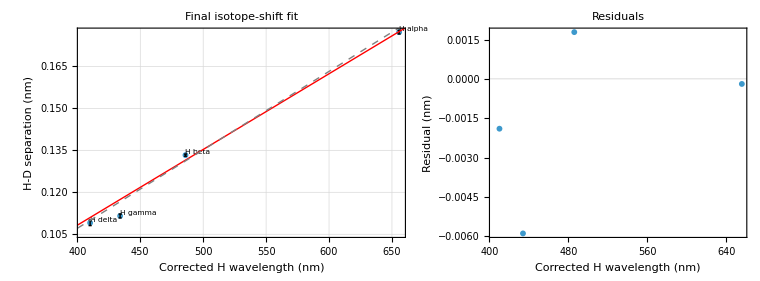

```mathematica
ClearAll["Global`*"];

(* ===============================================*)
(*Compact horizontal final isotope-shift figure*)
(* ===============================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

inputFile=FileNameJoin[{phase1Dir,"PHASE6_final_physics_fit","tables_for_latex","final_physics_input_points.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE6B_final_physics_fit_corrected"}];
figDir=FileNameJoin[{outRoot,"figures"}];

If[!DirectoryQ[outRoot],CreateDirectory[outRoot]];
If[!DirectoryQ[figDir],CreateDirectory[figDir]];

font="Arial";

toNum[x_]:=Module[{s},s=StringTrim[ToString[x]];
Quiet@Check[N@ToExpression[s],Missing["NA"]]];

raw=Import[inputFile,"CSV"];
headers=ToString/@First[raw];
records=AssociationThread[headers->#]&/@Rest[raw];

rows=records/. r_Association:><|"label"->ToString[r["label"]],"lambdaH"->toNum[r["lambdaH_corr_nm"]],"delta"->toNum[r["delta_corr_nm"]],"sigma"->toNum[r["delta_corr_SE_nm"]]|>;

rows=SortBy[rows,#["lambdaH"]&];

xvals=rows[[All,"lambdaH"]];
yvals=rows[[All,"delta"]];
sigmas=rows[[All,"sigma"]];
labels=rows[[All,"label"]];

weights=1/sigmas^2;

(*Correct zero-intercept weighted slope*)
s0=Total[weights xvals yvals]/Total[weights xvals^2];

res0=yvals-s0 xvals;

(*Free-intercept check,shown as dashed gray line*)
data=Transpose[{xvals,yvals}];

freeFit=LinearModelFit[data,{1,x},x,Weights->weights];

xMin=Min[xvals]-10;
xMax=Max[xvals]+10;

cap=0.005 (Max[xvals]-Min[xvals]);

errorBars=Graphics[Table[{Thin,Line[{{xvals[[i]],yvals[[i]]-sigmas[[i]]},{xvals[[i]],yvals[[i]]+sigmas[[i]]}}],Line[{{xvals[[i]]-cap,yvals[[i]]-sigmas[[i]]},{xvals[[i]]+cap,yvals[[i]]-sigmas[[i]]}}],Line[{{xvals[[i]]-cap,yvals[[i]]+sigmas[[i]]},{xvals[[i]]+cap,yvals[[i]]+sigmas[[i]]}}]},{i,Length[xvals]}]];

labelGraphics=Graphics[Table[Text[Style[labels[[i]],7.5,FontFamily->font],{xvals[[i]],yvals[[i]]},{-1.1,-1.2}],{i,Length[xvals]}]];

fitPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,6},ImageSize->430,AspectRatio->0.58,FrameLabel->{"Corrected H wavelength (nm)","H-D separation (nm)"},LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},PlotLabel->Style["Final isotope-shift fit",10,FontFamily->font],PlotRange->All,ImagePadding->{{48,8},{35,18}}],errorBars,labelGraphics,Plot[s0 x,{x,xMin,xMax},PlotStyle->{Red,Thick}],Plot[freeFit[x],{x,xMin,xMax},PlotStyle->{Gray,Dashed,Thick}]];

residPlot=ListPlot[Transpose[{xvals,res0}],Frame->True,Axes->False,PlotMarkers->{Automatic,6},ImageSize->330,AspectRatio->0.58,FrameLabel->{"Corrected H wavelength (nm)","Residual (nm)"},LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals",10,FontFamily->font],GridLines->{None,{0}},PlotRange->All,ImagePadding->{{48,8},{35,18}}];

horizontalFig=GraphicsRow[{fitPlot,residPlot},Spacings->0.18,ImageSize->760];

outFile=FileNameJoin[{figDir,"corrected_final_isotope_shift_fit_and_residuals_horizontal_narrow.pdf"}];

Export[outFile,horizontalFig,"PDF"];

Print["Saved horizontal figure:"];
Print[outFile];

horizontalFig

SystemOpen[figDir];
```

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*PHASE 7:Line identity map*)
(*Detect peaks and compare to H,D,and O-I alias lines*)
(* =====================================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

hOnlyDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Hydrogen_only_control"}];
actualHDDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Actual_HD_mixed_lamp"}];

calSummaryFile=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_linear_calibration_summary.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE7_line_identity_map"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"figures"}];
tableDir=FileNameJoin[{outRoot,"tables"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

(*----------helpers----------*)

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

getCalValue[rows_,key_]:=Module[{row},row=SelectFirst[rows,#[[1]]==key&];
If[MissingQ[row],Missing["NotFound"],N@ToExpression[row[[2]]]]];

makeName[s_]:=StringReplace[s,Except[LetterCharacter|DigitCharacter|"_"|"."|"-"]->"_"];

cfMarker[size_]:=Graphics[{EdgeForm[Directive[Red,AbsoluteThickness[1.2]]],Yellow,Disk[{0,0},1]},ImageSize->size];

curveFitLikeDataPlot[data_,title_]:=ListPlot[data,Frame->True,Axes->False,PlotRange->All,ImageSize->650,AspectRatio->0.52,PlotMarkers->{cfMarker[9],9},PlotStyle->Black,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.70],AbsoluteThickness[0.5]],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameLabel->{"Corrected wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[title,11,FontFamily->font]];

(*----------load calibration----------*)

calRows=Import[calSummaryFile,"CSV"];

aCal=getCalValue[calRows,"a_intercept_nm"];
bCal=getCalValue[calRows,"b_slope"];

If[!NumericQ[aCal]||!NumericQ[bCal],Print["Calibration not found, using identity calibration."];
aCal=0;
bCal=1;];

correctData[data_]:=data/. {x_,y_}:>{aCal+bCal x,y};

Print["Using calibration:"];
Print["lambda_corrected = ",aCal," + ",bCal," lambda_observed"];


(*----------candidate line list----------*)

balmerH={{"H alpha",656.279},{"H beta",486.133},{"H gamma",434.047},{"H delta",410.174},{"H epsilon",397.007},{"H zeta",388.906}};

(*approximate deuterium shifts from manual relation*)
balmerD=balmerH/. {name_,wl_}:>{StringReplace[name,"H "->"D "],wl-0.5 wl/1836};

(*first order oxygen triplet near 777 nm can look near 388.6 to 388.8 after x/2 conversion*)
oxygenFirstOrder={{"O I 777.194 first-order alias",777.194/2},{"O I 777.417 first-order alias",777.417/2},{"O I 777.539 first-order alias",777.539/2}};

candidateLines=Join[balmerH/. {name_,wl_}:><|"candidate"->name,"species"->"H","apparent_nm"->wl,"note"->"Balmer hydrogen"|>,balmerD/. {name_,wl_}:><|"candidate"->name,"species"->"D","apparent_nm"->wl,"note"->"Approx deuterium Balmer"|>,oxygenFirstOrder/. {name_,wl_}:><|"candidate"->name,"species"->"O I","apparent_nm"->wl,"note"->"First order 777 nm alias after dividing by 2"|>];

Export[FileNameJoin[{tableDir,"candidate_line_list.csv"}],Prepend[Values/@candidateLines,Keys[First[candidateLines]]],"CSV"];


(*----------peak detection----------*)

smoothList[y_,k_:3]:=MovingAverage[Join[ConstantArray[First[y],k],y,ConstantArray[Last[y],k]],2 k+1][[k+1;;-k-1]];

selectSeparatedPeaks[inds_,xvals_,yvals_,minSep_]:=Module[{sorted,kept={}},sorted=Reverse@SortBy[inds,yvals[[#]]&];
Do[If[AllTrue[kept,Abs[xvals[[idx]]-xvals[[#]]]>minSep&],AppendTo[kept,idx]],{idx,sorted}];
Sort[kept]];

quadPeakCenter[data_,i_]:=Module[{sub,fit,a,b,c,center,xmin,xmax,x},If[i<=1||i>=Length[data],Return[data[[i,1]]]];
sub=data[[i-1;;i+1]];
{xmin,xmax}=MinMax[sub[[All,1]]];
fit=Quiet@Fit[sub,{1,x,x^2},x];
c=Coefficient[fit,x,0];
b=Coefficient[fit,x,1];
a=Coefficient[fit,x,2];
If[NumericQ[a]&&a<0,center=-b/(2 a);
If[xmin<=center<=xmax,center,data[[i,1]]],data[[i,1]]]];

detectPeaks[data_,minPromFrac_:0.08,minSep_:0.045]:=Module[{xvals,yvals,ys,baseline,dyn,thresh,local,selected},xvals=data[[All,1]];
yvals=data[[All,2]];
ys=smoothList[yvals,2];
baseline=Quantile[yvals,0.10];
dyn=Max[yvals]-baseline;
thresh=baseline+minPromFrac dyn;
local=Select[Range[2,Length[ys]-1],ys[[#]]>=ys[[#-1]]&&ys[[#]]>=ys[[#+1]]&&ys[[#]]>thresh&];
selected=selectSeparatedPeaks[local,xvals,ys,minSep];
Table[<|"peak_nm"->quadPeakCenter[data,i],"nearest_sample_nm"->xvals[[i]],"signal_V"->yvals[[i]],"baseline_V"->baseline,"height_over_baseline_V"->yvals[[i]]-baseline|>,{i,selected}]];

matchPeak[peakNm_]:=Module[{best,delta,confidence},best=First@SortBy[candidateLines,Abs[#["apparent_nm"]-peakNm]&];
delta=peakNm-best["apparent_nm"];
confidence=Which[Abs[delta]<=0.035,"strong",Abs[delta]<=0.080,"possible",True,"unmatched"];
<|"matched_candidate"->best["candidate"],"matched_species"->best["species"],"candidate_nm"->best["apparent_nm"],"delta_nm"->delta,"confidence"->confidence,"note"->best["note"]|>];


(*----------plot one spectrum with candidate lines----------*)

plotIdentityMap[data_,peaks_,title_,outFile_]:=Module[{xrange,yrange,candidatesInRange,peakGraphics,candidateGraphics,basePlot},xrange=MinMax[data[[All,1]]];
yrange=MinMax[data[[All,2]]];
candidatesInRange=Select[candidateLines,xrange[[1]]-0.06<=#["apparent_nm"]<=xrange[[2]]+0.06&];
basePlot=curveFitLikeDataPlot[data,title];
candidateGraphics=Graphics[Table[{Which[c["species"]=="H",Blue,c["species"]=="D",Purple,c["species"]=="O I",Darker[Green],True,Gray],Dashed,AbsoluteThickness[1],Line[{{c["apparent_nm"],yrange[[1]]},{c["apparent_nm"],yrange[[2]]}}],Text[Style[c["candidate"],7,FontFamily->font],{c["apparent_nm"],yrange[[2]]},{0,-1.2},{0,1}]},{c,candidatesInRange}]];
peakGraphics=Graphics[Table[{Black,PointSize[0.015],Point[{p["peak_nm"],p["signal_V"]}],Text[Style[NumberForm[p["peak_nm"],{8,3}],7,FontFamily->font,Background->White],{p["peak_nm"],p["signal_V"]},{0,-1.3}]},{p,peaks}]];
Export[outFile,Show[basePlot,candidateGraphics,peakGraphics,PlotRange->All],"PDF"];];

(*----------run on files----------*)

files=Join[({"Hydrogen_only_control",#}&/@Sort@FileNames["*_REAL_FOR_CURVEFIT.dat",hOnlyDir]),({"Actual_HD_mixed_lamp",#}&/@Sort@FileNames["*_REAL_FOR_CURVEFIT.dat",actualHDDir])];

allRows=Flatten[Table[Module[{category,file,dataRaw,data,peaks,matches,rows,figOut,title,base},category=item[[1]];
file=item[[2]];
base=FileBaseName[file];
dataRaw=importNumeric[file];
data=correctData[dataRaw];
peaks=detectPeaks[data,0.08,0.045];
matches=matchPeak/@(peaks[[All,"peak_nm"]]/. Missing[_,_]->{});
rows=Table[Join[<|"category"->category,"file"->FileNameTake[file],"peak_index"->i|>,peaks[[i]],matches[[i]]],{i,Length[peaks]}];
title=category<>": "<>StringTake[base,UpTo[70]];
figOut=FileNameJoin[{figDir,makeName[category<>"_"<>base<>"_identity_map"]<>".pdf"}];
plotIdentityMap[data,peaks,title,figOut];
rows],{item,files}],1];

Export[FileNameJoin[{tableDir,"detected_peak_identity_map.csv"}],Prepend[Values/@allRows,Keys[First[allRows]]],"CSV"];

latexRows=allRows/. r_Association:>StringRiffle[{r["category"],StringTake[r["file"],UpTo[32]],r["peak_index"],NumberForm[r["peak_nm"],{8,3}],NumberForm[r["signal_V"],{8,3}],r["matched_candidate"],NumberForm[r["candidate_nm"],{8,3}],NumberForm[r["delta_nm"],{8,3}],r["confidence"]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"detected_peak_identity_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

(*----------compact suspicious region summary----------*)

suspiciousKeys={"397.765","389.035","397.413","388.945"};

suspiciousFiles=Select[files,AnyTrue[suspiciousKeys,StringContainsQ[FileNameTake[#[[2]]],#]&]&];

suspiciousPlots=Table[Module[{category,file,data,peaks,title,xrange,yrange,candidatesInRange},category=item[[1]];
file=item[[2]];
data=correctData[importNumeric[file]];
peaks=detectPeaks[data,0.08,0.045];
title=category<>"\n"<>StringTake[FileBaseName[file],UpTo[42]];
xrange=MinMax[data[[All,1]]];
yrange=MinMax[data[[All,2]]];
candidatesInRange=Select[candidateLines,xrange[[1]]-0.06<=#["apparent_nm"]<=xrange[[2]]+0.06&];
Show[curveFitLikeDataPlot[data,title],Graphics[Table[{Which[c["species"]=="H",Blue,c["species"]=="D",Purple,c["species"]=="O I",Darker[Green],True,Gray],Dashed,AbsoluteThickness[1],Line[{{c["apparent_nm"],yrange[[1]]},{c["apparent_nm"],yrange[[2]]}}]},{c,candidatesInRange}]],Graphics[Table[{Black,PointSize[0.014],Point[{p["peak_nm"],p["signal_V"]}]},{p,peaks}]],ImageSize->360]],{item,suspiciousFiles}];

summaryFig=Grid[Partition[suspiciousPlots,UpTo[2]],Spacings->{0.25,0.25}];

Export[FileNameJoin[{figDir,"suspicious_regions_identity_summary.pdf"}],summaryFig,"PDF"];

Print["DONE Phase 7 line identity map."];
Print["Outputs saved here:"];
Print[outRoot];

Print["Main table:"];
Print[FileNameJoin[{tableDir,"detected_peak_identity_map.csv"}]];

Print["Suspicious summary figure:"];
Print[FileNameJoin[{figDir,"suspicious_regions_identity_summary.pdf"}]];

Dataset[allRows]

SystemOpen[outRoot];
```

Import::nffil: File C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE2_Hg_calibration_native_clean\tables_for_latex\Hg_linear_calibration_summary.csv not found during Import.

SelectFirst::normal: Nonatomic expression expected at position 1 in SelectFirst[$Failed,#1⟦1⟧==a_intercept_nm&].

ToExpression::notstrbox: #1⟦1⟧==a_intercept_nm& is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

SelectFirst::normal: Nonatomic expression expected at position 1 in SelectFirst[$Failed,#1⟦1⟧==b_slope&].

ToExpression::notstrbox: #1⟦1⟧==b_slope& is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Calibration not found, using identity calibration.

Using calibration:

lambda_corrected = 0 + 1 lambda_observed

First::nofirst: {} has zero length and no first element.

Keys::invrl: The argument First[{}] is not a valid Association or a list of rules.

DONE Phase 7 line identity map.

Outputs saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE7_line_identity_map

Main table:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE7_line_identity_map\tables\detected_peak_identity_map.csv

Suspicious summary figure:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE7_line_identity_map\figures\suspicious_regions_identity_summary.pdf

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*PHASE 7:Line identity map*)
(*Uses current exp25 folder structure*)
(* =====================================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\exp25\\PHASE1_real_wavelength_files";

If[!DirectoryQ[phase1Dir],Print["Could not find phase1Dir:"];
Print[phase1Dir];
Abort[];];

hOnlyDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Hydrogen_only_control"}];
actualHDDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Actual_HD_mixed_lamp"}];

If[!DirectoryQ[hOnlyDir],Print["Could not find hydrogen only folder:"];
Print[hOnlyDir];
Abort[];];

If[!DirectoryQ[actualHDDir],Print["Could not find actual HD folder:"];
Print[actualHDDir];
Abort[];];

calSummaryFile=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_linear_calibration_summary.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE7_line_identity_map"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"figures"}];
tableDir=FileNameJoin[{outRoot,"tables"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

Print["Using phase1Dir:"];
Print[phase1Dir];

(*----------helpers----------*)

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

getCalValue[rows_,key_]:=Module[{row},row=SelectFirst[rows,#[[1]]==key&];
If[MissingQ[row],Missing["NotFound"],N@ToExpression[row[[2]]]]];

makeName[s_]:=StringReplace[s,Except[LetterCharacter|DigitCharacter|"_"|"."|"-"]->"_"];

cfMarker[size_]:=Graphics[{EdgeForm[Directive[Red,AbsoluteThickness[1.2]]],Yellow,Disk[{0,0},1]},ImageSize->size];

curveFitLikeDataPlot[data_,title_]:=ListPlot[data,Frame->True,Axes->False,PlotRange->All,ImageSize->560,AspectRatio->0.50,PlotMarkers->{cfMarker[8],8},PlotStyle->Black,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.72],AbsoluteThickness[0.45]],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameLabel->{"Corrected wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},PlotLabel->Style[title,9,FontFamily->font]];

(*----------calibration----------*)

If[FileExistsQ[calSummaryFile],calRows=Import[calSummaryFile,"CSV"];
aCal=getCalValue[calRows,"a_intercept_nm"];
bCal=getCalValue[calRows,"b_slope"];,Print["Calibration file not found. Using identity calibration."];
Print[calSummaryFile];
aCal=0;
bCal=1;];

If[!NumericQ[aCal]||!NumericQ[bCal],aCal=0;
bCal=1;];

correctData[data_]:=data/. {x_,y_}:>{aCal+bCal x,y};

Print["Using calibration:"];
Print["lambda_corrected = ",aCal," + ",bCal," lambda_observed"];

(*----------candidate line list----------*)

balmerH={{"H alpha",656.279},{"H beta",486.133},{"H gamma",434.047},{"H delta",410.174},{"H epsilon",397.007},{"H zeta",388.906}};

balmerD=balmerH/. {name_,wl_}:>{StringReplace[name,"H "->"D "],wl-0.5 wl/1836};

oxygenFirstOrderAlias={{"O I 777.194 first order alias",aCal+bCal (777.194/2)},{"O I 777.417 first order alias",aCal+bCal (777.417/2)},{"O I 777.539 first order alias",aCal+bCal (777.539/2)}};

candidateLines=Join[balmerH/. {name_,wl_}:><|"candidate"->name,"species"->"H","apparent_nm"->wl,"note"->"Balmer hydrogen"|>,balmerD/. {name_,wl_}:><|"candidate"->name,"species"->"D","apparent_nm"->wl,"note"->"Approx deuterium Balmer"|>,oxygenFirstOrderAlias/. {name_,wl_}:><|"candidate"->name,"species"->"O I","apparent_nm"->wl,"note"->"First order oxygen line after second order conversion"|>];

Export[FileNameJoin[{tableDir,"candidate_line_list.csv"}],Prepend[Values/@candidateLines,Keys[First[candidateLines]]],"CSV"];

(*----------peak detection----------*)

smoothList[y_,k_:2]:=Table[Mean[y[[Max[1,i-k];;Min[Length[y],i+k]]]],{i,Length[y]}];

selectSeparatedPeaks[inds_,xvals_,yvals_,minSep_]:=Module[{sorted,kept={}},sorted=Reverse@SortBy[inds,yvals[[#]]&];
Do[If[AllTrue[kept,Abs[xvals[[idx]]-xvals[[#]]]>minSep&],AppendTo[kept,idx]],{idx,sorted}];
Sort[kept]];

quadPeakCenter[data_,i_]:=Module[{sub,fit,a,b,center,xmin,xmax,x},If[i<=1||i>=Length[data],Return[data[[i,1]]]];
sub=data[[i-1;;i+1]];
{xmin,xmax}=MinMax[sub[[All,1]]];
fit=Quiet@Fit[sub,{1,x,x^2},x];
b=Coefficient[fit,x,1];
a=Coefficient[fit,x,2];
If[NumericQ[a]&&a<0,center=-b/(2 a);
If[xmin<=center<=xmax,center,data[[i,1]]],data[[i,1]]]];

detectPeaks[data_,minPromFrac_:0.06,minSep_:0.035]:=Module[{xvals,yvals,ys,baseline,dyn,thresh,local,selected},xvals=data[[All,1]];
yvals=data[[All,2]];
ys=smoothList[yvals,2];
baseline=Quantile[yvals,0.10];
dyn=Max[yvals]-baseline;
thresh=baseline+minPromFrac dyn;
If[dyn<=0,Return[{}]];
local=Select[Range[2,Length[ys]-1],ys[[#]]>=ys[[#-1]]&&ys[[#]]>=ys[[#+1]]&&ys[[#]]>thresh&];
selected=selectSeparatedPeaks[local,xvals,ys,minSep];
Table[<|"peak_nm"->quadPeakCenter[data,i],"nearest_sample_nm"->xvals[[i]],"signal_V"->yvals[[i]],"baseline_V"->baseline,"height_over_baseline_V"->yvals[[i]]-baseline|>,{i,selected}]];

matchPeak[peakNm_]:=Module[{best,delta,confidence},best=First@SortBy[candidateLines,Abs[#["apparent_nm"]-peakNm]&];
delta=peakNm-best["apparent_nm"];
confidence=Which[Abs[delta]<=0.035,"strong",Abs[delta]<=0.080,"possible",True,"unmatched"];
<|"matched_candidate"->best["candidate"],"matched_species"->best["species"],"candidate_nm"->best["apparent_nm"],"delta_nm"->delta,"confidence"->confidence,"note"->best["note"]|>];

plotIdentityMap[data_,peaks_,title_,outFile_]:=Module[{xrange,yrange,candidatesInRange,peakGraphics,candidateGraphics,basePlot},xrange=MinMax[data[[All,1]]];
yrange=MinMax[data[[All,2]]];
candidatesInRange=Select[candidateLines,xrange[[1]]-0.08<=#["apparent_nm"]<=xrange[[2]]+0.08&];
basePlot=curveFitLikeDataPlot[data,title];
candidateGraphics=Graphics[Table[{Which[c["species"]=="H",Blue,c["species"]=="D",Purple,c["species"]=="O I",Darker[Green],True,Gray],Dashed,AbsoluteThickness[1],Line[{{c["apparent_nm"],yrange[[1]]},{c["apparent_nm"],yrange[[2]]}}],Text[Style[c["candidate"],6.5,FontFamily->font,Background->White],{c["apparent_nm"],yrange[[2]]},{0,-1.2},{0,1}]},{c,candidatesInRange}]];
peakGraphics=Graphics[Table[{Black,PointSize[0.016],Point[{p["peak_nm"],p["signal_V"]}],Text[Style[NumberForm[p["peak_nm"],{8,3}],6.5,FontFamily->font,Background->White],{p["peak_nm"],p["signal_V"]},{0,-1.4}]},{p,peaks}]];
Export[outFile,Show[basePlot,candidateGraphics,peakGraphics,PlotRange->All],"PDF"];];

(*----------run on spectra----------*)

hFiles=Sort@FileNames["*_REAL_FOR_CURVEFIT.dat",hOnlyDir];
hdFiles=Sort@FileNames["*_REAL_FOR_CURVEFIT.dat",actualHDDir];

Print["Hydrogen only files found: ",Length[hFiles]];
Print["Actual HD files found: ",Length[hdFiles]];

files=Join[({"Hydrogen_only_control",#}&/@hFiles),({"Actual_HD_mixed_lamp",#}&/@hdFiles)];

allRows=Join@@Table[Module[{category,file,dataRaw,data,peaks,matches,rows,figOut,title,base},category=item[[1]];
file=item[[2]];
base=FileBaseName[file];
dataRaw=importNumeric[file];
data=correctData[dataRaw];
peaks=detectPeaks[data,0.06,0.035];
If[Length[peaks]==0,Print["No peaks detected in: ",FileNameTake[file]];
{},matches=matchPeak/@peaks[[All,"peak_nm"]];
rows=Table[Join[<|"category"->category,"file"->FileNameTake[file],"peak_index"->i|>,peaks[[i]],matches[[i]]],{i,Length[peaks]}];
title=category<>": "<>StringTake[base,UpTo[55]];
figOut=FileNameJoin[{figDir,makeName[category<>"_"<>base<>"_identity_map"]<>".pdf"}];
plotIdentityMap[data,peaks,title,figOut];
rows]],{item,files}];

If[Length[allRows]==0,Print["No rows were created. Check folder paths or peak threshold."];
Abort[];];

Export[FileNameJoin[{tableDir,"detected_peak_identity_map.csv"}],Prepend[Values/@allRows,Keys[First[allRows]]],"CSV"];

latexRows=allRows/. r_Association:>StringRiffle[{r["category"],StringTake[r["file"],UpTo[28]],r["peak_index"],NumberForm[r["peak_nm"],{8,3}],NumberForm[r["signal_V"],{8,3}],r["matched_candidate"],NumberForm[r["candidate_nm"],{8,3}],NumberForm[r["delta_nm"],{8,3}],r["confidence"]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"detected_peak_identity_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

(*----------suspicious summary----------*)

suspiciousKeys={"397.765","389.035","397.413","388.945"};

suspiciousFiles=Select[files,AnyTrue[suspiciousKeys,StringContainsQ[FileNameTake[#[[2]]],#]&]&];

suspiciousPlots=Table[Module[{category,file,data,peaks,title,xrange,yrange,candidatesInRange},category=item[[1]];
file=item[[2]];
data=correctData[importNumeric[file]];
peaks=detectPeaks[data,0.06,0.035];
title=category<>"\n"<>StringTake[FileBaseName[file],UpTo[38]];
xrange=MinMax[data[[All,1]]];
yrange=MinMax[data[[All,2]]];
candidatesInRange=Select[candidateLines,xrange[[1]]-0.08<=#["apparent_nm"]<=xrange[[2]]+0.08&];
Show[curveFitLikeDataPlot[data,title],Graphics[Table[{Which[c["species"]=="H",Blue,c["species"]=="D",Purple,c["species"]=="O I",Darker[Green],True,Gray],Dashed,AbsoluteThickness[1],Line[{{c["apparent_nm"],yrange[[1]]},{c["apparent_nm"],yrange[[2]]}}]},{c,candidatesInRange}]],Graphics[Table[{Black,PointSize[0.016],Point[{p["peak_nm"],p["signal_V"]}]},{p,peaks}]],ImageSize->360]],{item,suspiciousFiles}];

If[Length[suspiciousPlots]>0,summaryFig=Grid[Partition[suspiciousPlots,UpTo[2]],Spacings->{0.25,0.25}];
Export[FileNameJoin[{figDir,"suspicious_regions_identity_summary.pdf"}],summaryFig,"PDF"];];

Print["DONE Phase 7 line identity map."];
Print["Rows detected: ",Length[allRows]];
Print["Outputs saved here:"];
Print[outRoot];

Print["Main table:"];
Print[FileNameJoin[{tableDir,"detected_peak_identity_map.csv"}]];

Print["Suspicious summary figure:"];
Print[FileNameJoin[{figDir,"suspicious_regions_identity_summary.pdf"}]];

Dataset[allRows]

SystemOpen[outRoot];
```

Using phase1Dir:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files

Using calibration:

lambda_corrected = 0.423395 + 0.998274 lambda_observed

Hydrogen only files found: 7

Actual HD files found: 7

Export::noopen: Cannot open C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE7_line_identity_map\figures\Hydrogen_only_control_08_Hydrogen_only_control_656.695nm_HD_data_wavelength_is_1313.15_3_to_2__this_is_in_second_REAL_FOR_CURVEFIT_identity_map.pdf.

Export::noopen: Cannot open C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE7_line_identity_map\figures\Hydrogen_only_control_10_Hydrogen_only_control_389.035nm_HD_data_wavelength_is_777.637_7_to_2__this_is_in_second_REAL_FOR_CURVEFIT_identity_map.pdf.

Export::noopen: Cannot open C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE7_line_identity_map\figures\Hydrogen_only_control_11_Hydrogen_only_control_397.765nm_HD_data_wavelength_is_794.566_6_to_2__this_is_in_second_REAL_FOR_CURVEFIT_identity_map.pdf.

General::stop: Further output of Export::noopen will be suppressed during this calculation.

Part::partd: Part specification 397.765⟦2⟧ is longer than depth of object.

StringContainsQ::strse: A string or list of strings is expected at position 1 in StringContainsQ[FileNameTake[397.765⟦2⟧],397.765].

Part::partd: Part specification 389.035⟦2⟧ is longer than depth of object.

StringContainsQ::strse: A string or list of strings is expected at position 1 in StringContainsQ[FileNameTake[389.035⟦2⟧],389.035].

Part::partd: Part specification 397.413⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringContainsQ::strse: A string or list of strings is expected at position 1 in StringContainsQ[FileNameTake[397.413⟦2⟧],397.413].

General::stop: Further output of StringContainsQ::strse will be suppressed during this calculation.

DONE Phase 7 line identity map.

Rows detected: 27

Outputs saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE7_line_identity_map

Main table:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE7_line_identity_map\tables\detected_peak_identity_map.csv

Suspicious summary figure:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE7_line_identity_map\figures\suspicious_regions_identity_summary.pdf

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*PHASE 7:Line identity map,corrected short-name code*)
(* =====================================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\exp25\\PHASE1_real_wavelength_files";

If[!DirectoryQ[phase1Dir],Print["Could not find phase1Dir:"];
Print[phase1Dir];
Abort[];];

hOnlyDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Hydrogen_only_control"}];
actualHDDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Actual_HD_mixed_lamp"}];

If[!DirectoryQ[hOnlyDir],Print["Could not find hydrogen only folder:"];
Print[hOnlyDir];
Abort[];];

If[!DirectoryQ[actualHDDir],Print["Could not find actual HD folder:"];
Print[actualHDDir];
Abort[];];

calSummaryFile=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_linear_calibration_summary.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE7_line_identity_map"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"figures"}];
tableDir=FileNameJoin[{outRoot,"tables"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

Print["Using phase1Dir:"];
Print[phase1Dir];

(*----------helpers----------*)

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

getCalValue[rows_,key_]:=Module[{row},row=SelectFirst[rows,#[[1]]==key&];
If[MissingQ[row],Missing["NotFound"],N@ToExpression[row[[2]]]]];

shortFileName[i_,category_]:="identity_"<>IntegerString[i,10,3]<>"_"<>category<>".pdf";

cfMarker[size_]:=Graphics[{EdgeForm[Directive[Red,AbsoluteThickness[1.2]]],Yellow,Disk[{0,0},1]},ImageSize->size];

curveFitLikeDataPlot[data_,title_]:=ListPlot[data,Frame->True,Axes->False,PlotRange->All,ImageSize->560,AspectRatio->0.50,PlotMarkers->{cfMarker[8],8},PlotStyle->Black,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.72],AbsoluteThickness[0.45]],FrameStyle->Directive[Black,AbsoluteThickness[1]],FrameLabel->{"Corrected wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},PlotLabel->Style[title,9,FontFamily->font]];

(*----------calibration----------*)

If[FileExistsQ[calSummaryFile],calRows=Import[calSummaryFile,"CSV"];
aCal=getCalValue[calRows,"a_intercept_nm"];
bCal=getCalValue[calRows,"b_slope"];,Print["Calibration file not found. Using identity calibration."];
Print[calSummaryFile];
aCal=0;
bCal=1;];

If[!NumericQ[aCal]||!NumericQ[bCal],aCal=0;
bCal=1;];

correctData[data_]:=data/. {x_,y_}:>{aCal+bCal x,y};

Print["Using calibration:"];
Print["lambda_corrected = ",aCal," + ",bCal," lambda_observed"];

(*----------candidate line list----------*)

balmerH={{"H alpha",656.279},{"H beta",486.133},{"H gamma",434.047},{"H delta",410.174},{"H epsilon",397.007},{"H zeta",388.906}};

balmerD=balmerH/. {name_,wl_}:>{StringReplace[name,"H "->"D "],wl-0.5 wl/1836};

oxygenFirstOrderAlias={{"O I 777.194 first order alias",aCal+bCal (777.194/2)},{"O I 777.417 first order alias",aCal+bCal (777.417/2)},{"O I 777.539 first order alias",aCal+bCal (777.539/2)}};

candidateLines=Join[balmerH/. {name_,wl_}:><|"candidate"->name,"species"->"H","apparent_nm"->wl,"note"->"Balmer hydrogen"|>,balmerD/. {name_,wl_}:><|"candidate"->name,"species"->"D","apparent_nm"->wl,"note"->"Approx deuterium Balmer"|>,oxygenFirstOrderAlias/. {name_,wl_}:><|"candidate"->name,"species"->"O I","apparent_nm"->wl,"note"->"First order oxygen line after second order conversion"|>];

Export[FileNameJoin[{tableDir,"candidate_line_list.csv"}],Prepend[Values/@candidateLines,Keys[First[candidateLines]]],"CSV"];

(*----------peak detection----------*)

smoothList[y_,k_:2]:=Table[Mean[y[[Max[1,i-k];;Min[Length[y],i+k]]]],{i,Length[y]}];

selectSeparatedPeaks[inds_,xvals_,yvals_,minSep_]:=Module[{sorted,kept={}},sorted=Reverse@SortBy[inds,yvals[[#]]&];
Do[If[AllTrue[kept,Abs[xvals[[idx]]-xvals[[#]]]>minSep&],AppendTo[kept,idx]],{idx,sorted}];
Sort[kept]];

quadPeakCenter[data_,i_]:=Module[{sub,fit,a,b,center,xmin,xmax,x},If[i<=1||i>=Length[data],Return[data[[i,1]]]];
sub=data[[i-1;;i+1]];
{xmin,xmax}=MinMax[sub[[All,1]]];
fit=Quiet@Fit[sub,{1,x,x^2},x];
b=Coefficient[fit,x,1];
a=Coefficient[fit,x,2];
If[NumericQ[a]&&a<0,center=-b/(2 a);
If[xmin<=center<=xmax,center,data[[i,1]]],data[[i,1]]]];

detectPeaks[data_,minPromFrac_:0.06,minSep_:0.035]:=Module[{xvals,yvals,ys,baseline,dyn,thresh,local,selected},xvals=data[[All,1]];
yvals=data[[All,2]];
ys=smoothList[yvals,2];
baseline=Quantile[yvals,0.10];
dyn=Max[yvals]-baseline;
thresh=baseline+minPromFrac dyn;
If[dyn<=0,Return[{}]];
local=Select[Range[2,Length[ys]-1],ys[[#]]>=ys[[#-1]]&&ys[[#]]>=ys[[#+1]]&&ys[[#]]>thresh&];
selected=selectSeparatedPeaks[local,xvals,ys,minSep];
Table[<|"peak_nm"->quadPeakCenter[data,i],"nearest_sample_nm"->xvals[[i]],"signal_V"->yvals[[i]],"baseline_V"->baseline,"height_over_baseline_V"->yvals[[i]]-baseline|>,{i,selected}]];

matchPeak[peakNm_]:=Module[{best,delta,confidence},best=First@SortBy[candidateLines,Abs[#["apparent_nm"]-peakNm]&];
delta=peakNm-best["apparent_nm"];
confidence=Which[Abs[delta]<=0.035,"strong",Abs[delta]<=0.080,"possible",True,"unmatched"];
<|"matched_candidate"->best["candidate"],"matched_species"->best["species"],"candidate_nm"->best["apparent_nm"],"delta_nm"->delta,"confidence"->confidence,"note"->best["note"]|>];

plotIdentityMap[data_,peaks_,title_,outFile_]:=Module[{xrange,yrange,candidatesInRange,peakGraphics,candidateGraphics,basePlot},xrange=MinMax[data[[All,1]]];
yrange=MinMax[data[[All,2]]];
candidatesInRange=Select[candidateLines,xrange[[1]]-0.08<=#["apparent_nm"]<=xrange[[2]]+0.08&];
basePlot=curveFitLikeDataPlot[data,title];
candidateGraphics=Graphics[Table[{Which[c["species"]=="H",Blue,c["species"]=="D",Purple,c["species"]=="O I",Darker[Green],True,Gray],Dashed,AbsoluteThickness[1],Line[{{c["apparent_nm"],yrange[[1]]},{c["apparent_nm"],yrange[[2]]}}],Text[Style[c["candidate"],6.5,FontFamily->font,Background->White],{c["apparent_nm"],yrange[[2]]},{0,-1.2},{0,1}]},{c,candidatesInRange}]];
peakGraphics=Graphics[Table[{Black,PointSize[0.016],Point[{p["peak_nm"],p["signal_V"]}],Text[Style[NumberForm[p["peak_nm"],{8,3}],6.5,FontFamily->font,Background->White],{p["peak_nm"],p["signal_V"]},{0,-1.4}]},{p,peaks}]];
Export[outFile,Show[basePlot,candidateGraphics,peakGraphics,PlotRange->All],"PDF"];];

(*----------run on spectra----------*)

hFiles=Sort@FileNames["*_REAL_FOR_CURVEFIT.dat",hOnlyDir];
hdFiles=Sort@FileNames["*_REAL_FOR_CURVEFIT.dat",actualHDDir];

Print["Hydrogen only files found: ",Length[hFiles]];
Print["Actual HD files found: ",Length[hdFiles]];

files=Join[({"Hydrogen_only_control",#}&/@hFiles),({"Actual_HD_mixed_lamp",#}&/@hdFiles)];

rowGroups=Table[Module[{category,file,dataRaw,data,peaks,matches,rows,figOut,title,base},category=item[[1]];
file=item[[2]];
base=FileBaseName[file];
dataRaw=importNumeric[file];
data=correctData[dataRaw];
peaks=detectPeaks[data,0.06,0.035];
If[Length[peaks]==0,Print["No peaks detected in: ",FileNameTake[file]];
{},matches=matchPeak/@peaks[[All,"peak_nm"]];
rows=Table[Join[<|"category"->category,"file"->FileNameTake[file],"short_plot_file"->shortFileName[i,category],"peak_index"->j|>,peaks[[j]],matches[[j]]],{j,Length[peaks]}];
title=category<>": "<>StringTake[base,UpTo[45]];
figOut=FileNameJoin[{figDir,shortFileName[i,category]}];
plotIdentityMap[data,peaks,title,figOut];
rows]],{i,Length[files]},{item,{files[[i]]}}];

allRows=Flatten[rowGroups,2];

If[Length[allRows]==0,Print["No rows were created. Check folder paths or peak threshold."];
Abort[];];

Export[FileNameJoin[{tableDir,"detected_peak_identity_map.csv"}],Prepend[Values/@allRows,Keys[First[allRows]]],"CSV"];

latexRows=allRows/. r_Association:>StringRiffle[{r["category"],StringTake[r["file"],UpTo[28]],r["peak_index"],NumberForm[r["peak_nm"],{8,3}],NumberForm[r["signal_V"],{8,3}],r["matched_candidate"],NumberForm[r["candidate_nm"],{8,3}],NumberForm[r["delta_nm"],{8,3}],r["confidence"]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"detected_peak_identity_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

(*----------suspicious summary----------*)

suspiciousKeys={"397.765","389.035","397.413","388.945"};

suspiciousFiles=Select[files,Function[item,AnyTrue[suspiciousKeys,Function[key,StringContainsQ[FileNameTake[item[[2]]],key]]]]];

suspiciousPlots=Table[Module[{category,file,data,peaks,title,xrange,yrange,candidatesInRange},category=item[[1]];
file=item[[2]];
data=correctData[importNumeric[file]];
peaks=detectPeaks[data,0.06,0.035];
title=category<>"\n"<>StringTake[FileBaseName[file],UpTo[38]];
xrange=MinMax[data[[All,1]]];
yrange=MinMax[data[[All,2]]];
candidatesInRange=Select[candidateLines,xrange[[1]]-0.08<=#["apparent_nm"]<=xrange[[2]]+0.08&];
Show[curveFitLikeDataPlot[data,title],Graphics[Table[{Which[c["species"]=="H",Blue,c["species"]=="D",Purple,c["species"]=="O I",Darker[Green],True,Gray],Dashed,AbsoluteThickness[1],Line[{{c["apparent_nm"],yrange[[1]]},{c["apparent_nm"],yrange[[2]]}}]},{c,candidatesInRange}]],Graphics[Table[{Black,PointSize[0.016],Point[{p["peak_nm"],p["signal_V"]}]},{p,peaks}]],ImageSize->360]],{item,suspiciousFiles}];

If[Length[suspiciousPlots]>0,summaryFig=Grid[Partition[suspiciousPlots,UpTo[2]],Spacings->{0.25,0.25}];
Export[FileNameJoin[{figDir,"suspicious_regions_identity_summary.pdf"}],summaryFig,"PDF"];];

Print["DONE Phase 7 line identity map."];
Print["Rows detected: ",Length[allRows]];
Print["Outputs saved here:"];
Print[outRoot];

Print["Main table:"];
Print[FileNameJoin[{tableDir,"detected_peak_identity_map.csv"}]];

Print["Suspicious summary figure:"];
Print[FileNameJoin[{figDir,"suspicious_regions_identity_summary.pdf"}]];

Dataset[allRows]

SystemOpen[outRoot];
```

Using phase1Dir:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files

Using calibration:

lambda_corrected = 0.423395 + 0.998274 lambda_observed

Hydrogen only files found: 7

Actual HD files found: 7

DONE Phase 7 line identity map.

Rows detected: 27

Outputs saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE7_line_identity_map

Main table:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE7_line_identity_map\tables\detected_peak_identity_map.csv

Suspicious summary figure:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE7_line_identity_map\figures\suspicious_regions_identity_summary.pdf

SetOptions::optnf: IntervalMarkers is not a known option for ParametricPlot.

Saved figures:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE8_curvefit_representative_figures\CurveFit_clean_HD_beta_gamma.pdf

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE8_curvefit_representative_figures\CurveFit_main_HD_centers_2x2.pdf

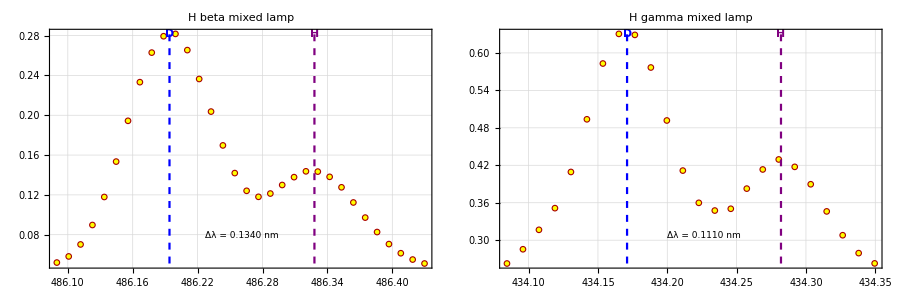
Representative clean hydrogen deuterium doublets
-Graphics-
Blue dashed line marks fitted deuterium center. Purple dashed line marks fitted hydrogen center.

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*CurveFit generated representative H/D figures*)
(*Uses actual CurveFit LinearDataPlot[]*)
(* =====================================================*)

curveFitDir="C:\\Users\\ansht\\Desktop\\package\\CurveFit";
Get[FileNameJoin[{curveFitDir,"CurveFit.m"}]];

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\exp25\\PHASE1_real_wavelength_files";

actualHDDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Actual_HD_mixed_lamp"}];

fastFitCSV=FileNameJoin[{phase1Dir,"PHASE5C_actual_HD_fast_bounded_refit","tables_for_latex","fast_bounded_actual_HD_fit_results.csv"}];

alphaLocalCSV=FileNameJoin[{phase1Dir,"PHASE5D_H_alpha_local_refit","H_alpha_local_refit_results.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE8_curvefit_representative_figures"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

font="Arial";

(*----------helpers----------*)

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",actualHDDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

toNum[x_]:=Quiet@Check[N@ToExpression[ToString[x]],Missing["NA"]];

(*----------load fit centers----------*)

fastRaw=Import[fastFitCSV,"CSV"];
fastHeaders=ToString/@First[fastRaw];
fastRecords=AssociationThread[fastHeaders->#]&/@Rest[fastRaw];

getFastRow[label_]:=SelectFirst[fastRecords,StringTrim[ToString[#["label"]]]==label&];

alphaRaw=Import[alphaLocalCSV,"CSV"];
alphaAssoc=AssociationThread[alphaRaw[[All,1]]->alphaRaw[[All,2]]];

fitCenters=<|"H alpha"-><|"muD"->toNum[alphaAssoc["muD_obs_nm"]],"muH"->toNum[alphaAssoc["muH_obs_nm"]]|>,"H beta"->Module[{r=getFastRow["H beta"]},<|"muD"->toNum[r["muD_obs_nm"]],"muH"->toNum[r["muH_obs_nm"]]|>],"H gamma"->Module[{r=getFastRow["H gamma"]},<|"muD"->toNum[r["muD_obs_nm"]],"muH"->toNum[r["muH_obs_nm"]]|>],"H delta"->Module[{r=getFastRow["H delta"]},<|"muD"->toNum[r["muD_obs_nm"]],"muH"->toNum[r["muH_obs_nm"]]|>]|>;

(*----------CurveFit plot panel----------*)

curveFitPanel[label_,fileKey_,window_,size_:420]:=Module[{file,data,yrange,plot,muD,muH,yTop,yBot,overlay,title},file=findFile[fileKey];
If[MissingQ[file],Print["Missing file for ",label];
Return[Graphics[Text["Missing file: "<>label]]]];
data=cropData[importNumeric[file],window];
If[Length[data]<5,Print["Too few points for ",label];
Return[Graphics[Text["Too few points: "<>label]]]];
n=Length[data];
xx=data[[All,1]];
yy=data[[All,2]];
sx=ConstantArray[0.,n];
sy=ConstantArray[0.,n];
yrange=MinMax[data[[All,2]]];
yBot=yrange[[1]];
yTop=yrange[[2]];
muD=fitCenters[label]["muD"];
muH=fitCenters[label]["muH"];
title=label<>" mixed lamp";
plot=Quiet[LinearDataPlot[],{SetOptions::optnf}];
overlay=Graphics[{Blue,Dashed,AbsoluteThickness[1.6],Line[{{muD,yBot},{muD,yTop}}],Purple,Dashed,AbsoluteThickness[1.6],Line[{{muH,yBot},{muH,yTop}}],Blue,Text[Style["D",11,Bold,FontFamily->font,Background->White],{muD,yTop},{0,-1.3}],Purple,Text[Style["H",11,Bold,FontFamily->font,Background->White],{muH,yTop},{0,-1.3}],Black,Text[Style["Δλ = "<>ToString[NumberForm[muH-muD,{5,4}]]<>" nm",9,FontFamily->font,Background->White],{Mean[{muD,muH}],yBot+0.12 (yTop-yBot)}]}];
Show[plot,overlay,PlotRange->All,ImageSize->size,PlotLabel->Style[title,13,FontFamily->font],BaseStyle->{FontFamily->font}]];

(*----------make clean representative figure----------*)

betaPanel=curveFitPanel["H beta","486.320",{486.08,486.43},430];

gammaPanel=curveFitPanel["H gamma","434.373",{434.08,434.36},430];

cleanFig=Column[{Style["Representative clean hydrogen deuterium doublets",16,Bold,FontFamily->font],GraphicsRow[{betaPanel,gammaPanel},Spacings->0.25,ImageSize->900],Style["Blue dashed line marks fitted deuterium center. Purple dashed line marks fitted hydrogen center.",10,FontFamily->font]},Alignment->Center,Spacings->0.4];

cleanOut=FileNameJoin[{outRoot,"CurveFit_clean_HD_beta_gamma.pdf"}];

Export[cleanOut,cleanFig,"PDF"];

(*----------make main centers 2 by 2 figure----------*)

alphaPanel=curveFitPanel["H alpha","656.495",{656.18,656.50},390];

betaPanelSmall=curveFitPanel["H beta","486.320",{486.08,486.43},390];

gammaPanelSmall=curveFitPanel["H gamma","434.373",{434.08,434.36},390];

deltaPanel=curveFitPanel["H delta","410.500",{410.25,410.54},390];

mainFig=Column[{Style["Fitted hydrogen deuterium centers used in the main analysis",16,Bold,FontFamily->font],Grid[{{alphaPanel,betaPanelSmall},{gammaPanelSmall,deltaPanel}},Spacings->{0.35,0.35},Alignment->Center],Style["",10,FontFamily->font]},Alignment->Center,Spacings->0.4];

mainOut=FileNameJoin[{outRoot,"CurveFit_main_HD_centers_2x2.pdf"}];

Export[mainOut,mainFig,"PDF"];

Print["Saved figures:"];
Print[cleanOut];
Print[mainOut];

SystemOpen[outRoot];

cleanFig
```

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*PHASE 8:Empirical instrument response model*)
(*Uses Hg 546 nm line shape as measured response R*)
(*Fits H/D doublets using R instead of Gaussian peaks*)
(* =====================================================*)

curveFitDir="C:\\Users\\ansht\\Desktop\\package\\CurveFit";
Get[FileNameJoin[{curveFitDir,"CurveFit.m"}]];

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\exp25\\PHASE1_real_wavelength_files";

hgDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Hg_calibration"}];
actualHDDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Actual_HD_mixed_lamp"}];

hgFitCSV=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_native_peak_fit_results.csv"}];

calSummaryFile=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_linear_calibration_summary.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE8_empirical_response_model"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"figures"}];
tableDir=FileNameJoin[{outRoot,"tables"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

(*----------helpers----------*)

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[dir_,key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",dir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

toNum[x_]:=Quiet@Check[N@ToExpression[ToString[x]],Missing["NA"]];

getCSVRecord[file_,keyName_,keyValue_]:=Module[{raw,headers,records},raw=Import[file,"CSV"];
headers=ToString/@First[raw];
records=AssociationThread[headers->#]&/@Rest[raw];
SelectFirst[records,StringContainsQ[ToString[#[keyName]],keyValue]&]];

getCalValue[rows_,key_]:=Module[{row},row=SelectFirst[rows,#[[1]]==key&];
If[MissingQ[row],Missing["NotFound"],N@ToExpression[row[[2]]]]];

bound[lo_,hi_,z_]:=(lo+hi)/2+(hi-lo)/2 Tanh[z];

invBound[lo_,hi_,val_]:=Module[{u},u=(2 val-lo-hi)/(hi-lo);
ArcTanh[Clip[u,{-0.95,0.95}]]];

ampNear[data_,muGuess_,base_,width_]:=Module[{near},near=Select[data,Abs[#[[1]]-muGuess]<=width&];
If[Length[near]==0,Max[data[[All,2]]]-base,Max[near[[All,2]]]-base]];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_"}];

cfMarker[size_]:=Graphics[{EdgeForm[Directive[Red,AbsoluteThickness[1.2]]],Yellow,Disk[{0,0},1]},ImageSize->size];

curveFitBasePlot[data_,title_,size_:450]:=Module[{plot},n=Length[data];
xx=data[[All,1]];
yy=data[[All,2]];
sx=ConstantArray[0.,n];
sy=ConstantArray[0.,n];
plot=Quiet[LinearDataPlot[],{SetOptions::optnf}];
Show[plot,ImageSize->size,PlotLabel->Style[title,12,FontFamily->font],BaseStyle->{FontFamily->font}]];

(*----------load calibration----------*)

calRows=Import[calSummaryFile,"CSV"];

aCal=getCalValue[calRows,"a_intercept_nm"];
bCal=getCalValue[calRows,"b_slope"];
sigmaB=getCalValue[calRows,"sigma_b"];

If[!NumericQ[aCal]||!NumericQ[bCal],aCal=0;
bCal=1;
sigmaB=0;];

Print["Using calibration:"];
Print["lambda_corrected = ",aCal," + ",bCal," lambda_observed"];

(*----------build empirical response from Hg 546----------*)

hgFile=findFile[hgDir,"546.226"];

If[MissingQ[hgFile],Print["Could not find Hg 546 file."];
Abort[];];

hgRec=getCSVRecord[hgFitCSV,"id","Hg 546.226"];
hgMu=toNum[hgRec["mu_obs_nm"]];

If[!NumericQ[hgMu],Print["Could not read Hg mu from table, using max point."];
hgDataTemp=importNumeric[hgFile];
hgMu=hgDataTemp[[First@Ordering[hgDataTemp[[All,2]],-1],1]];];

hgDataFull=importNumeric[hgFile];
hgWindow={hgMu-0.23,hgMu+0.23};
hgData=cropData[hgDataFull,hgWindow];

edgeN=Min[5,Floor[Length[hgData]/3]];
edgeData=Join[Take[hgData,edgeN],Take[hgData,-edgeN]];

baseFit=LinearModelFit[edgeData,{1,x},x];

respRaw=({#[[1]]-hgMu,Max[0,#[[2]]-baseFit[#[[1]]]]}&/@hgData);

maxResp=Max[respRaw[[All,2]]];

respData=SortBy[DeleteDuplicatesBy[respRaw/. {u_,y_}:>{u,y/maxResp},First],First];

{uMin,uMax}=MinMax[respData[[All,1]]];

respInterp=Interpolation[respData,InterpolationOrder->2];

response[z_]:=Piecewise[{{respInterp[z],uMin<=z<=uMax}},0];

responseFig=Show[ListPlot[respData,Frame->True,Axes->False,PlotMarkers->{Automatic,5},ImageSize->450,FrameLabel->{"Offset from Hg center (nm)","Normalized response"},PlotLabel->Style["Empirical response from Hg 546 nm",12,FontFamily->font],LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font}],Plot[response[u],{u,uMin,uMax},PlotStyle->{Red,Thick}]];

Export[FileNameJoin[{figDir,"empirical_Hg_546_response_template.pdf"}],responseFig,"PDF"];

Export[FileNameJoin[{tableDir,"empirical_Hg_546_response_template.csv"}],Prepend[respData,{"offset_nm","normalized_response"}],"CSV"];

Print["Hg response built from:"];
Print[FileNameTake[hgFile]];
Print["Hg response center = ",hgMu];

(*----------H/D specs----------*)

hdSpecs={<|"label"->"H alpha","fileKey"->"656.495","window"->{656.18,656.50},"muDGuess"->656.22,"muHGuess"->656.40,"muDRange"->{656.18,656.26},"sepRange"->{0.13,0.22},"scaleRange"->{0.35,1.30}|>,<|"label"->"H beta","fileKey"->"486.320","window"->{486.08,486.43},"muDGuess"->486.19,"muHGuess"->486.33,"muDRange"->{486.15,486.23},"sepRange"->{0.09,0.18},"scaleRange"->{0.40,1.60}|>,<|"label"->"H gamma","fileKey"->"434.373","window"->{434.08,434.36},"muDGuess"->434.17,"muHGuess"->434.28,"muDRange"->{434.13,434.21},"sepRange"->{0.08,0.16},"scaleRange"->{0.40,1.60}|>,<|"label"->"H delta","fileKey"->"410.500","window"->{410.25,410.54},"muDGuess"->410.30,"muHGuess"->410.41,"muDRange"->{410.26,410.34},"sepRange"->{0.07,0.16},"scaleRange"->{0.40,1.80}|>};

fitOneEmpirical[spec_]:=Module[{file,dataFull,data,xvals,yvals,xmin,xmax,npts,x0,edgeN2,c0,d0,ampD0,ampH0,sepGuess,scaleGuess,x,c,d,aD,aH,zD,zSep,zScale,muDExpr,sepExpr,muHExpr,scaleExpr,model,fit,params,cov,rawNames,r,rss,rms,maxres,muDVal,muHVal,sepVal,scaleVal,ampDVal,ampHVal,lambdaDcorr,lambdaHcorr,deltaCorr,baseLine,dComp,hComp,basePlot,totalPlot,residPlot,outFile},file=findFile[actualHDDir,spec["fileKey"]];
If[MissingQ[file],Print["Missing file for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"file_missing"|>]];
dataFull=importNumeric[file];
data=cropData[dataFull,spec["window"]];
If[Length[data]<8,Print["Too few points for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"too_few_points"|>]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
npts=Length[data];
x0=Mean[{xmin,xmax}];
edgeN2=Min[5,Length[yvals]];
c0=Median[Join[Take[yvals,edgeN2],Take[yvals,-edgeN2]]];
d0=0;
sepGuess=spec["muHGuess"]-spec["muDGuess"];
scaleGuess=1.0;
ampD0=Max[0.001,ampNear[data,spec["muDGuess"],c0,0.05]];
ampH0=Max[0.001,ampNear[data,spec["muHGuess"],c0,0.05]];
Print["Fitting empirical response model: ",spec["label"]];
muDExpr=bound[spec["muDRange"][[1]],spec["muDRange"][[2]],zD];
sepExpr=bound[spec["sepRange"][[1]],spec["sepRange"][[2]],zSep];
muHExpr=muDExpr+sepExpr;
scaleExpr=bound[spec["scaleRange"][[1]],spec["scaleRange"][[2]],zScale];
model=c+d (x-x0)+aD^2 response[(x-muDExpr)/scaleExpr]+aH^2 response[(x-muHExpr)/scaleExpr];
fit=TimeConstrained[Quiet@NonlinearModelFit[data,model,{{c,c0},{d,d0},{aD,Sqrt[ampD0]},{zD,invBound[spec["muDRange"][[1]],spec["muDRange"][[2]],spec["muDGuess"]]},{aH,Sqrt[ampH0]},{zSep,invBound[spec["sepRange"][[1]],spec["sepRange"][[2]],sepGuess]},{zScale,invBound[spec["scaleRange"][[1]],spec["scaleRange"][[2]],scaleGuess]}},x,MaxIterations->5000],45,$Failed];
If[fit===$Failed,Print["Fit failed or timed out for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"timeout"|>]];
params=fit["BestFitParameters"];
r=data/. {xx_,yy_}:>yy-fit[xx];
rss=Total[r^2];
rms=Sqrt[rss/npts];
maxres=Max[Abs[r]];
muDVal=muDExpr/. params;
sepVal=sepExpr/. params;
muHVal=muDVal+sepVal;
scaleVal=scaleExpr/. params;
ampDVal=aD^2/. params;
ampHVal=aH^2/. params;
lambdaDcorr=aCal+bCal muDVal;
lambdaHcorr=aCal+bCal muHVal;
deltaCorr=bCal sepVal;
baseLine[x_]=Evaluate[c+d (x-x0)/. params];
dComp[x_]=Evaluate[baseLine[x]+aD^2 response[(x-muDExpr)/scaleExpr]/. params];
hComp[x_]=Evaluate[baseLine[x]+aH^2 response[(x-muHExpr)/scaleExpr]/. params];
basePlot=curveFitBasePlot[data,spec["label"]<>": empirical response H/D fit",470];
totalPlot=Show[basePlot,Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}],Plot[{dComp[x],hComp[x]},{x,xmin,xmax},PlotStyle->{{Blue,Dashed,Thick},{Purple,Dashed,Thick}}],Graphics[{Blue,Dashed,Line[{{muDVal,Min[yvals]},{muDVal,Max[yvals]}}],Purple,Dashed,Line[{{muHVal,Min[yvals]},{muHVal,Max[yvals]}}],Black,Text[Style["Δλ = "<>ToString[NumberForm[sepVal,{6,5}]]<>" nm",9,FontFamily->font,Background->White],{Mean[{muDVal,muHVal}],Min[yvals]+0.12 (Max[yvals]-Min[yvals])}]}],PlotRange->All];
residPlot=ListPlot[Transpose[{xvals,r}],Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->470,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals",11,FontFamily->font],GridLines->{None,{0}}];
outFile=FileNameJoin[{figDir,makeName[spec["label"]]<>"_empirical_response_fit.pdf"}];
Export[outFile,GraphicsColumn[{totalPlot,residPlot},Spacings->0.15,ImageSize->490],"PDF"];
<|"label"->spec["label"],"status"->"fit_complete","file"->FileNameTake[file],"muD_obs_nm"->muDVal,"muH_obs_nm"->muHVal,"delta_obs_nm"->sepVal,"scale_factor"->scaleVal,"ampD"->ampDVal,"ampH"->ampHVal,"lambdaD_corr_nm"->lambdaDcorr,"lambdaH_corr_nm"->lambdaHcorr,"delta_corr_nm"->deltaCorr,"RMS_residual"->rms,"max_abs_residual"->maxres,"figure_pdf"->outFile|>];

results=fitOneEmpirical/@hdSpecs;

Export[FileNameJoin[{tableDir,"empirical_response_HD_fit_results.csv"}],Prepend[Values/@results,Keys[First[results]]],"CSV"];

latexRows=Select[results,#["status"]=="fit_complete"&]/. r_Association:>StringRiffle[{r["label"],NumberForm[r["muD_obs_nm"],{8,4}],NumberForm[r["muH_obs_nm"],{8,4}],NumberForm[r["delta_obs_nm"],{8,5}],NumberForm[r["lambdaH_corr_nm"],{8,4}],NumberForm[r["delta_corr_nm"],{8,5}],NumberForm[r["scale_factor"],{8,3}],NumberForm[r["RMS_residual"],{8,4}]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"empirical_response_HD_fit_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

goodRows=Select[results,#["status"]=="fit_complete"&&NumericQ[#["lambdaH_corr_nm"]]&&NumericQ[#["delta_corr_nm"]]&];

sepData=({#["lambdaH_corr_nm"],#["delta_corr_nm"]}&/@goodRows);

If[Length[sepData]>=2,sEmp=Total[sepData[[All,1]] sepData[[All,2]]]/Total[sepData[[All,1]]^2];
mpmeEmp=0.500/sEmp;
fitFig=Show[ListPlot[sepData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->440,FrameLabel->{"Corrected H wavelength (nm)","Corrected H-D separation (nm)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Empirical response isotope-shift check",11,FontFamily->font]],Plot[sEmp x,{x,Min[sepData[[All,1]]]-10,Max[sepData[[All,1]]]+10},PlotStyle->{Red,Thick}]];
Export[FileNameJoin[{figDir,"empirical_response_final_shift_check.pdf"}],fitFig,"PDF"];
Export[FileNameJoin[{tableDir,"empirical_response_final_ratio_check.csv"}],{{"quantity","value"},{"slope_zero_intercept",sEmp},{"mp_over_me",mpmeEmp}},"CSV"];
Print["Empirical response ratio check:"];
Print["s = ",sEmp];
Print["m_p/m_e = ",mpmeEmp];];

Print["DONE Phase 8 empirical response model."];
Print["Outputs saved here:"];
Print[outRoot];

Print["Check these first:"];
Print[FileNameJoin[{figDir,"empirical_Hg_546_response_template.pdf"}]];
Print[FileNameJoin[{tableDir,"empirical_response_HD_fit_results.csv"}]];

Dataset[results]

SystemOpen[outRoot];
```

SetOptions::optnf: IntervalMarkers is not a known option for ParametricPlot.

Using calibration:

lambda_corrected = 0.423395 + 0.998274 lambda_observed

Hg response built from:

06_Hg_calibration_546.475nm_546.226_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.dat

Hg response center = 546.708

Fitting empirical response model: H alpha

Fitting empirical response model: H beta

Fitting empirical response model: H gamma

Fitting empirical response model: H delta

Empirical response ratio check:

s = 0.000290638

m_p/m_e = 1720.35

DONE Phase 8 empirical response model.

Outputs saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE8_empirical_response_model

Check these first:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE8_empirical_response_model\figures\empirical_Hg_546_response_template.pdf

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE8_empirical_response_model\tables\empirical_response_HD_fit_results.csv

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*PHASE 8 CLEAN REPORT FIGURES*)
(*Clean empirical response figures using CurveFit plots*)
(* =====================================================*)

curveFitDir="C:\\Users\\ansht\\Desktop\\package\\CurveFit";
Get[FileNameJoin[{curveFitDir,"CurveFit.m"}]];

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\exp25\\PHASE1_real_wavelength_files";

hgDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Hg_calibration"}];

actualHDDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Actual_HD_mixed_lamp"}];

hgFitCSV=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_native_peak_fit_results.csv"}];

calSummaryFile=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_linear_calibration_summary.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE8_clean_report_empirical_response"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"figures"}];
tableDir=FileNameJoin[{outRoot,"tables"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

(*----------helpers----------*)

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[dir_,key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",dir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

toNum[x_]:=Quiet@Check[N@ToExpression[ToString[x]],Missing["NA"]];

getCSVRecord[file_,keyName_,keyValue_]:=Module[{raw,headers,records},raw=Import[file,"CSV"];
headers=ToString/@First[raw];
records=AssociationThread[headers->#]&/@Rest[raw];
SelectFirst[records,StringContainsQ[ToString[#[keyName]],keyValue]&]];

getCalValue[rows_,key_]:=Module[{row},row=SelectFirst[rows,#[[1]]==key&];
If[MissingQ[row],Missing["NotFound"],N@ToExpression[row[[2]]]]];

bound[lo_,hi_,z_]:=(lo+hi)/2+(hi-lo)/2 Tanh[z];

invBound[lo_,hi_,val_]:=Module[{u},u=(2 val-lo-hi)/(hi-lo);
ArcTanh[Clip[u,{-0.95,0.95}]]];

ampNear[data_,muGuess_,base_,width_]:=Module[{near},near=Select[data,Abs[#[[1]]-muGuess]<=width&];
If[Length[near]==0,Max[data[[All,2]]]-base,Max[near[[All,2]]]-base]];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_"}];

curveFitBasePlot[data_,title_,size_:390]:=Module[{plot},n=Length[data];
xx=data[[All,1]];
yy=data[[All,2]];
sx=ConstantArray[0.,n];
sy=ConstantArray[0.,n];
plot=Quiet[LinearDataPlot[],{SetOptions::optnf}];
Show[plot,ImageSize->size,PlotLabel->Style[title,11,FontFamily->font],BaseStyle->{FontFamily->font}]];

(*----------calibration----------*)

calRows=Import[calSummaryFile,"CSV"];

aCal=getCalValue[calRows,"a_intercept_nm"];
bCal=getCalValue[calRows,"b_slope"];
sigmaB=getCalValue[calRows,"sigma_b"];

If[!NumericQ[aCal]||!NumericQ[bCal],aCal=0;
bCal=1;
sigmaB=0;];

(*----------build empirical response----------*)

hgFile=findFile[hgDir,"546.226"];

If[MissingQ[hgFile],Print["Could not find Hg 546 file."];
Abort[];];

hgRec=getCSVRecord[hgFitCSV,"id","Hg 546.226"];
hgMu=toNum[hgRec["mu_obs_nm"]];

If[!NumericQ[hgMu],hgDataTemp=importNumeric[hgFile];
hgMu=hgDataTemp[[First@Ordering[hgDataTemp[[All,2]],-1],1]];];

hgDataFull=importNumeric[hgFile];
hgWindow={hgMu-0.23,hgMu+0.23};
hgData=cropData[hgDataFull,hgWindow];

edgeN=Min[5,Floor[Length[hgData]/3]];
edgeData=Join[Take[hgData,edgeN],Take[hgData,-edgeN]];

baseFit=LinearModelFit[edgeData,{1,x},x];

respRaw=({#[[1]]-hgMu,Max[0,#[[2]]-baseFit[#[[1]]]]}&/@hgData);

maxResp=Max[respRaw[[All,2]]];

respData=SortBy[DeleteDuplicatesBy[respRaw/. {u_,y_}:>{u,y/maxResp},First],First];

{uMin,uMax}=MinMax[respData[[All,1]]];

respInterp=Interpolation[respData,InterpolationOrder->2];

response[z_]:=Piecewise[{{respInterp[z],uMin<=z<=uMax}},0];

responseClean=Plot[response[u],{u,uMin,uMax},Frame->True,Axes->False,PlotStyle->{Red,Thick},ImageSize->360,AspectRatio->0.65,FrameLabel->{"Offset from Hg center (nm)","Normalized response"},PlotLabel->Style["Empirical instrument response",11,FontFamily->font],LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},GridLines->Automatic];

Export[FileNameJoin[{figDir,"clean_empirical_Hg_response_template.pdf"}],responseClean,"PDF"];

(*----------fit specs----------*)

hdSpecs={<|"label"->"H beta","fileKey"->"486.320","window"->{486.08,486.43},"muDGuess"->486.19,"muHGuess"->486.33,"muDRange"->{486.15,486.23},"sepRange"->{0.09,0.18},"scaleRange"->{0.40,1.60},"useClean"->True|>,<|"label"->"H gamma","fileKey"->"434.373","window"->{434.08,434.36},"muDGuess"->434.17,"muHGuess"->434.28,"muDRange"->{434.13,434.21},"sepRange"->{0.08,0.16},"scaleRange"->{0.40,1.60},"useClean"->True|>,<|"label"->"H delta","fileKey"->"410.500","window"->{410.25,410.54},"muDGuess"->410.30,"muHGuess"->410.41,"muDRange"->{410.26,410.34},"sepRange"->{0.07,0.16},"scaleRange"->{0.40,1.80},"useClean"->True|>,<|"label"->"H alpha diagnostic","fileKey"->"656.495","window"->{656.18,656.50},"muDGuess"->656.22,"muHGuess"->656.40,"muDRange"->{656.18,656.26},"sepRange"->{0.13,0.22},"scaleRange"->{0.35,1.30},"useClean"->False|>};

fitOneEmpirical[spec_]:=Module[{file,dataFull,data,xvals,yvals,xmin,xmax,npts,x0,edgeN2,c0,d0,ampD0,ampH0,sepGuess,scaleGuess,x,c,d,aD,aH,zD,zSep,zScale,muDExpr,sepExpr,muHExpr,scaleExpr,model,fit,params,r,rss,rms,maxres,muDVal,muHVal,sepVal,scaleVal,ampDVal,ampHVal,lambdaDcorr,lambdaHcorr,deltaCorr,basePlot,fitPanel,residPanel},file=findFile[actualHDDir,spec["fileKey"]];
If[MissingQ[file],Print["Missing file for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"file_missing"|>]];
dataFull=importNumeric[file];
data=cropData[dataFull,spec["window"]];
If[Length[data]<8,Print["Too few points for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"too_few_points"|>]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
npts=Length[data];
x0=Mean[{xmin,xmax}];
edgeN2=Min[5,Length[yvals]];
c0=Median[Join[Take[yvals,edgeN2],Take[yvals,-edgeN2]]];
d0=0;
sepGuess=spec["muHGuess"]-spec["muDGuess"];
scaleGuess=1.0;
ampD0=Max[0.001,ampNear[data,spec["muDGuess"],c0,0.05]];
ampH0=Max[0.001,ampNear[data,spec["muHGuess"],c0,0.05]];
muDExpr=bound[spec["muDRange"][[1]],spec["muDRange"][[2]],zD];
sepExpr=bound[spec["sepRange"][[1]],spec["sepRange"][[2]],zSep];
muHExpr=muDExpr+sepExpr;
scaleExpr=bound[spec["scaleRange"][[1]],spec["scaleRange"][[2]],zScale];
model=c+d (x-x0)+aD^2 response[(x-muDExpr)/scaleExpr]+aH^2 response[(x-muHExpr)/scaleExpr];
fit=TimeConstrained[Quiet@NonlinearModelFit[data,model,{{c,c0},{d,d0},{aD,Sqrt[ampD0]},{zD,invBound[spec["muDRange"][[1]],spec["muDRange"][[2]],spec["muDGuess"]]},{aH,Sqrt[ampH0]},{zSep,invBound[spec["sepRange"][[1]],spec["sepRange"][[2]],sepGuess]},{zScale,invBound[spec["scaleRange"][[1]],spec["scaleRange"][[2]],scaleGuess]}},x,MaxIterations->5000],45,$Failed];
If[fit===$Failed,Return[<|"label"->spec["label"],"status"->"timeout"|>]];
params=fit["BestFitParameters"];
r=data/. {xx_,yy_}:>yy-fit[xx];
rss=Total[r^2];
rms=Sqrt[rss/npts];
maxres=Max[Abs[r]];
muDVal=muDExpr/. params;
sepVal=sepExpr/. params;
muHVal=muDVal+sepVal;
scaleVal=scaleExpr/. params;
ampDVal=aD^2/. params;
ampHVal=aH^2/. params;
lambdaDcorr=aCal+bCal muDVal;
lambdaHcorr=aCal+bCal muHVal;
deltaCorr=bCal sepVal;
basePlot=curveFitBasePlot[data,spec["label"],390];
fitPanel=Show[basePlot,Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}],Graphics[{Blue,Dashed,AbsoluteThickness[1.2],Line[{{muDVal,Min[yvals]},{muDVal,Max[yvals]}}],Purple,Dashed,AbsoluteThickness[1.2],Line[{{muHVal,Min[yvals]},{muHVal,Max[yvals]}}]}],PlotRange->All];
residPanel=ListPlot[Transpose[{xvals,r}],Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->390,AspectRatio->0.50,FrameLabel->{"Wavelength (nm)","Residual (V)"},PlotLabel->Style[spec["label"]<>" residuals",11,FontFamily->font],LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},GridLines->{None,{0}}];
<|"label"->spec["label"],"status"->"fit_complete","muD_obs_nm"->muDVal,"muH_obs_nm"->muHVal,"delta_obs_nm"->sepVal,"scale_factor"->scaleVal,"lambdaH_corr_nm"->lambdaHcorr,"delta_corr_nm"->deltaCorr,"RMS_residual"->rms,"max_abs_residual"->maxres,"useClean"->spec["useClean"],"fitPanel"->fitPanel,"residPanel"->residPanel|>];

results=fitOneEmpirical/@hdSpecs;

rowsForCSV=results/. r_Association:>KeyDrop[r,{"fitPanel","residPanel"}];

Export[FileNameJoin[{tableDir,"clean_empirical_response_fit_results.csv"}],Prepend[Values/@rowsForCSV,Keys[First[rowsForCSV]]],"CSV"];

(*----------clean beta gamma figure----------*)

beta=SelectFirst[results,#["label"]=="H beta"&];
gamma=SelectFirst[results,#["label"]=="H gamma"&];

betaGammaFig=Column[{Style["Empirical response fits for clean doublets",15,Bold,FontFamily->font],Grid[{{beta["fitPanel"],gamma["fitPanel"]},{beta["residPanel"],gamma["residPanel"]}},Spacings->{0.25,0.25},Alignment->Center]},Alignment->Center,Spacings->0.4];

Export[FileNameJoin[{figDir,"clean_empirical_response_beta_gamma.pdf"}],betaGammaFig,"PDF"];

(*----------delta diagnostic figure----------*)

delta=SelectFirst[results,#["label"]=="H delta"&];

deltaFig=Column[{Style["Empirical response fit for H delta",15,Bold,FontFamily->font],GraphicsRow[{delta["fitPanel"],delta["residPanel"]},Spacings->0.25,ImageSize->820]},Alignment->Center,Spacings->0.4];

Export[FileNameJoin[{figDir,"clean_empirical_response_delta_diagnostic.pdf"}],deltaFig,"PDF"];

(*----------alpha diagnostic figure----------*)

alpha=SelectFirst[results,#["label"]=="H alpha diagnostic"&];

alphaFig=Column[{Style["Empirical response diagnostic for H alpha",15,Bold,FontFamily->font],GraphicsRow[{alpha["fitPanel"],alpha["residPanel"]},Spacings->0.25,ImageSize->820]},Alignment->Center,Spacings->0.4];

Export[FileNameJoin[{figDir,"clean_empirical_response_alpha_diagnostic.pdf"}],alphaFig,"PDF"];

(*----------clean shift check using beta gamma delta only----------*)

cleanRows=Select[results,#["status"]=="fit_complete"&&TrueQ[#["useClean"]]&];

sepData=({#["lambdaH_corr_nm"],#["delta_corr_nm"]}&/@cleanRows);

sEmpClean=Total[sepData[[All,1]] sepData[[All,2]]]/Total[sepData[[All,1]]^2];

mpmeEmpClean=0.500/sEmpClean;

shiftFig=Show[ListPlot[sepData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->390,AspectRatio->0.65,FrameLabel->{"Corrected H wavelength (nm)","H-D separation (nm)"},PlotLabel->Style["Empirical response shift check",11,FontFamily->font],LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font}],Plot[sEmpClean x,{x,Min[sepData[[All,1]]]-10,Max[sepData[[All,1]]]+10},PlotStyle->{Red,Thick}]];

Export[FileNameJoin[{figDir,"clean_empirical_response_shift_check_beta_gamma_delta.pdf"}],shiftFig,"PDF"];

Export[FileNameJoin[{tableDir,"clean_empirical_response_ratio_check.csv"}],{{"quantity","value"},{"lines_used","H beta, H gamma, H delta"},{"slope_zero_intercept",sEmpClean},{"mp_over_me",mpmeEmpClean}},"CSV"];

Print["Clean empirical response report figures saved here:"];
Print[figDir];

Print["Clean empirical response beta gamma figure:"];
Print[FileNameJoin[{figDir,"clean_empirical_response_beta_gamma.pdf"}]];

Print["Empirical beta gamma delta ratio check:"];
Print["s = ",sEmpClean];
Print["m_p/m_e = ",mpmeEmpClean];

SystemOpen[outRoot];
```

SetOptions::optnf: IntervalMarkers is not a known option for ParametricPlot.

Clean empirical response report figures saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE8_clean_report_empirical_response\figures

Clean empirical response beta gamma figure:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE8_clean_report_empirical_response\figures\clean_empirical_response_beta_gamma.pdf

Empirical beta gamma delta ratio check:

s = 0.000258501

m_p/m_e = 1934.23

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*PHASE 8B:H alpha empirical local refit and comparison*)
(*1. Final empirical fit without H alpha*)
(*2. Local empirical H alpha refit*)
(*3. Final empirical fit with local H alpha added back*)
(* =====================================================*)

curveFitDir="C:\\Users\\ansht\\Desktop\\package\\CurveFit";
Get[FileNameJoin[{curveFitDir,"CurveFit.m"}]];

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\exp25\\PHASE1_real_wavelength_files";

hgDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Hg_calibration"}];

actualHDDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Actual_HD_mixed_lamp"}];

hgFitCSV=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_native_peak_fit_results.csv"}];

calSummaryFile=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_linear_calibration_summary.csv"}];

empiricalTable=FileNameJoin[{phase1Dir,"PHASE8_empirical_response_model","tables","empirical_response_HD_fit_results.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE8B_empirical_alpha_local_and_exclusion"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"figures"}];
tableDir=FileNameJoin[{outRoot,"tables"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

(*----------helpers----------*)

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[dir_,key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",dir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

toNum[x_]:=Quiet@Check[N@ToExpression[ToString[x]],Missing["NA"]];

getCSVRecord[file_,keyName_,keyValue_]:=Module[{raw,headers,records},raw=Import[file,"CSV"];
headers=ToString/@First[raw];
records=AssociationThread[headers->#]&/@Rest[raw];
SelectFirst[records,StringContainsQ[ToString[#[keyName]],keyValue]&]];

getCalValue[rows_,key_]:=Module[{row},row=SelectFirst[rows,#[[1]]==key&];
If[MissingQ[row],Missing["NotFound"],N@ToExpression[row[[2]]]]];

bound[lo_,hi_,z_]:=(lo+hi)/2+(hi-lo)/2 Tanh[z];

invBound[lo_,hi_,val_]:=Module[{u},u=(2 val-lo-hi)/(hi-lo);
ArcTanh[Clip[u,{-0.95,0.95}]]];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_"}];

curveFitBasePlot[data_,title_,size_:420]:=Module[{plot},n=Length[data];
xx=data[[All,1]];
yy=data[[All,2]];
sx=ConstantArray[0.,n];
sy=ConstantArray[0.,n];
plot=Quiet[LinearDataPlot[],{SetOptions::optnf}];
Show[plot,ImageSize->size,PlotLabel->Style[title,12,FontFamily->font],BaseStyle->{FontFamily->font}]];

zeroInterceptFitSummary[rows_,label_]:=Module[{data,xvals,yvals,s,res,rms,maxres,mpme},data=({#["lambdaH_corr_nm"],#["delta_corr_nm"]}&/@rows);
xvals=data[[All,1]];
yvals=data[[All,2]];
s=Total[xvals yvals]/Total[xvals^2];
res=yvals-s xvals;
rms=Sqrt[Mean[res^2]];
maxres=Max[Abs[res]];
mpme=0.500/s;
<|"fit_label"->label,"n_points"->Length[rows],"slope"->s,"mp_over_me"->mpme,"RMS_residual_nm"->rms,"max_abs_residual_nm"->maxres|>];

makeShiftPlot[rows_,title_,outFile_]:=Module[{data,xvals,yvals,labels,s,xMin,xMax,plot,labelGraphics},data=({#["lambdaH_corr_nm"],#["delta_corr_nm"]}&/@rows);
xvals=data[[All,1]];
yvals=data[[All,2]];
labels=rows[[All,"label"]];
s=Total[xvals yvals]/Total[xvals^2];
xMin=Min[xvals]-12;
xMax=Max[xvals]+12;
labelGraphics=Graphics[Table[Text[Style[labels[[i]],8,FontFamily->font,Background->White],{xvals[[i]],yvals[[i]]},{-1.2,-1.2}],{i,Length[xvals]}]];
plot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->420,AspectRatio->0.65,FrameLabel->{"Corrected H wavelength (nm)","H-D separation (nm)"},PlotLabel->Style[title,11,FontFamily->font],LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font}],labelGraphics,Plot[s x,{x,xMin,xMax},PlotStyle->{Red,Thick}]];
Export[outFile,plot,"PDF"];
plot];

(*----------calibration----------*)

calRows=Import[calSummaryFile,"CSV"];

aCal=getCalValue[calRows,"a_intercept_nm"];
bCal=getCalValue[calRows,"b_slope"];
sigmaB=getCalValue[calRows,"sigma_b"];

If[!NumericQ[aCal]||!NumericQ[bCal],aCal=0;
bCal=1;
sigmaB=0;];

Print["Using calibration:"];
Print["lambda_corrected = ",aCal," + ",bCal," lambda_observed"];

(*----------empirical response from Hg 546----------*)

hgFile=findFile[hgDir,"546.226"];

If[MissingQ[hgFile],Print["Could not find Hg 546 file."];
Abort[];];

hgRec=getCSVRecord[hgFitCSV,"id","Hg 546.226"];
hgMu=toNum[hgRec["mu_obs_nm"]];

If[!NumericQ[hgMu],hgDataTemp=importNumeric[hgFile];
hgMu=hgDataTemp[[First@Ordering[hgDataTemp[[All,2]],-1],1]];];

hgDataFull=importNumeric[hgFile];
hgWindow={hgMu-0.23,hgMu+0.23};
hgData=cropData[hgDataFull,hgWindow];

edgeN=Min[5,Floor[Length[hgData]/3]];
edgeData=Join[Take[hgData,edgeN],Take[hgData,-edgeN]];

baseFit=LinearModelFit[edgeData,{1,x},x];

respRaw=({#[[1]]-hgMu,Max[0,#[[2]]-baseFit[#[[1]]]]}&/@hgData);

maxResp=Max[respRaw[[All,2]]];

respData=SortBy[DeleteDuplicatesBy[respRaw/. {u_,y_}:>{u,y/maxResp},First],First];

{uMin,uMax}=MinMax[respData[[All,1]]];

respInterp=Interpolation[respData,InterpolationOrder->2];

response[z_]:=Piecewise[{{respInterp[z],uMin<=z<=uMax}},0];

responseClean=Plot[response[u],{u,uMin,uMax},Frame->True,Axes->False,PlotStyle->{Red,Thick},ImageSize->380,AspectRatio->0.65,FrameLabel->{"Offset from Hg center (nm)","Normalized response"},PlotLabel->Style["Empirical instrument response from Hg 546",11,FontFamily->font],LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},GridLines->Automatic];

Export[FileNameJoin[{figDir,"alpha_local_empirical_Hg_response_template.pdf"}],responseClean,"PDF"];

(*----------local H alpha empirical response fit----------*)

alphaFile=findFile[actualHDDir,"656.495"];

If[MissingQ[alphaFile],Print["Could not find H alpha actual HD file."];
Abort[];];

alphaDataFull=importNumeric[alphaFile];

fitLocalEmpiricalPeak[dataFull_,peakLabel_,window_,muRange_,scaleRange_]:=Module[{data,xvals,yvals,xmin,xmax,x0,edgeN2,c0,d0,amp0,muGuess,scaleGuess,x,c,d,aRaw,zMu,zScale,muExpr,scaleExpr,model,fit,params,r,rss,rms,maxres,muVal,scaleVal,ampVal,basePlot,fitPanel,residPanel},data=cropData[dataFull,window];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
x0=Mean[{xmin,xmax}];
edgeN2=Min[4,Length[yvals]];
c0=Median[Join[Take[yvals,edgeN2],Take[yvals,-edgeN2]]];
d0=0;
amp0=Max[yvals]-c0;
muGuess=xvals[[First@Ordering[yvals,-1]]];
muGuess=Clip[muGuess,muRange];
scaleGuess=1.0;
muExpr=bound[muRange[[1]],muRange[[2]],zMu];
scaleExpr=bound[scaleRange[[1]],scaleRange[[2]],zScale];
model=c+d (x-x0)+aRaw^2 response[(x-muExpr)/scaleExpr];
fit=Quiet@NonlinearModelFit[data,model,{{c,c0},{d,d0},{aRaw,Sqrt[Max[amp0,0.001]]},{zMu,invBound[muRange[[1]],muRange[[2]],muGuess]},{zScale,invBound[scaleRange[[1]],scaleRange[[2]],scaleGuess]}},x,MaxIterations->10000];
params=fit["BestFitParameters"];
r=data/. {xx_,yy_}:>yy-fit[xx];
rss=Total[r^2];
rms=Sqrt[rss/Length[data]];
maxres=Max[Abs[r]];
muVal=muExpr/. params;
scaleVal=scaleExpr/. params;
ampVal=aRaw^2/. params;
basePlot=curveFitBasePlot[data,peakLabel,420];
fitPanel=Show[basePlot,Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}],Graphics[{Black,Dashed,AbsoluteThickness[1.2],Line[{{muVal,Min[yvals]},{muVal,Max[yvals]}}]}],PlotRange->All];
residPanel=ListPlot[Transpose[{xvals,r}],Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->420,AspectRatio->0.50,FrameLabel->{"Wavelength (nm)","Residual (V)"},PlotLabel->Style[peakLabel<>" residuals",11,FontFamily->font],LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},GridLines->{None,{0}}];
<|"peak"->peakLabel,"mu_obs_nm"->muVal,"scale_factor"->scaleVal,"amp"->ampVal,"RMS_residual"->rms,"max_abs_residual"->maxres,"fitPanel"->fitPanel,"residPanel"->residPanel|>];

dAlpha=fitLocalEmpiricalPeak[alphaDataFull,"H alpha D peak empirical local fit",{656.185,656.300},{656.205,656.245},{0.35,1.40}];

hAlpha=fitLocalEmpiricalPeak[alphaDataFull,"H alpha H peak empirical local fit",{656.345,656.470},{656.375,656.430},{0.35,1.40}];

muDAlpha=dAlpha["mu_obs_nm"];
muHAlpha=hAlpha["mu_obs_nm"];
deltaAlpha=muHAlpha-muDAlpha;

lambdaDAlphaCorr=aCal+bCal muDAlpha;
lambdaHAlphaCorr=aCal+bCal muHAlpha;
deltaAlphaCorr=bCal deltaAlpha;

alphaLocalSummary=<|"label"->"H alpha local empirical","lambdaH_corr_nm"->lambdaHAlphaCorr,"delta_corr_nm"->deltaAlphaCorr,"muD_obs_nm"->muDAlpha,"muH_obs_nm"->muHAlpha,"delta_obs_nm"->deltaAlpha,"D_RMS_residual"->dAlpha["RMS_residual"],"H_RMS_residual"->hAlpha["RMS_residual"]|>;

alphaFitFig=Column[{Style["H alpha local empirical response fits",15,Bold,FontFamily->font],GraphicsRow[{dAlpha["fitPanel"],hAlpha["fitPanel"]},Spacings->0.25,ImageSize->880]},Alignment->Center,Spacings->0.4];

alphaResidFig=Column[{Style["H alpha local empirical response residuals",15,Bold,FontFamily->font],GraphicsRow[{dAlpha["residPanel"],hAlpha["residPanel"]},Spacings->0.25,ImageSize->880]},Alignment->Center,Spacings->0.4];

Export[FileNameJoin[{figDir,"H_alpha_local_empirical_response_fits.pdf"}],alphaFitFig,"PDF"];

Export[FileNameJoin[{figDir,"H_alpha_local_empirical_response_residuals.pdf"}],alphaResidFig,"PDF"];

(*----------load previous empirical beta gamma delta----------*)

empRaw=Import[empiricalTable,"CSV"];
empHeaders=ToString/@First[empRaw];
empRecords=AssociationThread[empHeaders->#]&/@Rest[empRaw];

empRowsAll=empRecords/. r_Association:><|"label"->ToString[r["label"]],"lambdaH_corr_nm"->toNum[r["lambdaH_corr_nm"]],"delta_corr_nm"->toNum[r["delta_corr_nm"]],"RMS_residual"->toNum[r["RMS_residual"]]|>;

empCleanNoAlpha=Select[empRowsAll,MemberQ[{"H beta","H gamma","H delta"},#["label"]]&&NumericQ[#["lambdaH_corr_nm"]]&&NumericQ[#["delta_corr_nm"]]&];

empWithAlphaLocal=SortBy[Join[empCleanNoAlpha,{KeyTake[alphaLocalSummary,{"label","lambdaH_corr_nm","delta_corr_nm"}]}],#["lambdaH_corr_nm"]&];

fitNoAlpha=zeroInterceptFitSummary[empCleanNoAlpha,"Empirical response, beta gamma delta only"];
fitWithAlpha=zeroInterceptFitSummary[empWithAlphaLocal,"Empirical response with local H alpha"];

Export[FileNameJoin[{tableDir,"empirical_alpha_exclusion_and_local_comparison.csv"}],Prepend[Values/@{fitNoAlpha,fitWithAlpha},Keys[fitNoAlpha]],"CSV"];

Export[FileNameJoin[{tableDir,"H_alpha_local_empirical_results.csv"}],{{"quantity","value"},{"muD_obs_nm",muDAlpha},{"muH_obs_nm",muHAlpha},{"delta_obs_nm",deltaAlpha},{"lambdaD_corr_nm",lambdaDAlphaCorr},{"lambdaH_corr_nm",lambdaHAlphaCorr},{"delta_corr_nm",deltaAlphaCorr},{"D_RMS_residual",dAlpha["RMS_residual"]},{"H_RMS_residual",hAlpha["RMS_residual"]},{"D_scale_factor",dAlpha["scale_factor"]},{"H_scale_factor",hAlpha["scale_factor"]}},"CSV"];

(*----------comparison plots----------*)

plotNoAlpha=makeShiftPlot[empCleanNoAlpha,"Empirical response fit without H alpha",FileNameJoin[{figDir,"empirical_response_fit_without_H_alpha.pdf"}]];

plotWithAlpha=makeShiftPlot[empWithAlphaLocal,"Empirical response fit with local H alpha",FileNameJoin[{figDir,"empirical_response_fit_with_local_H_alpha.pdf"}]];

comparisonFig=Column[{Style["Empirical response final fit comparison",15,Bold,FontFamily->font],GraphicsRow[{plotNoAlpha,plotWithAlpha},Spacings->0.25,ImageSize->880]},Alignment->Center,Spacings->0.4];

Export[FileNameJoin[{figDir,"empirical_response_alpha_comparison.pdf"}],comparisonFig,"PDF"];

Print["DONE Phase 8B."];
Print["Results saved here:"];
Print[outRoot];

Print["No alpha:"];
Print[fitNoAlpha];

Print["With local alpha:"];
Print[fitWithAlpha];

Print["H alpha local empirical:"];
Print[alphaLocalSummary];

SystemOpen[outRoot];
```

SetOptions::optnf: IntervalMarkers is not a known option for ParametricPlot.

Using calibration:

lambda_corrected = 0.423395 + 0.998274 lambda_observed

DONE Phase 8B.

Results saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE8B_empirical_alpha_local_and_exclusion

No alpha:

<|fit_label→Empirical response, beta gamma delta only,n_points→3,slope→0.0002585,mp_over_me→1934.24,RMS_residual_nm→0.00275526,max_abs_residual_nm→0.00363847|>

With local alpha:

<|fit_label→Empirical response with local H alpha,n_points→4,slope→0.000263763,mp_over_me→1895.64,RMS_residual_nm→0.00393099,max_abs_residual_nm→0.00503789|>

H alpha local empirical:

<|label→H alpha local empirical,lambdaH_corr_nm→655.693,delta_corr_nm→0.177704,muD_obs_nm→656.225,muH_obs_nm→656.403,delta_obs_nm→0.178011,D_RMS_residual→0.0429168,H_RMS_residual→0.022063|>

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*PHASE 9:Model comparison*)
(*Compare Gaussian result,empirical no alpha,empirical local alpha*)
(* =====================================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\exp25\\PHASE1_real_wavelength_files";

outRoot=FileNameJoin[{phase1Dir,"PHASE9_model_comparison"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"figures"}];
tableDir=FileNameJoin[{outRoot,"tables"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

gaussianInputFile=FileNameJoin[{phase1Dir,"PHASE6_final_physics_fit","tables_for_latex","final_physics_input_points.csv"}];

empiricalGlobalFile=FileNameJoin[{phase1Dir,"PHASE8_empirical_response_model","tables","empirical_response_HD_fit_results.csv"}];

alphaEmpiricalFile=FileNameJoin[{phase1Dir,"PHASE8B_empirical_alpha_local_and_exclusion","tables","H_alpha_local_empirical_results.csv"}];

requiredFiles={gaussianInputFile,empiricalGlobalFile,alphaEmpiricalFile};

If[!AllTrue[requiredFiles,FileExistsQ],Print["Missing one or more input files:"];
Print/@Select[requiredFiles,!FileExistsQ[#]&];
Abort[];];

toNum[x_]:=Module[{s},s=StringTrim[ToString[x]];
If[s==""||s=="NA"||StringContainsQ[s,"Missing"],Missing["NA"],Quiet@Check[N@ToExpression[s],Missing["NA"]]]];

readRecords[file_]:=Module[{raw,headers},raw=Import[file,"CSV"];
headers=ToString/@First[raw];
AssociationThread[headers->#]&/@Rest[raw]];

readKeyValue[file_]:=Module[{raw},raw=Import[file,"CSV"];
AssociationThread[raw[[All,1]]->raw[[All,2]]]];

numQ[x_]:=NumericQ[x]&&x=!=Indeterminate&&x=!=ComplexInfinity;

fmt[x_,spec_]:=If[numQ[x],ToString[NumberForm[x,spec]],"NA"];

(*----------build pipeline rows----------*)

gaussianRecords=readRecords[gaussianInputFile];

gaussianRows=gaussianRecords/. r_Association:><|"label"->ToString[r["label"]],"lambdaH"->toNum[r["lambdaH_corr_nm"]],"delta"->toNum[r["delta_corr_nm"]],"sigma"->toNum[r["delta_corr_SE_nm"]],"source"->"Gaussian peaks, local H alpha"|>;

empiricalRecords=readRecords[empiricalGlobalFile];

empiricalNoAlphaRows=Select[empiricalRecords,MemberQ[{"H beta","H gamma","H delta"},ToString[#["label"]]]&&ToString[#["status"]]=="fit_complete"&]/. r_Association:><|"label"->ToString[r["label"]],"lambdaH"->toNum[r["lambdaH_corr_nm"]],"delta"->toNum[r["delta_corr_nm"]],"sigma"->Missing["NA"],"source"->"Empirical Hg response"|>;

alphaKV=readKeyValue[alphaEmpiricalFile];

alphaEmpiricalRow=<|"label"->"H alpha","lambdaH"->toNum[alphaKV["lambdaH_corr_nm"]],"delta"->toNum[alphaKV["delta_corr_nm"]],"sigma"->Missing["NA"],"source"->"Empirical Hg response, local H alpha"|>;

empiricalWithAlphaRows=SortBy[Join[empiricalNoAlphaRows,{alphaEmpiricalRow}],#["lambdaH"]&];

gaussianRows=SortBy[gaussianRows,#["lambdaH"]&];
empiricalNoAlphaRows=SortBy[empiricalNoAlphaRows,#["lambdaH"]&];

pipelines={<|"name"->"Gaussian with local H alpha","short"->"Gaussian","rows"->gaussianRows|>,<|"name"->"Empirical response without H alpha","short"->"Empirical no alpha","rows"->empiricalNoAlphaRows|>,<|"name"->"Empirical response with local H alpha","short"->"Empirical local alpha","rows"->empiricalWithAlphaRows|>};

(*----------fit function----------*)

zeroInterceptStats[pipeline_]:=Module[{rows,cleanRows,xvals,yvals,sigmas,n,s,res,rms,maxres,dof,sigmaRes,sSE,mpme,mpmeSE,freeFit,freeParams,freeErrs,qFree,qFreeSE,sFree,sFreeSE,mpmeFree,mpmeFreeSE,useWeights,weights,sw,resw,chi2,scale,swSEFormal,swSEScaled,mpmeW,mpmeWSE},rows=pipeline["rows"];
cleanRows=Select[rows,numQ[#["lambdaH"]]&&numQ[#["delta"]]&];
xvals=cleanRows[[All,"lambdaH"]];
yvals=cleanRows[[All,"delta"]];
sigmas=cleanRows[[All,"sigma"]];
n=Length[cleanRows];
s=Total[xvals yvals]/Total[xvals^2];
res=yvals-s xvals;
rms=Sqrt[Mean[res^2]];
maxres=Max[Abs[res]];
dof=n-1;
sigmaRes=If[dof>0,Sqrt[Total[res^2]/dof],Missing["NA"]];
sSE=If[numQ[sigmaRes],sigmaRes/Sqrt[Total[xvals^2]],Missing["NA"]];
mpme=0.500/s;
mpmeSE=If[numQ[sSE],0.500 sSE/s^2,Missing["NA"]];
If[n>=3,freeFit=LinearModelFit[Transpose[{xvals,yvals}],{1,x},x];
freeParams=freeFit["BestFitParameters"];
freeErrs=freeFit["ParameterErrors"];
qFree=freeParams[[1]];
qFreeSE=freeErrs[[1]];
sFree=freeParams[[2]];
sFreeSE=freeErrs[[2]];
mpmeFree=0.500/sFree;
mpmeFreeSE=0.500 sFreeSE/sFree^2;,qFree=Missing["NA"];
qFreeSE=Missing["NA"];
sFree=Missing["NA"];
sFreeSE=Missing["NA"];
mpmeFree=Missing["NA"];
mpmeFreeSE=Missing["NA"];];
useWeights=VectorQ[sigmas,numQ]&&Min[sigmas]>0;
If[useWeights,weights=1/sigmas^2;
sw=Total[weights xvals yvals]/Total[weights xvals^2];
resw=yvals-sw xvals;
chi2=Total[weights resw^2];
scale=If[dof>0,Sqrt[chi2/dof],1];
swSEFormal=Sqrt[1/Total[weights xvals^2]];
swSEScaled=swSEFormal scale;
mpmeW=0.500/sw;
mpmeWSE=0.500 swSEScaled/sw^2;,sw=Missing["NA"];
chi2=Missing["NA"];
scale=Missing["NA"];
swSEScaled=Missing["NA"];
mpmeW=Missing["NA"];
mpmeWSE=Missing["NA"];];
<|"pipeline"->pipeline["name"],"short"->pipeline["short"],"n_points"->n,"zero_slope_unweighted"->s,"zero_slope_SE_unweighted"->sSE,"mp_over_me_unweighted"->mpme,"mp_over_me_SE_unweighted"->mpmeSE,"RMS_residual_nm"->rms,"max_abs_residual_nm"->maxres,"free_intercept_q_nm"->qFree,"free_intercept_q_SE_nm"->qFreeSE,"free_slope"->sFree,"mp_over_me_free_intercept"->mpmeFree,"mp_over_me_free_intercept_SE"->mpmeFreeSE,"weighted_available"->useWeights,"zero_slope_weighted"->sw,"weighted_scale_factor"->scale,"mp_over_me_weighted"->mpmeW,"mp_over_me_SE_weighted"->mpmeWSE|>];

stats=zeroInterceptStats/@pipelines;

Export[FileNameJoin[{tableDir,"model_comparison_summary.csv"}],Prepend[Values/@stats,Keys[First[stats]]],"CSV"];

latexRows=stats/. r_Association:>StringRiffle[{r["pipeline"],r["n_points"],fmt[r["zero_slope_unweighted"],{9,7}],fmt[r["mp_over_me_unweighted"],{8,1}],fmt[r["mp_over_me_SE_unweighted"],{8,1}],fmt[r["RMS_residual_nm"],{8,5}],fmt[r["mp_over_me_weighted"],{8,1}],fmt[r["mp_over_me_SE_weighted"],{8,1}]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"model_comparison_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

(*Save combined point table*)
pointRows=Flatten[Table[Module[{pipe=pipelines[[i]],rows},rows=pipe["rows"];
Table[<|"pipeline"->pipe["name"],"line"->rows[[j,"label"]],"lambdaH_corr_nm"->rows[[j,"lambdaH"]],"delta_corr_nm"->rows[[j,"delta"]],"sigma_nm"->rows[[j,"sigma"]],"source"->rows[[j,"source"]]|>,{j,Length[rows]}]],{i,Length[pipelines]}],1];

Export[FileNameJoin[{tableDir,"model_comparison_input_points.csv"}],Prepend[Values/@pointRows,Keys[First[pointRows]]],"CSV"];

(*----------plots----------*)

makeFitPanel[pipeline_,stat_]:=Module[{rows,cleanRows,data,xvals,yvals,labels,s,xMin,xMax,labelGraphics},rows=pipeline["rows"];
cleanRows=Select[rows,numQ[#["lambdaH"]]&&numQ[#["delta"]]&];
data=({#["lambdaH"],#["delta"]}&/@cleanRows);
xvals=data[[All,1]];
yvals=data[[All,2]];
labels=cleanRows[[All,"label"]];
s=stat["zero_slope_unweighted"];
xMin=Min[xvals]-12;
xMax=Max[xvals]+12;
labelGraphics=Graphics[Table[Text[Style[labels[[i]],7,FontFamily->font,Background->White],{xvals[[i]],yvals[[i]]},{-1.1,-1.2}],{i,Length[xvals]}]];
Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,6},ImageSize->330,AspectRatio->0.70,FrameLabel->{"H wavelength (nm)","Separation (nm)"},PlotLabel->Style[pipeline["short"],10,FontFamily->font],LabelStyle->Directive[FontFamily->font,7.5],BaseStyle->{FontFamily->font},PlotRange->All],labelGraphics,Plot[s x,{x,xMin,xMax},PlotStyle->{Red,Thick}]]];

panels=MapThread[makeFitPanel,{pipelines,stats}];

comparisonFig=Column[{Style["Model comparison of isotope-shift fits",15,Bold,FontFamily->font],GraphicsRow[panels,Spacings->0.20,ImageSize->1050]},Alignment->Center,Spacings->0.4];

Export[FileNameJoin[{figDir,"model_comparison_three_fit_panels.pdf"}],comparisonFig,"PDF"];

(*mass ratio comparison figure*)
mpData=Transpose[{Range[Length[stats]],stats[[All,"mp_over_me_unweighted"]]}];

mpLabels=stats[[All,"short"]];

mpFig=Show[ListPlot[mpData,Frame->True,Axes->False,PlotMarkers->{Automatic,8},ImageSize->480,AspectRatio->0.65,FrameTicks->{Table[{i,mpLabels[[i]]},{i,Length[mpLabels]}],Automatic},FrameLabel->{"Pipeline","m_p/m_e"},PlotLabel->Style["Mass ratio from each model pipeline",12,FontFamily->font],LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font}],Graphics[{Gray,Dashed,Line[{{0.5,1836},{Length[stats]+0.5,1836}}],Text[Style["1836 reference",8,FontFamily->font,Background->White],{Length[stats]-0.1,1836},{-1,-1}]}]];

Export[FileNameJoin[{figDir,"model_comparison_mpme.pdf"}],mpFig,"PDF"];

Print["MODEL COMPARISON RESULTS"];
Dataset[stats]

Print["Saved outputs here:"];
Print[outRoot];

Print["Most important files:"];
Print[FileNameJoin[{tableDir,"model_comparison_summary.csv"}]];
Print[FileNameJoin[{figDir,"model_comparison_three_fit_panels.pdf"}]];
Print[FileNameJoin[{figDir,"model_comparison_mpme.pdf"}]];

SystemOpen[outRoot];
```

MODEL COMPARISON RESULTS

Saved outputs here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE9_model_comparison

Most important files:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE9_model_comparison\tables\model_comparison_summary.csv

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE9_model_comparison\figures\model_comparison_three_fit_panels.pdf

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE9_model_comparison\figures\model_comparison_mpme.pdf

Step 2 folder: C:\Users\ansht\Downloads\exp24\exp24_stepwise_outputs\02_copper_R3_curvefit_exact

Set::write: Tag C in T_C is Protected.

Imported rows: 290

T_C range: {T_C,T_C}

R3 range: {4.23558,7.50418}

sigma_R3 from initial noise file = 0.000440661 ohm

Using x errors? True

sigma_T range = {Pattern[sigmaRTD[T],0.15+0.002 Abs[-273.16+_K]],Pattern[sigmaRTD[T],0.15+0.002 Abs[-273.16+_K]]} K

Transpose::nmtx: The first two levels of {T_C,{4.23558,4.24495,4.25388,4.26579,4.27801,4.29132,4.30177,4.31374,4.32539,4.33679,4.34655,4.35712,4.36922,4.38005,4.39158,4.40425,4.41596,4.42679,4.43674,4.44795,4.45979,4.47043,4.48342,4.49425,4.50502,4.51642,4.52763,4.53814,4.55075,4.56272,4.57304,4.58552,4.59559,4.60731,4.61845,4.63536,4.64784,4.65848,4.66963,4.68223,4.6937,4.70402,4.71637,4.72562,4.73911,4.75007,4.7628,4.77642,4.78693,4.79935,«240»},{0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,0.000440661,«240»},Pattern[sigmaRTD[T],0.15+0.002 Abs[-273.16+_K]]} cannot be transposed.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

Wrote CurveFit input file:

C:\Users\ansht\Downloads\exp24\exp24_stepwise_outputs\02_copper_R3_curvefit_exact\curvefit_input_R3_copper_Tc_R3_sigY_sigX.dat

Loading file into CurveFit with CurveFit`LoadFile[]...

C:\Users\ansht\Downloads\exp24\exp24_stepwise_outputs\02_copper_R3_curvefit_exact\curvefit_input_R3_copper_Tc_R3_sigY_sigX.dat

LoadFile::empty: Specified file doesn't contain any data.

$Aborted

CurveFit active data check:

n = 290

X range = {234.037,383.763}

Y range = {0.996845,1.00001}

CurveFit data plot:

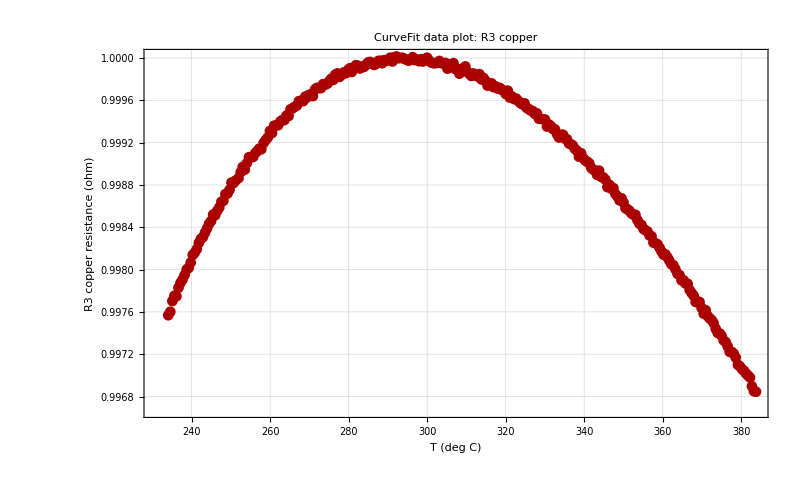

Running CurveFit`LinearFit[]...

n = 290

y(x) = a + b x

Fit of (x,y) (unweighted):

a= 
1.00174 | b= 
-8.84676×10^-6 | 
σ_a= 
0.000340208 | σ_b= 
1.08928×10^-6 | Std. deviation= 
0.00080397

CurveFit fit + residual plot:

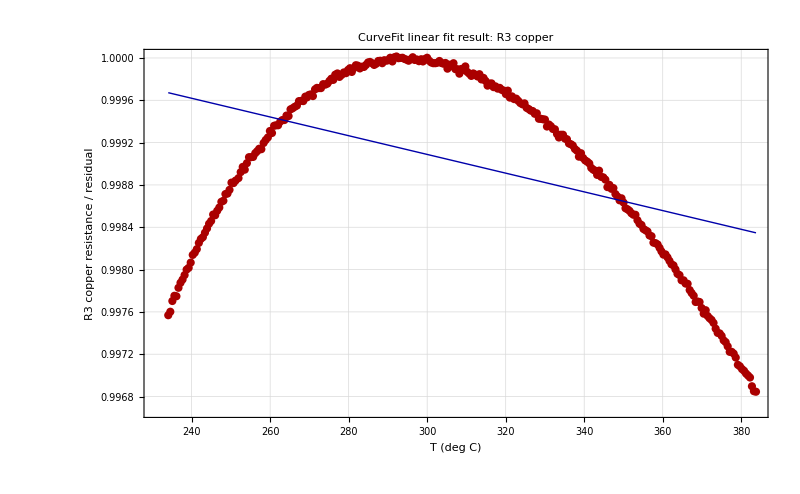
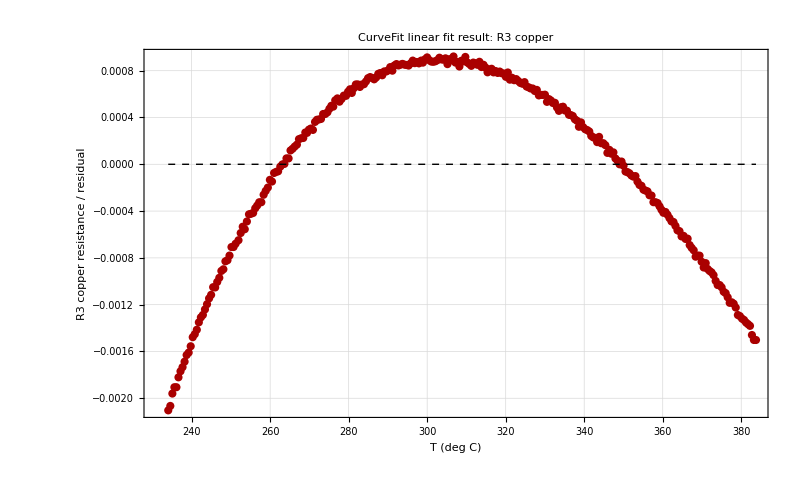
-Graphics-
-Graphics-
y(x) = a + b x
a= 
1.00174 | b= 
-8.84676×10^-6 | 
σ_a= 
0.000340208 | σ_b= 
1.08928×10^-6 | Std. deviation= 
0.00080397

CurveFit fit analysis panel:

y(x) = a + b x
Fit data points: 290
Optimized parameters: 2
Fit of (x,y) (unweighted):
a= 
1.00174 | b= 
-8.84676×10^-6 | 
σ_a= 
0.000340208 | σ_b= 
1.08928×10^-6 | Std. deviation= 
0.00080397
Reduced chi-squared using current data: Missing[ChiSquaredFailed]

Copper numerical summary:

quantity | value | uncertainty | units
a = R(0 C) | 1.00174 | 0.000340208 | ohm
b = dR/dT | -8.84676×10^-6 | 1.08928×10^-6 | ohm/K
reduced chi^2 | Missing[ChiSquaredFailed] |  | 
alpha_0 | -8.83137×10^-6 | 1.08739×10^-6 | 1/K
R(20 C) | 1.00157 | 0.000340905 | ohm
alpha_20 | -8.83293×10^-6 | 1.08758×10^-6 | 1/K
accepted alpha_20 | 0.0039 |  | 1/K
percent difference | 100.226 |  | %

STEP 2 DONE.

Files written to:

C:\Users\ansht\Downloads\exp24\exp24_stepwise_outputs\02_copper_R3_curvefit_exact

```mathematica
ClearAll["Global`*"];

(* =========================*)
(*STEP 2:COPPER R3 USING CURVEFIT GUI BACKEND EXACTLY*)
(* =========================*)

packageParent="C:\\Users\\ansht\\Desktop\\package";
dataDir="C:\\Users\\ansht\\Downloads\\exp24";

If[DirectoryQ[packageParent]&&!MemberQ[$Path,packageParent],AppendTo[$Path,packageParent]];

Needs["CurveFit`"];

SetDirectory[dataDir];

outDir=FileNameJoin[{dataDir,"exp24_stepwise_outputs"}];
step2Dir=FileNameJoin[{outDir,"02_copper_R3_curvefit_exact"}];

If[!DirectoryQ[outDir],CreateDirectory[outDir]];
If[!DirectoryQ[step2Dir],CreateDirectory[step2Dir]];

Print["Step 2 folder: ",step2Dir];

(* =========================*)
(*IMPORT RAW EXP24 DATA*)
(* =========================*)

warmFile=FileNameJoin[{dataDir,"FINAL REAL DATA FILE STARTING WITH 39.1 (1).DAT"}];
noiseFile=FileNameJoin[{dataDir,"ansh_data_file_starting_temp_27.1 (1).DAT"}];

If[!FileExistsQ[warmFile],Print["ERROR: warm-up file missing: ",warmFile];
Abort[];];

readDAT[file_]:=Module[{tab,rows},tab=Import[file,"Table"];
rows=Select[tab,ListQ[#]&&Length[#]>=7&&VectorQ[#[[1;;7]],NumericQ]&];
N[rows[[All,1;;7]]]];

(*Columns:time,T,R1,R2,R3,R4,R5*)
warm=SortBy[readDAT[warmFile],#[[2]]&];

If[FileExistsQ[noiseFile],noise=readDAT[noiseFile],noise=warm[[1;;Min[20,Length[warm]]]]];

T_K=warm[[All,2]];
T_C=T_K-273.15;
R3=warm[[All,5]];

Print[""];
Print["Imported rows: ",Length[warm]];
Print["T_C range: ",{Min[T_C],Max[T_C]}];
Print["R3 range: ",{Min[R3],Max[R3]}];

(* =========================*)
(*UNCERTAINTIES*)
(* =========================*)

detrendedSD[data_,xcol_,ycol_]:=Module[{xy,lm},xy=Select[data[[All,{xcol,ycol}]],VectorQ[#,NumericQ]&];
If[Length[xy]<4,StandardDeviation[xy[[All,2]]],lm=LinearModelFit[xy,x,x];
StandardDeviation[lm["FitResiduals"]]]];

sigmaR3Noise=detrendedSD[noise,1,5];

(*RTD spec from lab manual,but we can toggle x errors off if needed*)
sigmaRTD[T_]:=0.15+0.002 Abs[T-273.16];

includeXErrors=True;

sigmaY=ConstantArray[sigmaR3Noise,Length[R3]];
sigmaX=If[includeXErrors,sigmaRTD/@T_K,ConstantArray[0,Length[R3]]];

Print[""];
Print["sigma_R3 from initial noise file = ",sigmaR3Noise," ohm"];
Print["Using x errors? ",includeXErrors];
Print["sigma_T range = ",{Min[sigmaX],Max[sigmaX]}," K"];

(* =========================*)
(*MAKE A STANDARD CURVEFIT FILE*)
(*CurveFit standard 4-column format is:X,Y,sigmaY,sigmaX based on LoadFile's standard parsing.*)
(* =========================*)

cfInputFile=FileNameJoin[{step2Dir,"curvefit_input_R3_copper_Tc_R3_sigY_sigX.dat"}];

numString[z_]:=ToString[CForm[N[z]]];

cfRows=Map[StringRiffle[numString/@#,"\t"]&,Transpose[{T_C,R3,sigmaY,sigmaX}]];

Export[cfInputFile,Join[{"# CurveFit standard 4-column file for Experiment 24 copper R3","# columns: X=T_C, Y=R3, sigmaY=sigma_R3, sigmaX=sigma_T"},cfRows],"Lines"];

Print[""];
Print["Wrote CurveFit input file:"];
Print[cfInputFile];

(* =========================*)
(*LOAD USING CURVEFIT,SAME AS GUI DATA I/O->LOAD STANDARD FILE*)
(* =========================*)

Print[""];
Print["Loading file into CurveFit with CurveFit`LoadFile[]..."];

CurveFit`LoadFile[cfInputFile,Sorting->True];

Print[""];
Print["CurveFit active data check:"];
Print["n = ",CurveFit`GetData["N"]];
Print["X range = ",{Min[CurveFit`GetData["X"]],Max[CurveFit`GetData["X"]]}];
Print["Y range = ",{Min[CurveFit`GetData["Y"]],Max[CurveFit`GetData["Y"]]}];

(* =========================*)
(*DATA PLOT,SAME AS GUI DATA PLOTS->LINEAR PLOT*)
(* =========================*)

pData=CurveFit`LinearDataPlot[Frame->True,Axes->False,Joined->False,Tips->None,PlotMarkers->Automatic,PlotRange->All,ImageSize->800,FrameLabel->{"T (deg C)","R3 copper resistance (ohm)"},PlotLabel->"CurveFit data plot: R3 copper"];

Export[FileNameJoin[{step2Dir,"R3_copper_01_curvefit_data_plot.pdf"}],pData];

Print[""];
Print["CurveFit data plot:"];
Print[pData];

(* =========================*)
(*FIT,SAME AS GUI FITTING FUNCTIONS->POLYNOMIAL FITS->LINEAR*)
(* =========================*)

Print[""];
Print["Running CurveFit`LinearFit[]..."];
CurveFit`LinearFit[];

(* =========================*)
(*FIT RESULT PLOT,SAME AS GUI PLOT FIT RESULTS->LINEAR PLOT*)
(* =========================*)

pFit=CurveFit`LinearDifferencePlot[Frame->True,Axes->False,Tips->None,PlotRange->All,ImageSize->800,FrameLabel->{"T (deg C)","R3 copper resistance / residual"},PlotLabel->"CurveFit linear fit result: R3 copper"];

Export[FileNameJoin[{step2Dir,"R3_copper_02_curvefit_fit_and_residuals.pdf"}],pFit];

Print[""];
Print["CurveFit fit + residual plot:"];
Print[pFit];

(* =========================*)
(*FIT ANALYSIS,SAME AS GUI FIT ANALYSIS*)
(* =========================*)

chi2red=Quiet[Check[N[CurveFit`ChiSquared[]],Missing["ChiSquaredFailed"]]];

fitPanel=Quiet[Check[Column[{Style[CurveFit`fYstring,Bold],Style["Fit data points: "<>ToString[CurveFit`Nfit]<>"\nOptimized parameters: "<>ToString[CurveFit`Pfit],12],CurveFit`Tfit,Framed[CurveFit`FitResults],"Reduced chi-squared using current data: "<>ToString[chi2red]}],"Fit panel not available in this CurveFit version."]];

Export[FileNameJoin[{step2Dir,"R3_copper_03_curvefit_fit_results_panel.pdf"}],fitPanel];

Print[""];
Print["CurveFit fit analysis panel:"];
Print[fitPanel];

(* =========================*)
(*DERIVED COPPER NUMBERS*)
(*Use the final CurveFit a,b,siga,sigb after LinearFit[].*)
(* =========================*)

aCu=N[CurveFit`a];
bCu=N[CurveFit`b];
sigaCu=N[CurveFit`siga];
sigbCu=N[CurveFit`sigb];

alpha0=bCu/aCu;
sigmaAlpha0=Sqrt[(sigbCu/aCu)^2+((bCu sigaCu)/(aCu^2))^2];

R20=aCu+20 bCu;
sigmaR20=Sqrt[sigaCu^2+(20 sigbCu)^2];

alpha20=bCu/R20;
sigmaAlpha20=Sqrt[(sigbCu/R20)^2+((bCu sigmaR20)/(R20^2))^2];

acceptedAlpha20=0.0039;
percentDiff=100 Abs[alpha20-acceptedAlpha20]/acceptedAlpha20;

summary={{"quantity","value","uncertainty","units"},{"a = R(0 C)",aCu,sigaCu,"ohm"},{"b = dR/dT",bCu,sigbCu,"ohm/K"},{"reduced chi^2",chi2red,"",""},{"alpha_0",alpha0,sigmaAlpha0,"1/K"},{"R(20 C)",R20,sigmaR20,"ohm"},{"alpha_20",alpha20,sigmaAlpha20,"1/K"},{"accepted alpha_20",acceptedAlpha20,"","1/K"},{"percent difference",percentDiff,"","%"}};

Export[FileNameJoin[{step2Dir,"R3_copper_04_numerical_summary.csv"}],summary];

Print[""];
Print["Copper numerical summary:"];
Print[Grid[summary,Frame->All]];

Print[""];
Print["STEP 2 DONE."];
Print["Files written to:"];
Print[step2Dir];
```

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*PHASE 10:Global physics constrained H/D fit*)
(*Fits one shared isotope slope directly across spectra*)
(* =====================================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\exp25\\PHASE1_real_wavelength_files";

actualHDDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Actual_HD_mixed_lamp"}];

calSummaryFile=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_linear_calibration_summary.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE10_global_physics_constrained_fit"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"figures"}];
tableDir=FileNameJoin[{outRoot,"tables"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

(*----------helpers----------*)

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",actualHDDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

getCalValue[rows_,key_]:=Module[{row},row=SelectFirst[rows,#[[1]]==key&];
If[MissingQ[row],Missing["NotFound"],N@ToExpression[row[[2]]]]];

bound[lo_,hi_,z_]:=(lo+hi)/2+(hi-lo)/2 Tanh[z];

invBound[lo_,hi_,val_]:=Module[{u},u=(2 val-lo-hi)/(hi-lo);
ArcTanh[Clip[u,{-0.95,0.95}]]];

ampNear[data_,muGuess_,base_,width_]:=Module[{near},near=Select[data,Abs[#[[1]]-muGuess]<=width&];
If[Length[near]==0,Max[data[[All,2]]]-base,Max[near[[All,2]]]-base]];

numQ[x_]:=NumericQ[x]&&x=!=Indeterminate&&x=!=ComplexInfinity;

(*----------calibration----------*)

calRows=Import[calSummaryFile,"CSV"];

aCal=getCalValue[calRows,"a_intercept_nm"];
bCal=getCalValue[calRows,"b_slope"];

If[!numQ[aCal]||!numQ[bCal],Print["Calibration not found."];
Abort[];];

Print["Using calibration:"];
Print["lambda_corrected = ",aCal," + ",bCal," lambda_observed"];

(*----------line specs----------*)

specs={<|"id"->1,"label"->"H alpha","fileKey"->"656.495","window"->{656.18,656.47},"hGuess"->656.400,"hRange"->{656.375,656.425},"sigRange"->{0.015,0.075}|>,<|"id"->2,"label"->"H beta","fileKey"->"486.320","window"->{486.08,486.43},"hGuess"->486.325,"hRange"->{486.300,486.350},"sigRange"->{0.015,0.065}|>,<|"id"->3,"label"->"H gamma","fileKey"->"434.373","window"->{434.08,434.35},"hGuess"->434.280,"hRange"->{434.250,434.310},"sigRange"->{0.015,0.065}|>,<|"id"->4,"label"->"H delta","fileKey"->"410.500","window"->{410.25,410.53},"hGuess"->410.410,"hRange"->{410.385,410.435},"sigRange"->{0.015,0.075}|>};

sRange={0.000235,0.000315};
sGuess=0.500/1836;

(*----------import data----------*)

lineData=Table[Module[{file,raw,data,xvals,yvals,edgeN,c0,ampD0,ampH0,hGuess,dGuess,sepGuess},file=findFile[spec["fileKey"]];
If[MissingQ[file],Print["Missing file for ",spec["label"]];
Abort[];];
raw=importNumeric[file];
data=cropData[raw,spec["window"]];
xvals=data[[All,1]];
yvals=data[[All,2]];
edgeN=Min[5,Length[yvals]];
c0=Median[Join[Take[yvals,edgeN],Take[yvals,-edgeN]]];
hGuess=spec["hGuess"];
sepGuess=(sGuess/bCal) (aCal+bCal hGuess);
dGuess=hGuess-sepGuess;
ampD0=Max[0.001,ampNear[data,dGuess,c0,0.05]];
ampH0=Max[0.001,ampNear[data,hGuess,c0,0.05]];
<|"spec"->spec,"file"->file,"data"->data,"x0"->Mean[MinMax[xvals]],"c0"->c0,"d0"->0,"ampD0"->ampD0,"ampH0"->ampH0,"sepGuess"->sepGuess,"dGuess"->dGuess|>],{spec,specs}];

combinedData=Join@@Table[({lineData[[i,"spec","id"]],#[[1]],#[[2]]}&/@lineData[[i,"data"]]),{i,Length[lineData]}];

Print["Total data points = ",Length[combinedData]];

(*----------parameter setup----------*)

(*Global slope*)
sExpr=bound[sRange[[1]],sRange[[2]],zS];

(*H centers and widths*)
h1=bound[specs[[1,"hRange",1]],specs[[1,"hRange",2]],zH1];
h2=bound[specs[[2,"hRange",1]],specs[[2,"hRange",2]],zH2];
h3=bound[specs[[3,"hRange",1]],specs[[3,"hRange",2]],zH3];
h4=bound[specs[[4,"hRange",1]],specs[[4,"hRange",2]],zH4];

sig1=bound[specs[[1,"sigRange",1]],specs[[1,"sigRange",2]],zSig1];
sig2=bound[specs[[2,"sigRange",1]],specs[[2,"sigRange",2]],zSig2];
sig3=bound[specs[[3,"sigRange",1]],specs[[3,"sigRange",2]],zSig3];
sig4=bound[specs[[4,"sigRange",1]],specs[[4,"sigRange",2]],zSig4];

dCenter[h_]:=h-(sExpr/bCal) (aCal+bCal h);

d1c=dCenter[h1];
d2c=dCenter[h2];
d3c=dCenter[h3];
d4c=dCenter[h4];

lineModel[id_,x_,c_,d_,aD_,aH_,h_,sig_,x0_]:=c+d (x-x0)+aD^2 Exp[-(x-dCenter[h])^2/(2 sig^2)]+aH^2 Exp[-(x-h)^2/(2 sig^2)];

expr1=lineModel[line,x,c1,dL1,aD1,aH1,h1,sig1,lineData[[1,"x0"]]];
expr2=lineModel[line,x,c2,dL2,aD2,aH2,h2,sig2,lineData[[2,"x0"]]];
expr3=lineModel[line,x,c3,dL3,aD3,aH3,h3,sig3,lineData[[3,"x0"]]];
expr4=lineModel[line,x,c4,dL4,aD4,aH4,h4,sig4,lineData[[4,"x0"]]];

model=KroneckerDelta[line,1] expr1+KroneckerDelta[line,2] expr2+KroneckerDelta[line,3] expr3+KroneckerDelta[line,4] expr4;

paramList={{zS,invBound[sRange[[1]],sRange[[2]],sGuess]},{c1,lineData[[1,"c0"]]},{dL1,0},{aD1,Sqrt[lineData[[1,"ampD0"]]]},{aH1,Sqrt[lineData[[1,"ampH0"]]]},{zH1,invBound[specs[[1,"hRange",1]],specs[[1,"hRange",2]],specs[[1,"hGuess"]]]},{zSig1,invBound[specs[[1,"sigRange",1]],specs[[1,"sigRange",2]],Mean[specs[[1,"sigRange"]]]]},{c2,lineData[[2,"c0"]]},{dL2,0},{aD2,Sqrt[lineData[[2,"ampD0"]]]},{aH2,Sqrt[lineData[[2,"ampH0"]]]},{zH2,invBound[specs[[2,"hRange",1]],specs[[2,"hRange",2]],specs[[2,"hGuess"]]]},{zSig2,invBound[specs[[2,"sigRange",1]],specs[[2,"sigRange",2]],Mean[specs[[2,"sigRange"]]]]},{c3,lineData[[3,"c0"]]},{dL3,0},{aD3,Sqrt[lineData[[3,"ampD0"]]]},{aH3,Sqrt[lineData[[3,"ampH0"]]]},{zH3,invBound[specs[[3,"hRange",1]],specs[[3,"hRange",2]],specs[[3,"hGuess"]]]},{zSig3,invBound[specs[[3,"sigRange",1]],specs[[3,"sigRange",2]],Mean[specs[[3,"sigRange"]]]]},{c4,lineData[[4,"c0"]]},{dL4,0},{aD4,Sqrt[lineData[[4,"ampD0"]]]},{aH4,Sqrt[lineData[[4,"ampH0"]]]},{zH4,invBound[specs[[4,"hRange",1]],specs[[4,"hRange",2]],specs[[4,"hGuess"]]]},{zSig4,invBound[specs[[4,"sigRange",1]],specs[[4,"sigRange",2]],Mean[specs[[4,"sigRange"]]]]}};

rawParamNames=paramList[[All,1]];

Print["Running global constrained fit..."];

fit=TimeConstrained[Quiet@NonlinearModelFit[combinedData,model,paramList,{line,x},MaxIterations->12000],180,$Failed];

If[fit===$Failed,Print["Global fit timed out or failed."];
Abort[];];

params=fit["BestFitParameters"];
cov=Quiet@Check[fit["CovarianceMatrix"],Missing["NA"]];

seExpr[expr_]:=If[MatrixQ[cov],Module[{g},g=D[expr,{rawParamNames}]/. params;
Sqrt[g.cov.g]],Missing["NA"]];

sVal=sExpr/. params;
sSE=seExpr[sExpr];

mpme=0.500/sVal;
mpmeSE=If[numQ[sSE],0.500 sSE/sVal^2,Missing["NA"]];

hVals={h1,h2,h3,h4}/. params;
sigVals={sig1,sig2,sig3,sig4}/. params;
dVals={d1c,d2c,d3c,d4c}/. params;

lambdaHCorr=aCal+bCal hVals;
lambdaDCorr=aCal+bCal dVals;
deltaCorr=lambdaHCorr-lambdaDCorr;

residuals=combinedData/. {li_,xi_,yi_}:>{li,xi,yi-fit[li,xi]};
rss=Total[residuals[[All,3]]^2];
rms=Sqrt[Mean[residuals[[All,3]]^2]];

Print["GLOBAL PHYSICS CONSTRAINED RESULT"];
Print["s = ",sVal," ± ",sSE];
Print["m_p/m_e = ",mpme," ± ",mpmeSE];
Print["RMS residual all points = ",rms];

resultRows=Table[<|"line"->specs[[i,"label"]],"muD_obs_nm"->dVals[[i]],"muH_obs_nm"->hVals[[i]],"delta_obs_nm"->hVals[[i]]-dVals[[i]],"lambdaH_corr_nm"->lambdaHCorr[[i]],"delta_corr_nm"->deltaCorr[[i]],"sigma_nm"->sigVals[[i]]|>,{i,4}];

Export[FileNameJoin[{tableDir,"global_physics_constrained_line_results.csv"}],Prepend[Values/@resultRows,Keys[First[resultRows]]],"CSV"];

Export[FileNameJoin[{tableDir,"global_physics_constrained_summary.csv"}],{{"quantity","value"},{"slope_s",sVal},{"slope_s_SE",sSE},{"mp_over_me",mpme},{"mp_over_me_SE",mpmeSE},{"RMS_residual_all_points",rms},{"RSS",rss}},"CSV"];

latexRows=resultRows/. r_Association:>StringRiffle[{r["line"],NumberForm[r["muD_obs_nm"],{8,4}],NumberForm[r["muH_obs_nm"],{8,4}],NumberForm[r["delta_obs_nm"],{8,5}],NumberForm[r["lambdaH_corr_nm"],{8,4}],NumberForm[r["delta_corr_nm"],{8,5}],NumberForm[r["sigma_nm"],{8,4}]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"global_physics_constrained_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

(*----------per line figures----------*)

makeLinePlot[i_]:=Module[{spec,data,id,xmin,xmax,yMin,yMax,res,totalPlot,residPlot},spec=specs[[i]];
id=spec["id"];
data=lineData[[i,"data"]];
{xmin,xmax}=MinMax[data[[All,1]]];
{yMin,yMax}=MinMax[data[[All,2]]];
res=Select[residuals,#[[1]]==id&];
totalPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->420,FrameLabel->{"Wavelength (nm)","Signal (V)"},PlotLabel->Style[spec["label"]<>" global physics fit",11,FontFamily->font],LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font}],Plot[fit[id,x],{x,xmin,xmax},PlotStyle->{Red,Thick}],Graphics[{Blue,Dashed,AbsoluteThickness[1.2],Line[{{dVals[[i]],yMin},{dVals[[i]],yMax}}],Purple,Dashed,AbsoluteThickness[1.2],Line[{{hVals[[i]],yMin},{hVals[[i]],yMax}}]}]];
residPlot=ListPlot[res[[All,{2,3}]],Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->420,FrameLabel->{"Wavelength (nm)","Residual (V)"},PlotLabel->Style[spec["label"]<>" residuals",11,FontFamily->font],GridLines->{None,{0}},LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font}];
GraphicsColumn[{totalPlot,residPlot},Spacings->0.15,ImageSize->440]];

lineFigures=Table[makeLinePlot[i],{i,4}];

Export[FileNameJoin[{figDir,"global_physics_fit_alpha_beta.pdf"}],GraphicsRow[{lineFigures[[1]],lineFigures[[2]]},Spacings->0.2,ImageSize->900],"PDF"];

Export[FileNameJoin[{figDir,"global_physics_fit_gamma_delta.pdf"}],GraphicsRow[{lineFigures[[3]],lineFigures[[4]]},Spacings->0.2,ImageSize->900],"PDF"];

(*----------isotope shift figure----------*)

shiftData=Transpose[{lambdaHCorr,deltaCorr}];

shiftFig=Show[ListPlot[shiftData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->430,FrameLabel->{"Corrected H wavelength (nm)","H-D separation (nm)"},PlotLabel->Style["Global physics constrained isotope shift",11,FontFamily->font],LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font}],Plot[sVal x,{x,Min[lambdaHCorr]-12,Max[lambdaHCorr]+12},PlotStyle->{Red,Thick}]];

Export[FileNameJoin[{figDir,"global_physics_constrained_shift_fit.pdf"}],shiftFig,"PDF"];

Print["Outputs saved here:"];
Print[outRoot];

Dataset[resultRows]

SystemOpen[outRoot];
```

Using calibration:

lambda_corrected = 0.423395 + 0.998274 lambda_observed

Total data points = 106

Running global constrained fit...

General::munfl: Exp[-9.07564×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.08977×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.4604×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

GLOBAL PHYSICS CONSTRAINED RESULT

s = 0.000271553 ± Missing[NA]

m_p/m_e = 1841.26 ± Missing[NA]

RMS residual all points = 0.0268512

General::munfl: Exp[-9.07564×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.08977×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.4604×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Outputs saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE10_global_physics_constrained_fit

General::munfl: Exp[-9.07564×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.08977×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.4604×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Best slope from global fit = 0.000271553

Best m_p/m_e = 1841.26

RSS full = 0.0764248

N data = 106

parameters = 25

dof = 81

sigma^2 estimate = 0.000943516

Running profile scan with 41 fixed slope values...

General::munfl: Exp[-1.00353×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.00497×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.91552×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

PROFILE UNCERTAINTY RESULT

s profile best = 0.000271553

m_p/m_e profile best = 1841.26

1 sigma s interval = [0.000271321, 0.000271782]

1 sigma m_p/m_e interval = [1839.71, 1842.83]

m_p/m_e = 1841.26 +1.57473 -1.54962

2 sigma m_p/m_e interval = [1835.08, 1847.58]

Outputs saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\exp25\PHASE1_real_wavelength_files\PHASE10B_global_profile_uncertainty

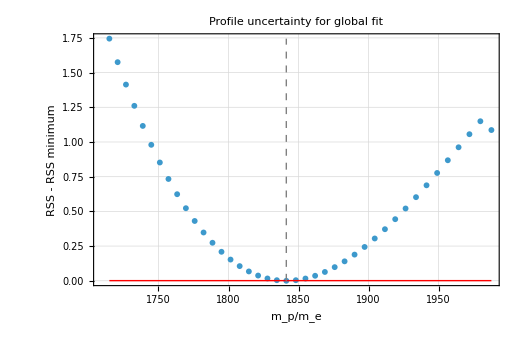

```mathematica
(* =====================================================*)(*PHASE 10B:Profile uncertainty for global slope s*)(*Run after PHASE 10,do not ClearAll*)(* =====================================================*)phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\exp25\\PHASE1_real_wavelength_files";

outRoot=FileNameJoin[{phase1Dir,"PHASE10B_global_profile_uncertainty"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"figures"}];
tableDir=FileNameJoin[{outRoot,"tables"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

If[!ValueQ[fit]||!ValueQ[params]||!ValueQ[paramList]||!ValueQ[combinedData],Print["Missing Phase 10 variables. Rerun Phase 10 first, then run this cell."];
Abort[];];

numQ[x_]:=NumericQ[x]&&x=!=Indeterminate&&x=!=ComplexInfinity;

sBest=sExpr/. params;
mpmeBest=0.500/sBest;

rssFull=Total[combinedData/. {li_,xi_,yi_}:>(yi-fit[li,xi])^2];

nData=Length[combinedData];
pFull=Length[paramList];
dof=nData-pFull;

sigma2Hat=rssFull/dof;

threshold1=rssFull+sigma2Hat;
threshold2=rssFull+4 sigma2Hat;

Print["Best slope from global fit = ",sBest];
Print["Best m_p/m_e = ",mpmeBest];
Print["RSS full = ",rssFull];
Print["N data = ",nData];
Print["parameters = ",pFull];
Print["dof = ",dof];
Print["sigma^2 estimate = ",sigma2Hat];

fixedStartParams[sFixed_]:=Rest[paramList]/. {sym_,init_}:>{sym,sym/. params};

fitAtFixedS[sFixed_]:=Module[{zFixed,modelFixed,pList,f,rss},zFixed=invBound[sRange[[1]],sRange[[2]],sFixed];
modelFixed=model/. zS->zFixed;
pList=fixedStartParams[sFixed];
f=TimeConstrained[Quiet@NonlinearModelFit[combinedData,modelFixed,pList,{line,x},MaxIterations->8000],35,$Failed];
If[f===$Failed,<|"s"->sFixed,"status"->"failed","RSS"->Missing["NA"]|>,rss=Total[combinedData/. {li_,xi_,yi_}:>(yi-f[li,xi])^2];
<|"s"->sFixed,"status"->"ok","RSS"->rss|>]];

scanWidth=2.0*10^-5;

scanS=Sort@DeleteDuplicates@Join[Subdivide[sBest-scanWidth,sBest+scanWidth,40],{sBest}];

Print["Running profile scan with ",Length[scanS]," fixed slope values..."];

profileRows=fitAtFixedS/@scanS;

Export[FileNameJoin[{tableDir,"profile_scan_raw.csv"}],Prepend[Values/@profileRows,Keys[First[profileRows]]],"CSV"];

profileData=SortBy[({#["s"],#["RSS"]}&/@Select[profileRows,#["status"]=="ok"&&numQ[#["RSS"]]&]),First];

If[Length[profileData]<5,Print["Too few successful profile points. Increase timeout or rerun."];
Abort[];];

rssMin=Min[profileData[[All,2]]];
sProfileBest=profileData[[First@Ordering[profileData[[All,2]],1],1]];
mpmeProfileBest=0.500/sProfileBest;

threshold1Profile=rssMin+sigma2Hat;
threshold2Profile=rssMin+4 sigma2Hat;

crossLeft[data_,threshold_,s0_]:=Module[{left,vals,pair,s1,s2,y1,y2},left=SortBy[Select[data,#[[1]]<=s0&],First];
vals=left/. {ss_,rr_}:>{ss,rr-threshold};
pair=SelectFirst[Partition[vals,2,1],#[[1,2]]>=0&&#[[2,2]]<=0&];
If[MissingQ[pair],Missing["NoCrossing"],{s1,y1}=pair[[1]];
{s2,y2}=pair[[2]];
s1+(0-y1) (s2-s1)/(y2-y1)]];

crossRight[data_,threshold_,s0_]:=Module[{right,vals,pair,s1,s2,y1,y2},right=SortBy[Select[data,#[[1]]>=s0&],First];
vals=right/. {ss_,rr_}:>{ss,rr-threshold};
pair=SelectFirst[Partition[vals,2,1],#[[1,2]]<=0&&#[[2,2]]>=0&];
If[MissingQ[pair],Missing["NoCrossing"],{s1,y1}=pair[[1]];
{s2,y2}=pair[[2]];
s1+(0-y1) (s2-s1)/(y2-y1)]];

sLow1=crossLeft[profileData,threshold1Profile,sProfileBest];
sHigh1=crossRight[profileData,threshold1Profile,sProfileBest];

sLow2=crossLeft[profileData,threshold2Profile,sProfileBest];
sHigh2=crossRight[profileData,threshold2Profile,sProfileBest];

intervalFromS[sLow_,sHigh_]:=Module[{mpLow,mpHigh,errMinus,errPlus},If[MissingQ[sLow]||MissingQ[sHigh],<|"mp_lower"->Missing["NoCrossing"],"mp_upper"->Missing["NoCrossing"],"err_minus"->Missing["NoCrossing"],"err_plus"->Missing["NoCrossing"]|>,mpLow=0.500/sHigh;
mpHigh=0.500/sLow;
errMinus=mpmeProfileBest-mpLow;
errPlus=mpHigh-mpmeProfileBest;
<|"mp_lower"->mpLow,"mp_upper"->mpHigh,"err_minus"->errMinus,"err_plus"->errPlus|>]];

int1=intervalFromS[sLow1,sHigh1];
int2=intervalFromS[sLow2,sHigh2];

summary={{"quantity","value"},{"s_full_fit",sBest},{"mpme_full_fit",mpmeBest},{"rss_full_fit",rssFull},{"n_data",nData},{"n_parameters",pFull},{"dof",dof},{"sigma2_hat",sigma2Hat},{"s_profile_best",sProfileBest},{"mpme_profile_best",mpmeProfileBest},{"rss_profile_min",rssMin},{"s_low_1sigma",sLow1},{"s_high_1sigma",sHigh1},{"mpme_lower_1sigma",int1["mp_lower"]},{"mpme_upper_1sigma",int1["mp_upper"]},{"mpme_err_minus_1sigma",int1["err_minus"]},{"mpme_err_plus_1sigma",int1["err_plus"]},{"s_low_2sigma",sLow2},{"s_high_2sigma",sHigh2},{"mpme_lower_2sigma",int2["mp_lower"]},{"mpme_upper_2sigma",int2["mp_upper"]},{"mpme_err_minus_2sigma",int2["err_minus"]},{"mpme_err_plus_2sigma",int2["err_plus"]}};

Export[FileNameJoin[{tableDir,"global_profile_uncertainty_summary.csv"}],summary,"CSV"];

profileForPlot=({0.500/#[[1]],#[[2]]-rssMin}&/@profileData);
profileForPlot=SortBy[profileForPlot,First];

profileFig=Show[ListPlot[profileForPlot,Frame->True,Axes->False,PlotMarkers->{Automatic,6},ImageSize->520,AspectRatio->0.65,FrameLabel->{"m_p/m_e","RSS - RSS minimum"},PlotLabel->Style["Profile uncertainty for global fit",12,FontFamily->font],LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font}],Graphics[{Red,Thick,Line[{{Min[profileForPlot[[All,1]]],sigma2Hat},{Max[profileForPlot[[All,1]]],sigma2Hat}}],Gray,Dashed,Line[{{mpmeProfileBest,0},{mpmeProfileBest,Max[profileForPlot[[All,2]]]}}],If[numQ[int1["mp_lower"]]&&numQ[int1["mp_upper"]],{Blue,Dashed,Line[{{int1["mp_lower"],0},{int1["mp_lower"],sigma2Hat}}],Line[{{int1["mp_upper"],0},{int1["mp_upper"],sigma2Hat}}]},{}]}]];

Export[FileNameJoin[{figDir,"global_profile_uncertainty_curve.pdf"}],profileFig,"PDF"];

latexText=StringRiffle[{"Global slope $s$ & "<>ToString[NumberForm[sProfileBest,{9,7}]]<>" \\\\","$m_p/m_e$ & "<>ToString[NumberForm[mpmeProfileBest,{8,1}]]<>"$^{+"<>ToString[NumberForm[int1["err_plus"],{5,1}]]<>"}_{-"<>ToString[NumberForm[int1["err_minus"],{5,1}]]<>"}$ \\\\","RSS minimum & "<>ToString[NumberForm[rssMin,{8,5}]]<>" \\\\","Degrees of freedom & "<>ToString[dof]<>" \\\\"},"\n"];

Export[FileNameJoin[{tableDir,"global_profile_uncertainty_table_body.tex"}],latexText,"Text"];

Print["PROFILE UNCERTAINTY RESULT"];
Print["s profile best = ",sProfileBest];
Print["m_p/m_e profile best = ",mpmeProfileBest];

Print["1 sigma s interval = [",sLow1,", ",sHigh1,"]"];
Print["1 sigma m_p/m_e interval = [",int1["mp_lower"],", ",int1["mp_upper"],"]"];
Print["m_p/m_e = ",mpmeProfileBest," +",int1["err_plus"]," -",int1["err_minus"]];

Print["2 sigma m_p/m_e interval = [",int2["mp_lower"],", ",int2["mp_upper"],"]"];

Print["Outputs saved here:"];
Print[outRoot];

profileFig

SystemOpen[outRoot];
```